# BeH_2 Hamiltonian, 14 qubits, stable distance

## questlink and modules

```mathematica
ParseHamiltonian[file_]:=Module[{shams,lhams,λ,idx,hterm,replace,hamiltonian,ham},
shams=Import[file];
lhams=ToExpression@StringSplit[StringSplit[shams,"\n"]];
hamiltonian=Plus@@Table[
λ=term⟦1⟧;
idx=0;
replace={1:>Subscript[X, idx++],2:>Subscript[Y, idx++],3:>Subscript[Z, idx++],0:>(idx++)*0+1};
hterm=Times@@(#/.replace&/@term⟦2;;⟧);
λ*hterm
,{term,lhams}];
ham=SimplifyPaulis[hamiltonian];
{ham,idx,Length[ham/.Plus->List]}
]
ParseHamiltonian::usage="ParseHamiltonian[filepath], return {hamiltonian, nqubits, nterms}"
```

ParseHamiltonian[filepath], return {hamiltonian, nqubits, nterms}

Format the hamiltonian from qiskit; daniel’s format

```mathematica
FormatHamiltonian[filename_]:=Module[{stringham,ham},
stringham=Import[filename];
ham=ToExpression[stringham];
Total@Apply[Times,ham,1]
]
```

## Hamiltonian generation

```mathematica
{hamiltonian,nqubits,nterms}=ParseHamiltonian["/home/cica/vqe/richard/BeH2.txt"];
```

```mathematica
{nqubits,nterms}
```

{14,666}

```mathematica
groundstate=-15.5951755114264;
```

Get the <N^2>

```mathematica
occupation=FormatHamiltonian["/home/cica/vqe/dani/generate_operators/data/num_beh2.txt"]
```

7-0.5 Z_0-0.5 Z_1-0.5 Z_2-0.5 Z_3-0.5 Z_4-0.5 Z_5-0.5 Z_6-0.5 Z_7-0.5 Z_8-0.5 Z_9-0.5 Z_10-0.5 Z_11-0.5 Z_12-0.5 Z_13

```mathematica
opnum=SimplifyPaulis[(6-occupation)*(6-occupation)];
```

```mathematica
spin=FormatHamiltonian["/home/cica/vqe/dani/generate_operators/data/spin_beh2.txt"];
```

## Run

```mathematica
DefaultConfig@14
```

<|nqubit→14,methode→NG,gatespercycle→80,ngatesinit→100,fixansatz→{},fixansatzparams→<||>,ansatzspace→{0,1,2,3,4,5,6,7,8,9,10,11,12,13},weightgate→{1→0.2,2→0.8},ansatzinit→{X_0,X_1,X_2,X_3,X_4,X_5},swapfabricdepth→0,maxfevbf→100,greediness→8,greedinessinit→8,greedflat→0.01,maxgreediter→120,gradstep→0.01,dθ→0.01,gradstepmultiply→2,αtikhonov→1/10000,θignore→1/1000,metignore→1/1000,perfectingflat→0.00015,pruningerror→0.1,iterconverge→20,globalconverge→2,θinitrange→π/4,ϵfin→1/10000000,slowfirst→True,refine→2,gateset→{Rx_#1[θ]&,Ry_#1[θ]&,Rz_#1[θ]&,C_#1[Rx_#2[θ]]&,C_#1[Ry_#2[θ]]&,C_#1[Rz_#2[θ]]&}|>

```mathematica
DestroyAllQuregs[]
```

Trial 1

Wed 12 Jan 2022 15:41:30GMT

target: -15.5952

@cycle1, fev:876, <E>: -15.56331861206101 nansatz: 5 merged-smallθ-metric-bf-gmerged: {0, 0, 0, 95, 0}

@cycle2, fev:1633, <E>: -15.56932235713765 nansatz: 10 merged-smallθ-metric-bf-gmerged: {0, 0, 40, 130, 0}

@cycle3, fev:3172, <E>: -15.569482156383627 nansatz: 15 merged-smallθ-metric-bf-gmerged: {0, 0, 71, 174, 0}

@cycle4, fev:5040, <E>: -15.573532603715934 nansatz: 22 merged-smallθ-metric-bf-gmerged: {0, 0, 99, 216, 1}

@cycle5, fev:7371, <E>: -15.575306350298018 nansatz: 28 merged-smallθ-metric-bf-gmerged: {0, 0, 99, 286, 4}

@cycle6, fev:10812, <E>: -15.5755320351193 nansatz: 30 merged-smallθ-metric-bf-gmerged: {0, 0, 99, 364, 0}

@cycle7, fev:12954, <E>: -15.580099093838799 nansatz: 23 merged-smallθ-metric-bf-gmerged: {0, 0, 143, 407, 0}

@cycle8, fev:17202, <E>: -15.580251679553065 nansatz: 33 merged-smallθ-metric-bf-gmerged: {0, 0, 144, 476, 0}

@cycle9, fev:21520, <E>: -15.580419277844907 nansatz: 37 merged-smallθ-metric-bf-gmerged: {1, 0, 175, 520, 0}

@cycle10, pathetic result.

I'm slowing down. Number of gates is increased to 96 @cycle 10

@cycle10, fev:22140, <E>: -15.580419277844907 nansatz: 37 merged-smallθ-metric-bf-gmerged: {1, 0, 175, 520, 1}

@cycle11, fev:25178, <E>: -15.582831275494064 nansatz: 27 merged-smallθ-metric-bf-gmerged: {1, 0, 207, 593, 1}

@cycle12, fev:30998, <E>: -15.583055481332757 nansatz: 40 merged-smallθ-metric-bf-gmerged: {2, 0, 240, 642, 0}

@cycle13, fev:37169, <E>: -15.583320246393313 nansatz: 49 merged-smallθ-metric-bf-gmerged: {3, 1, 240, 727, 0}

@cycle14, pathetic result.

I'm slowing down. Number of gates is increased to 116 @cycle 14

@cycle14, fev:38252, <E>: -15.583320246393313 nansatz: 49 merged-smallθ-metric-bf-gmerged: {3, 1, 240, 727, 0}

@cycle15, fev:43411, <E>: -15.593383491381175 nansatz: 46 merged-smallθ-metric-bf-gmerged: {3, 1, 240, 846, 0}

@cycle16, fev:49765, <E>: -15.59407759359169 nansatz: 65 merged-smallθ-metric-bf-gmerged: {3, 1, 240, 943, 0}

@cycle17, fev:57771, <E>: -15.594248964529427 nansatz: 74 merged-smallθ-metric-bf-gmerged: {3, 1, 240, 1050, 0}

@cycle18, fev:66704, <E>: -15.594389362862355 nansatz: 89 merged-smallθ-metric-bf-gmerged: {3, 1, 240, 1150, 3}

@cycle19, pathetic result.

I'm slowing down. Number of gates is increased to 140 @cycle 19

@cycle19, fev:68074, <E>: -15.594389362862355 nansatz: 89 merged-smallθ-metric-bf-gmerged: {3, 1, 240, 1150, 1}

@cycle20, pathetic result.

I'm slowing down. Number of gates is increased to 168 @cycle 20

@cycle20, fev:69711, <E>: -15.594389362862355 nansatz: 89 merged-smallθ-metric-bf-gmerged: {3, 1, 240, 1150, 0}

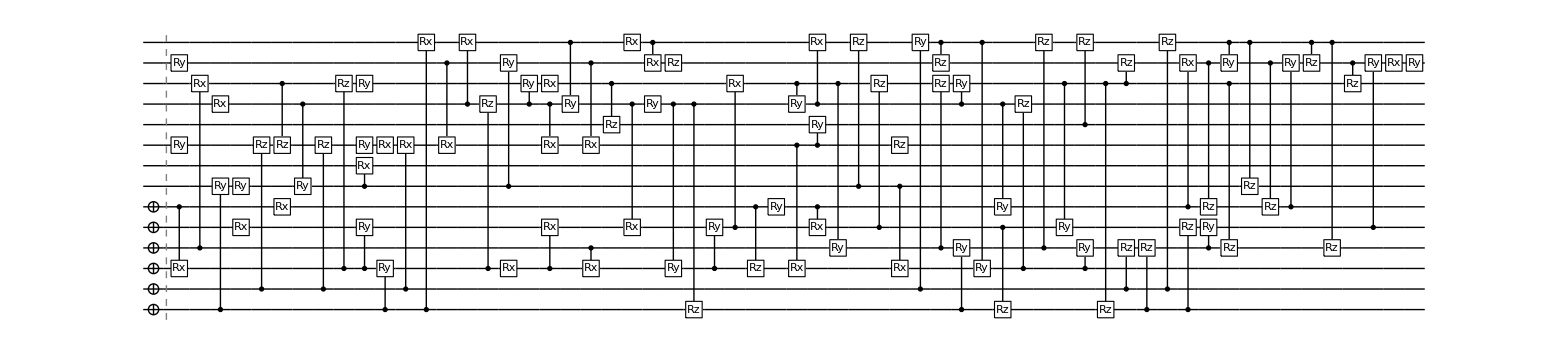

runtime=18.6145 hours

nansatz=89

nansatz/cycle={0,5,10,15,22,28,30,23,33,37,27,40,49,46,65,74,89,89}

<E>/cycle={-15.5603,-15.5633,-15.5693,-15.5695,-15.5735,-15.5753,-15.5755,-15.5801,-15.5803,-15.5804,-15.5828,-15.5831,-15.5833,-15.5934,-15.5941,-15.5942,-15.5944,-15.5944}

ϵ/cycle={0.0348688,0.0318569,0.0258532,0.0256934,0.0216429,0.0198692,0.0196435,0.0150764,0.0149238,0.0147562,0.0123442,0.01212,0.0118553,0.00179202,0.00109792,0.000926547,0.000786149,0.000786149}

<E>=-15.5944

<E>-E_gs=0.000786149

<S^2>=0.000193133

<(4-N)^2>=0.000238218

Trial 2

Thu 13 Jan 2022 10:18:22GMT

target: -15.5952

@cycle1, fev:1559, <E>: -15.562642609504135 nansatz: 18 merged-smallθ-metric-bf-gmerged: {0, 0, 0, 82, 0}

@cycle2, fev:2957, <E>: -15.565629149380504 nansatz: 12 merged-smallθ-metric-bf-gmerged: {0, 0, 0, 165, 0}

@cycle3, pathetic result.

I'm slowing down. Number of gates is increased to 96 @cycle 3

@cycle3, fev:3437, <E>: -15.565629149380504 nansatz: 12 merged-smallθ-metric-bf-gmerged: {0, 0, 0, 165, 0}

@cycle4, fev:5231, <E>: -15.568376659902906 nansatz: 17 merged-smallθ-metric-bf-gmerged: {0, 0, 0, 256, 0}

@cycle5, pathetic result.

I'm slowing down. Number of gates is increased to 116 @cycle 5

@cycle5, fev:6061, <E>: -15.568376659902906 nansatz: 17 merged-smallθ-metric-bf-gmerged: {0, 0, 0, 256, 2}

@cycle6, fev:9332, <E>: -15.576831243634665 nansatz: 30 merged-smallθ-metric-bf-gmerged: {0, 0, 0, 359, 2}

@cycle7, fev:13049, <E>: -15.58047071979519 nansatz: 35 merged-smallθ-metric-bf-gmerged: {0, 0, 0, 470, 3}

@cycle8, fev:18565, <E>: -15.589444924142896 nansatz: 48 merged-smallθ-metric-bf-gmerged: {0, 0, 25, 547, 2}

@cycle9, fev:24730, <E>: -15.59359967174385 nansatz: 51 merged-smallθ-metric-bf-gmerged: {0, 0, 25, 660, 1}

@cycle10, fev:30706, <E>: -15.59407866992611 nansatz: 62 merged-smallθ-metric-bf-gmerged: {0, 0, 66, 724, 0}

@cycle11, pathetic result.

I'm slowing down. Number of gates is increased to 140 @cycle 11

@cycle11, fev:31992, <E>: -15.59407866992611 nansatz: 62 merged-smallθ-metric-bf-gmerged: {0, 0, 66, 724, 0}

@cycle12, pathetic result.

I'm slowing down. Number of gates is increased to 168 @cycle 12

@cycle12, fev:33554, <E>: -15.59407866992611 nansatz: 62 merged-smallθ-metric-bf-gmerged: {0, 0, 66, 724, 0}

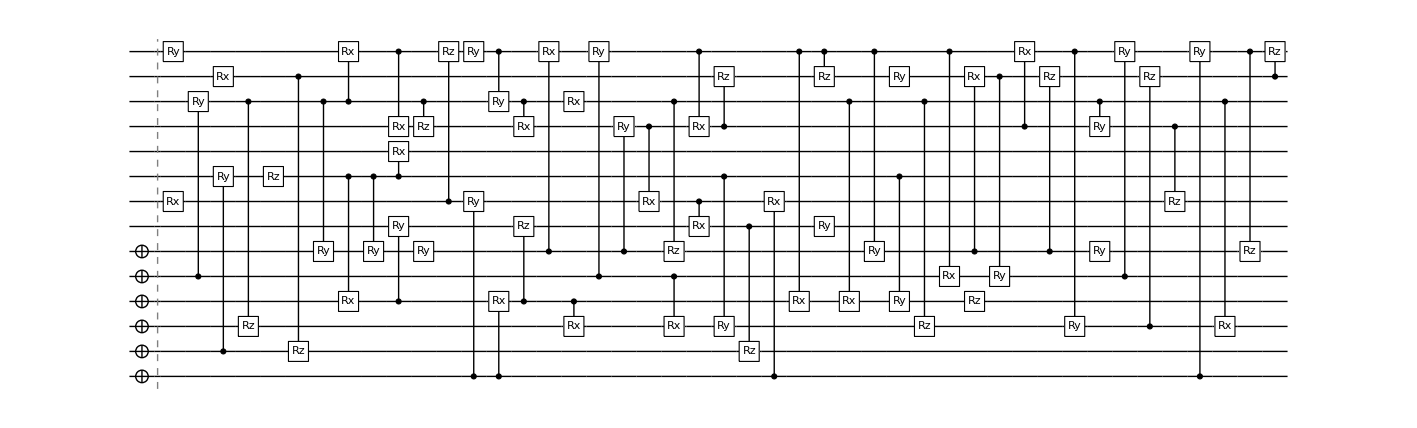

runtime=9.74601 hours

nansatz=62

nansatz/cycle={0,18,12,17,30,35,48,51,62,62}

<E>/cycle={-15.5603,-15.5626,-15.5656,-15.5684,-15.5768,-15.5805,-15.5894,-15.5936,-15.5941,-15.5941}

ϵ/cycle={0.0348688,0.0325329,0.0295464,0.0267989,0.0183443,0.0147048,0.00573059,0.00157584,0.00109684,0.00109684}

<E>=-15.5941

<E>-E_gs=0.00109684

<S^2>=0.000100868

<(4-N)^2>=0.000495711

Trial 3

Thu 13 Jan 2022 20:03:08GMT

target: -15.5952

@cycle1, fev:1250, <E>: -15.566313770608431 nansatz: 16 merged-smallθ-metric-bf-gmerged: {1, 1, 0, 79, 2}

@cycle2, fev:2793, <E>: -15.568834061036902 nansatz: 15 merged-smallθ-metric-bf-gmerged: {1, 1, 0, 160, 0}

@cycle3, fev:4675, <E>: -15.573384346058022 nansatz: 18 merged-smallθ-metric-bf-gmerged: {1, 1, 35, 202, 0}

@cycle4, fev:7516, <E>: -15.576093763294416 nansatz: 26 merged-smallθ-metric-bf-gmerged: {1, 1, 65, 244, 1}

@cycle5, pathetic result.

I'm slowing down. Number of gates is increased to 96 @cycle 5

@cycle5, fev:7950, <E>: -15.576093763294416 nansatz: 26 merged-smallθ-metric-bf-gmerged: {1, 1, 65, 244, 0}

@cycle6, fev:11045, <E>: -15.578921154839566 nansatz: 32 merged-smallθ-metric-bf-gmerged: {1, 1, 100, 299, 0}

@cycle7, fev:15779, <E>: -15.581601273231968 nansatz: 38 merged-smallθ-metric-bf-gmerged: {1, 1, 100, 389, 0}

@cycle8, fev:21756, <E>: -15.58195723070559 nansatz: 50 merged-smallθ-metric-bf-gmerged: {1, 1, 122, 449, 0}

@cycle9, pathetic result.

I'm slowing down. Number of gates is increased to 116 @cycle 9

@cycle9, fev:22775, <E>: -15.58195723070559 nansatz: 50 merged-smallθ-metric-bf-gmerged: {1, 1, 122, 449, 0}

@cycle10, fev:29731, <E>: -15.584927729881173 nansatz: 69 merged-smallθ-metric-bf-gmerged: {3, 1, 122, 544, 0}

@cycle11, fev:36944, <E>: -15.593052734260326 nansatz: 74 merged-smallθ-metric-bf-gmerged: {3, 1, 122, 655, 3}

@cycle12, fev:46424, <E>: -15.594030865939857 nansatz: 82 merged-smallθ-metric-bf-gmerged: {3, 1, 122, 762, 0}

@cycle13, fev:58021, <E>: -15.594314934330466 nansatz: 94 merged-smallθ-metric-bf-gmerged: {3, 1, 126, 862, 3}

@cycle14, fev:68351, <E>: -15.594506373132717 nansatz: 104 merged-smallθ-metric-bf-gmerged: {5, 2, 126, 963, 2}

@cycle15, pathetic result.

I'm slowing down. Number of gates is increased to 140 @cycle 15

@cycle15, fev:69747, <E>: -15.594506373132717 nansatz: 104 merged-smallθ-metric-bf-gmerged: {5, 2, 126, 963, 1}

@cycle16, pathetic result.

I'm slowing down. Number of gates is increased to 168 @cycle 16

@cycle16, fev:71322, <E>: -15.594506373132717 nansatz: 104 merged-smallθ-metric-bf-gmerged: {5, 2, 126, 963, 0}

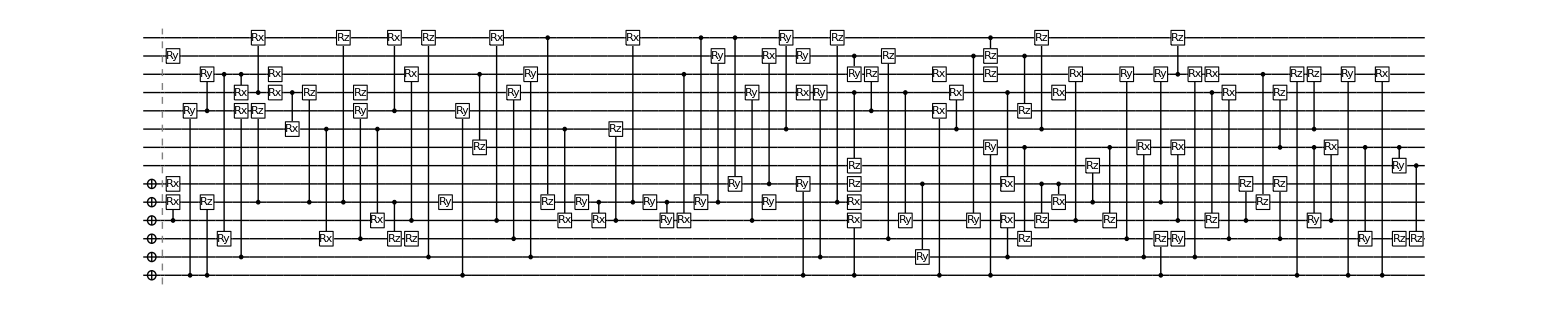

runtime=23.9796 hours

nansatz=104

nansatz/cycle={0,16,15,18,26,32,38,50,69,74,82,94,104,104}

<E>/cycle={-15.5603,-15.5663,-15.5688,-15.5734,-15.5761,-15.5789,-15.5816,-15.582,-15.5849,-15.5931,-15.594,-15.5943,-15.5945,-15.5945}

ϵ/cycle={0.0348688,0.0288617,0.0263415,0.0217912,0.0190817,0.0162544,0.0135742,0.0132183,0.0102478,0.00212278,0.00114465,0.000860577,0.000669138,0.000669138}

<E>=-15.5945

<E>-E_gs=0.000669138

<S^2>=0.000122824

<(4-N)^2>=0.000180564

Trial 4

Fri 14 Jan 2022 20:01:55GMT

target: -15.5952

@cycle1, fev:950, <E>: -15.566360589037753 nansatz: 8 merged-smallθ-metric-bf-gmerged: {0, 0, 45, 47, 4}

@cycle2, pathetic result.

I'm slowing down. Number of gates is increased to 96 @cycle 2

@cycle2, fev:1636, <E>: -15.566360589037753 nansatz: 8 merged-smallθ-metric-bf-gmerged: {0, 0, 45, 47, 0}

@cycle3, fev:3302, <E>: -15.568901100029441 nansatz: 14 merged-smallθ-metric-bf-gmerged: {0, 0, 45, 136, 0}

@cycle4, fev:5599, <E>: -15.572217476266854 nansatz: 16 merged-smallθ-metric-bf-gmerged: {0, 0, 45, 230, 0}

@cycle5, fev:8227, <E>: -15.576225930412386 nansatz: 25 merged-smallθ-metric-bf-gmerged: {0, 0, 45, 314, 0}

@cycle6, fev:11455, <E>: -15.579036036749006 nansatz: 31 merged-smallθ-metric-bf-gmerged: {0, 0, 84, 365, 0}

@cycle7, fev:15754, <E>: -15.581512103370363 nansatz: 47 merged-smallθ-metric-bf-gmerged: {0, 0, 84, 445, 0}

@cycle8, fev:21353, <E>: -15.581876204871678 nansatz: 47 merged-smallθ-metric-bf-gmerged: {0, 0, 84, 541, 0}

@cycle9, pathetic result.

I'm slowing down. Number of gates is increased to 116 @cycle 9

@cycle9, fev:22379, <E>: -15.581876204871678 nansatz: 47 merged-smallθ-metric-bf-gmerged: {0, 0, 84, 541, 1}

@cycle10, fev:26897, <E>: -15.589262538732196 nansatz: 49 merged-smallθ-metric-bf-gmerged: {0, 0, 131, 608, 2}

@cycle11, fev:32805, <E>: -15.593803842317847 nansatz: 59 merged-smallθ-metric-bf-gmerged: {0, 0, 170, 675, 0}

@cycle12, fev:41594, <E>: -15.594284416615384 nansatz: 77 merged-smallθ-metric-bf-gmerged: {1, 0, 170, 772, 2}

@cycle13, pathetic result.

I'm slowing down. Number of gates is increased to 140 @cycle 13

@cycle13, fev:42924, <E>: -15.594284416615384 nansatz: 77 merged-smallθ-metric-bf-gmerged: {1, 0, 170, 772, 0}

@cycle14, pathetic result.

I'm slowing down. Number of gates is increased to 168 @cycle 14

@cycle14, fev:44456, <E>: -15.594284416615384 nansatz: 77 merged-smallθ-metric-bf-gmerged: {1, 0, 170, 772, 0}

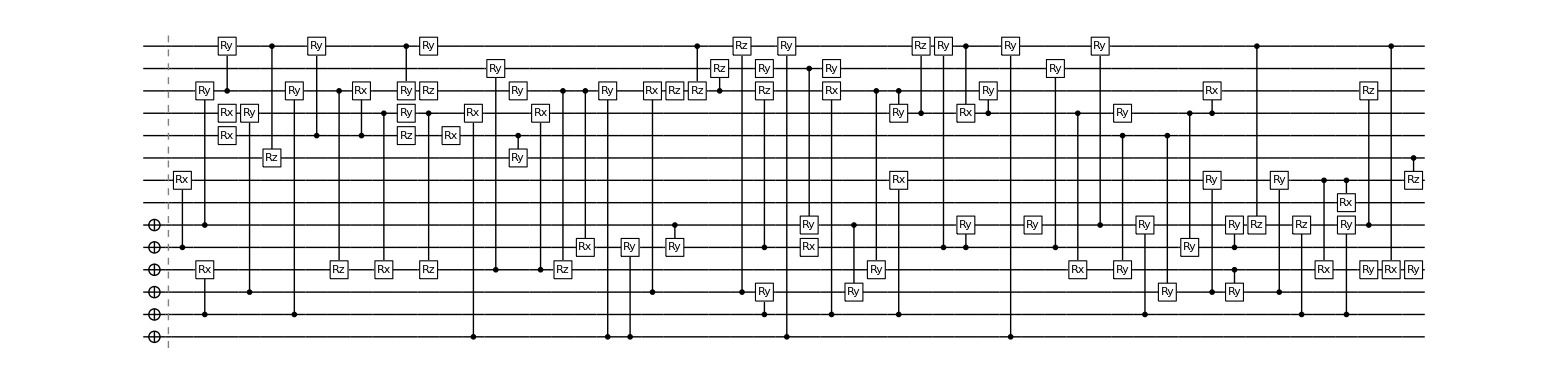

runtime=12.054 hours

nansatz=77

nansatz/cycle={0,8,14,16,25,31,47,47,49,59,77,77}

<E>/cycle={-15.5603,-15.5664,-15.5689,-15.5722,-15.5762,-15.579,-15.5815,-15.5819,-15.5893,-15.5938,-15.5943,-15.5943}

ϵ/cycle={0.0348688,0.0288149,0.0262744,0.022958,0.0189496,0.0161395,0.0136634,0.0132993,0.00591297,0.00137167,0.000891095,0.000891095}

<E>=-15.5943

<E>-E_gs=0.000891095

<S^2>=0.000130154

<(4-N)^2>=0.000352313

Trial 5

Sat 15 Jan 2022 08:05:10GMT

target: -15.5952

@cycle1, fev:1172, <E>: -15.566294101705513 nansatz: 11 merged-smallθ-metric-bf-gmerged: {0, 0, 0, 88, 0}

@cycle2, pathetic result.

I'm slowing down. Number of gates is increased to 96 @cycle 2

@cycle2, fev:1532, <E>: -15.566294101705513 nansatz: 11 merged-smallθ-metric-bf-gmerged: {0, 0, 0, 88, 0}

@cycle3, fev:3334, <E>: -15.570174635815857 nansatz: 15 merged-smallθ-metric-bf-gmerged: {0, 0, 50, 128, 2}

@cycle4, fev:5382, <E>: -15.573579585809433 nansatz: 21 merged-smallθ-metric-bf-gmerged: {0, 0, 50, 218, 1}

@cycle5, fev:7955, <E>: -15.575079393091663 nansatz: 22 merged-smallθ-metric-bf-gmerged: {0, 0, 50, 313, 0}

@cycle6, fev:10373, <E>: -15.577455714178615 nansatz: 25 merged-smallθ-metric-bf-gmerged: {0, 0, 50, 406, 1}

@cycle7, fev:14034, <E>: -15.57832855152978 nansatz: 27 merged-smallθ-metric-bf-gmerged: {0, 0, 50, 499, 0}

@cycle8, fev:17532, <E>: -15.578531804272577 nansatz: 35 merged-smallθ-metric-bf-gmerged: {1, 0, 50, 586, 0}

@cycle9, pathetic result.

I'm slowing down. Number of gates is increased to 116 @cycle 9

@cycle9, fev:18669, <E>: -15.578531804272577 nansatz: 35 merged-smallθ-metric-bf-gmerged: {1, 0, 50, 586, 0}

@cycle10, fev:23760, <E>: -15.583336600992201 nansatz: 38 merged-smallθ-metric-bf-gmerged: {1, 0, 50, 699, 2}

@cycle11, fev:29065, <E>: -15.588625473704282 nansatz: 43 merged-smallθ-metric-bf-gmerged: {1, 0, 76, 782, 2}

@cycle12, fev:34945, <E>: -15.593407685054423 nansatz: 57 merged-smallθ-metric-bf-gmerged: {1, 0, 76, 884, 5}

@cycle13, fev:44037, <E>: -15.594014982776397 nansatz: 69 merged-smallθ-metric-bf-gmerged: {4, 0, 111, 948, 1}

@cycle14, fev:51687, <E>: -15.594177918096824 nansatz: 75 merged-smallθ-metric-bf-gmerged: {4, 0, 165, 1004, 0}

@cycle15, pathetic result.

I'm slowing down. Number of gates is increased to 140 @cycle 15

@cycle15, fev:53053, <E>: -15.594177918096824 nansatz: 75 merged-smallθ-metric-bf-gmerged: {4, 0, 165, 1004, 2}

@cycle16, pathetic result.

I'm slowing down. Number of gates is increased to 168 @cycle 16

@cycle16, fev:54492, <E>: -15.594177918096824 nansatz: 75 merged-smallθ-metric-bf-gmerged: {4, 0, 165, 1004, 0}

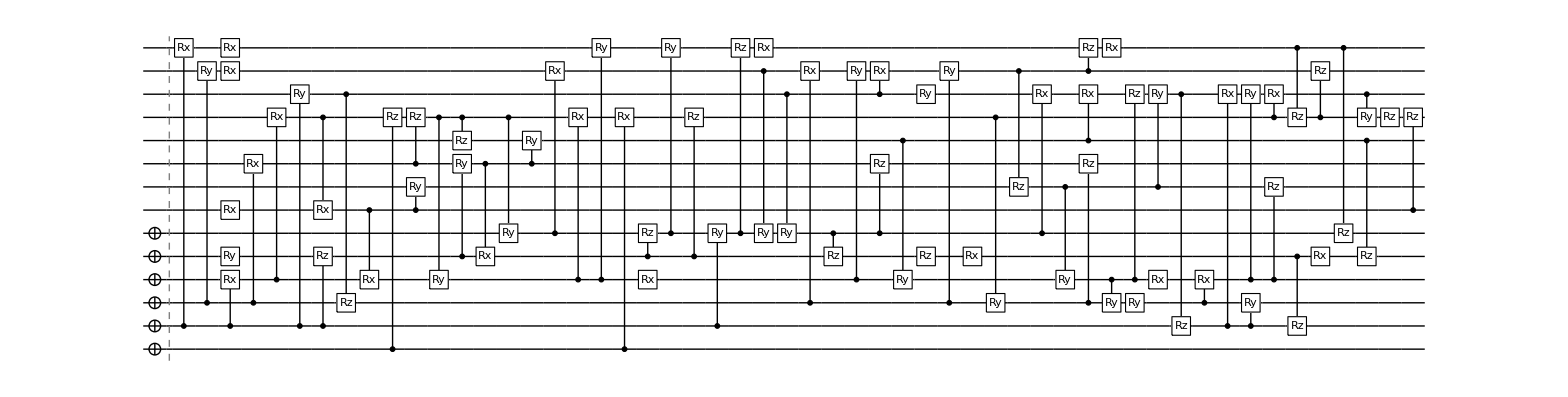

runtime=16.2131 hours

nansatz=75

nansatz/cycle={0,11,15,21,22,25,27,35,38,43,57,69,75,75}

<E>/cycle={-15.5603,-15.5663,-15.5702,-15.5736,-15.5751,-15.5775,-15.5783,-15.5785,-15.5833,-15.5886,-15.5934,-15.594,-15.5942,-15.5942}

ϵ/cycle={0.0348688,0.0288814,0.0250009,0.0215959,0.0200961,0.0177198,0.016847,0.0166437,0.0118389,0.00655004,0.00176783,0.00116053,0.000997593,0.000997593}

<E>=-15.5942

<E>-E_gs=0.000997593

<S^2>=0.0000793268

<(4-N)^2>=0.000249283

Trial 6

Sun 16 Jan 2022 00:17:57GMT

target: -15.5952

@cycle1, fev:1873, <E>: -15.566859461323359 nansatz: 21 merged-smallθ-metric-bf-gmerged: {0, 0, 0, 79, 4}

@cycle2, fev:4371, <E>: -15.57559636295063 nansatz: 22 merged-smallθ-metric-bf-gmerged: {0, 0, 17, 140, 0}

@cycle3, fev:7204, <E>: -15.576378058837067 nansatz: 27 merged-smallθ-metric-bf-gmerged: {0, 0, 51, 180, 0}

@cycle4, pathetic result.

I'm slowing down. Number of gates is increased to 96 @cycle 4

@cycle4, fev:7747, <E>: -15.576378058837067 nansatz: 27 merged-smallθ-metric-bf-gmerged: {0, 0, 51, 180, 0}

@cycle5, fev:11952, <E>: -15.576579306435027 nansatz: 44 merged-smallθ-metric-bf-gmerged: {0, 0, 83, 226, 4}

@cycle6, fev:17195, <E>: -15.578851196618414 nansatz: 42 merged-smallθ-metric-bf-gmerged: {0, 0, 107, 300, 1}

@cycle7, fev:22445, <E>: -15.581009569347486 nansatz: 43 merged-smallθ-metric-bf-gmerged: {1, 0, 122, 379, 3}

@cycle8, fev:26665, <E>: -15.581315905517478 nansatz: 47 merged-smallθ-metric-bf-gmerged: {2, 0, 152, 436, 0}

@cycle9, pathetic result.

I'm slowing down. Number of gates is increased to 116 @cycle 9

@cycle9, fev:27650, <E>: -15.581315905517478 nansatz: 47 merged-smallθ-metric-bf-gmerged: {2, 0, 152, 436, 1}

@cycle10, fev:31688, <E>: -15.59049259454967 nansatz: 35 merged-smallθ-metric-bf-gmerged: {2, 0, 180, 536, 1}

@cycle11, fev:36432, <E>: -15.591055728343832 nansatz: 48 merged-smallθ-metric-bf-gmerged: {2, 0, 215, 601, 2}

@cycle12, fev:42290, <E>: -15.591884782927744 nansatz: 55 merged-smallθ-metric-bf-gmerged: {2, 0, 255, 670, 0}

@cycle13, fev:50135, <E>: -15.592072987638764 nansatz: 74 merged-smallθ-metric-bf-gmerged: {4, 1, 255, 764, 0}

@cycle14, pathetic result.

I'm slowing down. Number of gates is increased to 140 @cycle 14

@cycle14, fev:51526, <E>: -15.592072987638764 nansatz: 74 merged-smallθ-metric-bf-gmerged: {4, 1, 255, 764, 0}

@cycle15, pathetic result.

I'm slowing down. Number of gates is increased to 168 @cycle 15

@cycle15, fev:53093, <E>: -15.592072987638764 nansatz: 74 merged-smallθ-metric-bf-gmerged: {4, 1, 255, 764, 0}

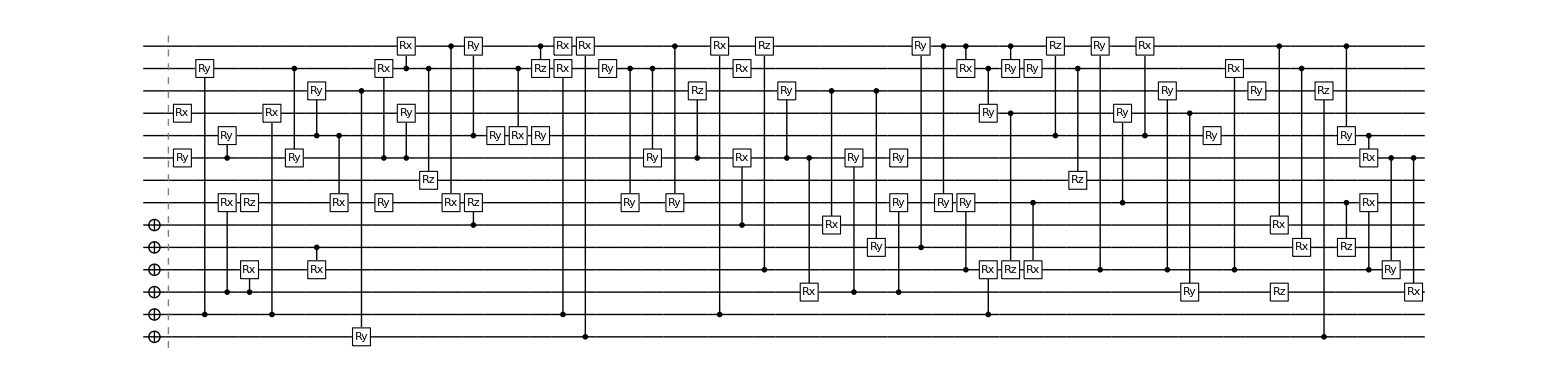

runtime=13.9089 hours

nansatz=74

nansatz/cycle={0,21,22,27,44,42,43,47,35,48,55,74,74}

<E>/cycle={-15.5603,-15.5669,-15.5756,-15.5764,-15.5766,-15.5789,-15.581,-15.5813,-15.5905,-15.5911,-15.5919,-15.5921,-15.5921}

ϵ/cycle={0.0348688,0.0283161,0.0195791,0.0187975,0.0185962,0.0163243,0.0141659,0.0138596,0.00468292,0.00411978,0.00329073,0.00310252,0.00310252}

<E>=-15.5921

<E>-E_gs=0.00310252

<S^2>=0.0000937429

<(4-N)^2>=0.000281766

Trial 7

Sun 16 Jan 2022 14:12:30GMT

target: -15.5952

@cycle1, fev:818, <E>: -15.563617353471233 nansatz: 8 merged-smallθ-metric-bf-gmerged: {0, 0, 0, 92, 0}

I'm slowing down. Number of gates is increased to 96 @cycle 2

@cycle2, fev:1229, <E>: -15.563617353471233 nansatz: 8 merged-smallθ-metric-bf-gmerged: {0, 0, 0, 92, 0}

@cycle3, fev:2785, <E>: -15.573338236900918 nansatz: 14 merged-smallθ-metric-bf-gmerged: {0, 0, 0, 182, 2}

@cycle4, fev:5306, <E>: -15.573751215680563 nansatz: 21 merged-smallθ-metric-bf-gmerged: {0, 0, 0, 271, 2}

@cycle5, pathetic result.

I'm slowing down. Number of gates is increased to 116 @cycle 5

@cycle5, fev:6124, <E>: -15.573751215680563 nansatz: 21 merged-smallθ-metric-bf-gmerged: {0, 0, 0, 271, 0}

@cycle6, fev:9960, <E>: -15.576897168909186 nansatz: 33 merged-smallθ-metric-bf-gmerged: {0, 0, 38, 337, 1}

@cycle7, fev:14862, <E>: -15.582389464292646 nansatz: 43 merged-smallθ-metric-bf-gmerged: {0, 0, 38, 443, 0}

@cycle8, fev:19524, <E>: -15.586030591410807 nansatz: 44 merged-smallθ-metric-bf-gmerged: {0, 0, 109, 486, 0}

@cycle9, fev:24919, <E>: -15.589846677226383 nansatz: 43 merged-smallθ-metric-bf-gmerged: {0, 0, 148, 564, 1}

@cycle10, fev:30524, <E>: -15.59168898310227 nansatz: 51 merged-smallθ-metric-bf-gmerged: {2, 1, 148, 669, 3}

@cycle11, fev:36316, <E>: -15.593901644117546 nansatz: 53 merged-smallθ-metric-bf-gmerged: {2, 1, 206, 725, 4}

@cycle12, fev:43396, <E>: -15.59410000356235 nansatz: 71 merged-smallθ-metric-bf-gmerged: {2, 1, 206, 822, 2}

@cycle13, pathetic result.

I'm slowing down. Number of gates is increased to 140 @cycle 13

@cycle13, fev:44724, <E>: -15.59410000356235 nansatz: 71 merged-smallθ-metric-bf-gmerged: {2, 1, 206, 822, 0}

@cycle14, pathetic result.

I'm slowing down. Number of gates is increased to 168 @cycle 14

@cycle14, fev:46389, <E>: -15.59410000356235 nansatz: 71 merged-smallθ-metric-bf-gmerged: {2, 1, 206, 822, 0}

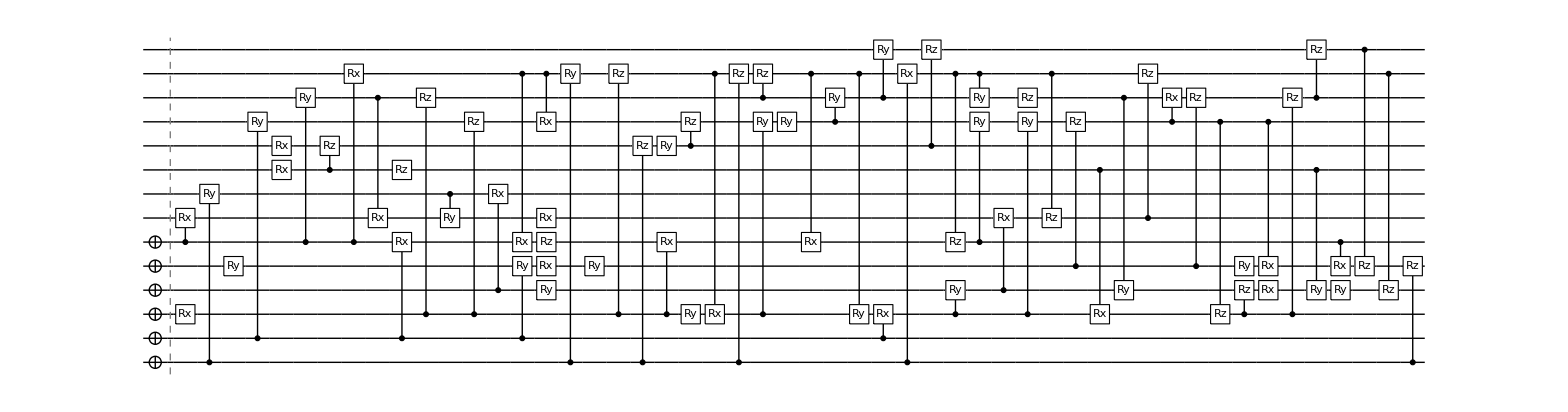

runtime=12.2177 hours

nansatz=71

nansatz/cycle={0,8,14,21,33,43,44,43,51,53,71,71}

<E>/cycle={-15.5603,-15.5636,-15.5733,-15.5738,-15.5769,-15.5824,-15.586,-15.5898,-15.5917,-15.5939,-15.5941,-15.5941}

ϵ/cycle={0.0348688,0.0315582,0.0218373,0.0214243,0.0182783,0.012786,0.00914492,0.00532883,0.00348653,0.00127387,0.00107551,0.00107551}

<E>=-15.5941

<E>-E_gs=0.00107551

<S^2>=0.000114265

<(4-N)^2>=0.0004604

Trial 8

Mon 17 Jan 2022 02:25:34GMT

target: -15.5952

@cycle1, fev:1492, <E>: -15.568308114474707 nansatz: 14 merged-smallθ-metric-bf-gmerged: {0, 0, 43, 43, 0}

@cycle2, fev:3112, <E>: -15.571374058647468 nansatz: 19 merged-smallθ-metric-bf-gmerged: {0, 0, 43, 118, 0}

@cycle3, fev:4881, <E>: -15.575826207466516 nansatz: 19 merged-smallθ-metric-bf-gmerged: {0, 0, 79, 162, 0}

@cycle4, pathetic result.

I'm slowing down. Number of gates is increased to 96 @cycle 4

@cycle4, fev:5610, <E>: -15.575826207466516 nansatz: 19 merged-smallθ-metric-bf-gmerged: {0, 0, 79, 162, 0}

@cycle5, fev:8743, <E>: -15.583877095110562 nansatz: 26 merged-smallθ-metric-bf-gmerged: {0, 0, 116, 214, 0}

@cycle6, fev:12596, <E>: -15.584049719855937 nansatz: 35 merged-smallθ-metric-bf-gmerged: {0, 0, 155, 261, 1}

@cycle7, fev:16910, <E>: -15.586457641219669 nansatz: 42 merged-smallθ-metric-bf-gmerged: {0, 0, 182, 322, 0}

@cycle8, fev:20793, <E>: -15.58916537736607 nansatz: 37 merged-smallθ-metric-bf-gmerged: {0, 0, 220, 384, 3}

@cycle9, fev:26762, <E>: -15.589391656348383 nansatz: 38 merged-smallθ-metric-bf-gmerged: {0, 0, 248, 450, 2}

@cycle10, fev:31095, <E>: -15.591696751855562 nansatz: 44 merged-smallθ-metric-bf-gmerged: {0, 0, 266, 522, 0}

@cycle11, fev:38610, <E>: -15.591856909211748 nansatz: 51 merged-smallθ-metric-bf-gmerged: {0, 0, 288, 587, 3}

@cycle12, fev:44093, <E>: -15.593881581422055 nansatz: 49 merged-smallθ-metric-bf-gmerged: {0, 0, 288, 685, 0}

@cycle13, fev:51078, <E>: -15.594096838912112 nansatz: 58 merged-smallθ-metric-bf-gmerged: {0, 0, 288, 770, 0}

@cycle14, pathetic result.

I'm slowing down. Number of gates is increased to 116 @cycle 14

@cycle14, fev:52232, <E>: -15.594096838912112 nansatz: 58 merged-smallθ-metric-bf-gmerged: {0, 0, 288, 770, 0}

@cycle15, pathetic result.

I'm slowing down. Number of gates is increased to 140 @cycle 15

@cycle15, fev:53414, <E>: -15.594096838912112 nansatz: 58 merged-smallθ-metric-bf-gmerged: {0, 0, 288, 770, 3}

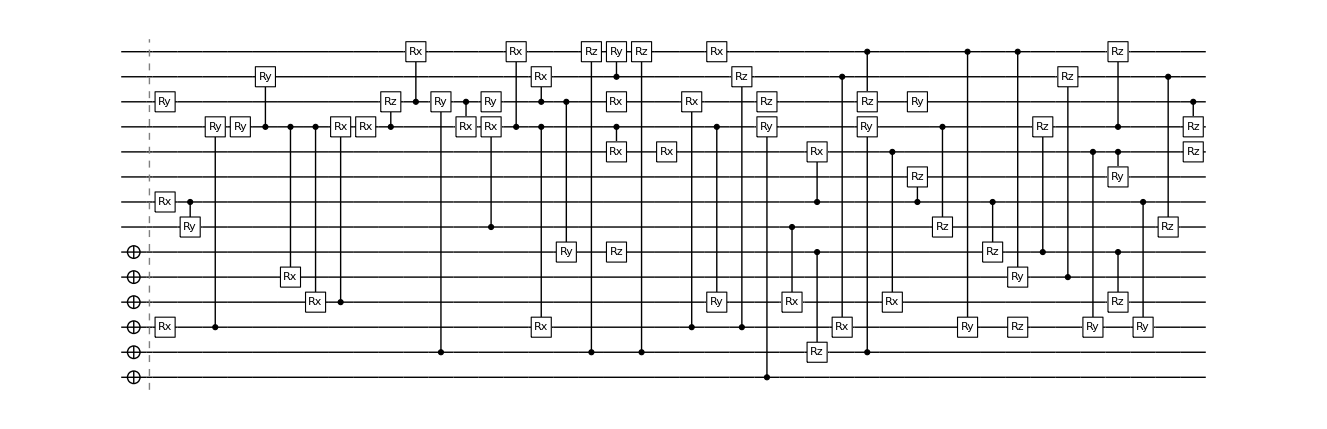

runtime=11.9658 hours

nansatz=58

nansatz/cycle={0,14,19,19,26,35,42,37,38,44,51,49,58,58}

<E>/cycle={-15.5603,-15.5683,-15.5714,-15.5758,-15.5839,-15.584,-15.5865,-15.5892,-15.5894,-15.5917,-15.5919,-15.5939,-15.5941,-15.5941}

ϵ/cycle={0.0348688,0.0268674,0.0238015,0.0193493,0.0112984,0.0111258,0.00871787,0.00601013,0.00578386,0.00347876,0.0033186,0.00129393,0.00107867,0.00107867}

<E>=-15.5941

<E>-E_gs=0.00107867

<S^2>=0.000229894

<(4-N)^2>=0.000218331

Trial 9

Mon 17 Jan 2022 14:23:31GMT

target: -15.5952

@cycle1, fev:1367, <E>: -15.566858270012158 nansatz: 13 merged-smallθ-metric-bf-gmerged: {0, 0, 0, 87, 0}

@cycle2, fev:2989, <E>: -15.570566097427042 nansatz: 19 merged-smallθ-metric-bf-gmerged: {0, 0, 0, 161, 0}

@cycle3, fev:6643, <E>: -15.572537371738793 nansatz: 18 merged-smallθ-metric-bf-gmerged: {0, 0, 1, 238, 0}

@cycle4, fev:9031, <E>: -15.576415921269874 nansatz: 21 merged-smallθ-metric-bf-gmerged: {0, 0, 32, 284, 0}

@cycle5, pathetic result.

I'm slowing down. Number of gates is increased to 96 @cycle 5

@cycle5, fev:9593, <E>: -15.576415921269874 nansatz: 21 merged-smallθ-metric-bf-gmerged: {0, 0, 32, 284, 0}

@cycle6, fev:12916, <E>: -15.578718337741865 nansatz: 33 merged-smallθ-metric-bf-gmerged: {0, 0, 32, 368, 0}

@cycle7, fev:18187, <E>: -15.579036826848123 nansatz: 44 merged-smallθ-metric-bf-gmerged: {0, 0, 32, 452, 0}

@cycle8, pathetic result.

I'm slowing down. Number of gates is increased to 116 @cycle 8

@cycle8, fev:19210, <E>: -15.579036826848123 nansatz: 44 merged-smallθ-metric-bf-gmerged: {0, 0, 32, 452, 3}

@cycle9, fev:24460, <E>: -15.581232178552405 nansatz: 40 merged-smallθ-metric-bf-gmerged: {0, 0, 32, 572, 0}

@cycle10, fev:29052, <E>: -15.589496861137551 nansatz: 46 merged-smallθ-metric-bf-gmerged: {0, 0, 86, 627, 2}

@cycle11, fev:35159, <E>: -15.592441882019196 nansatz: 54 merged-smallθ-metric-bf-gmerged: {0, 0, 112, 705, 4}

@cycle12, fev:41362, <E>: -15.59388635902956 nansatz: 55 merged-smallθ-metric-bf-gmerged: {0, 0, 139, 793, 0}

@cycle13, fev:49131, <E>: -15.594318955823137 nansatz: 90 merged-smallθ-metric-bf-gmerged: {0, 0, 167, 844, 1}

@cycle14, pathetic result.

I'm slowing down. Number of gates is increased to 140 @cycle 14

@cycle14, fev:50537, <E>: -15.594318955823137 nansatz: 90 merged-smallθ-metric-bf-gmerged: {0, 0, 167, 844, 4}

@cycle15, fev:62734, <E>: -15.594507282902423 nansatz: 114 merged-smallθ-metric-bf-gmerged: {1, 0, 207, 919, 2}

@cycle16, pathetic result.

I'm slowing down. Number of gates is increased to 168 @cycle 16

@cycle16, fev:64400, <E>: -15.594507282902423 nansatz: 114 merged-smallθ-metric-bf-gmerged: {1, 0, 207, 919, 0}

@cycle17, pathetic result.

I'm slowing down. Number of gates is increased to 202 @cycle 17

@cycle17, fev:66300, <E>: -15.594507282902423 nansatz: 114 merged-smallθ-metric-bf-gmerged: {1, 0, 207, 919, 0}

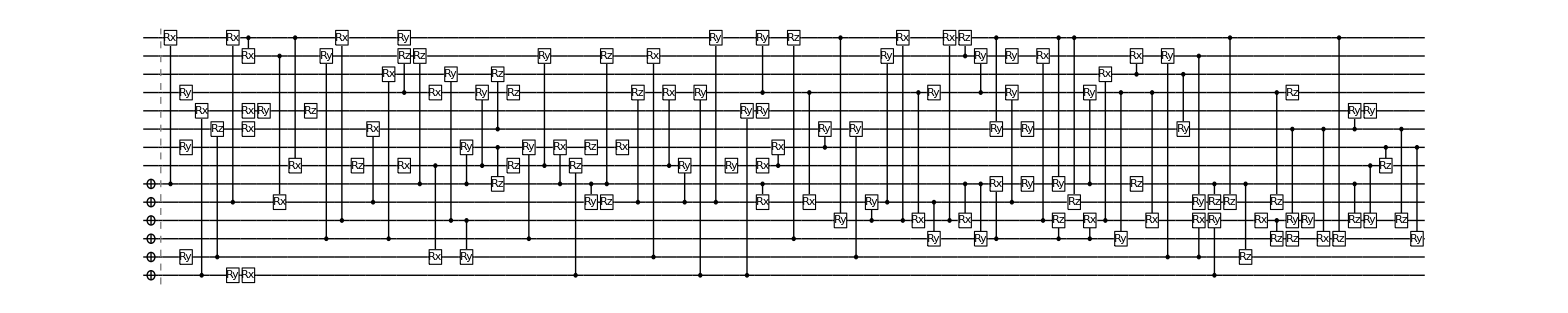

runtime=24.2627 hours

nansatz=114

nansatz/cycle={0,13,19,18,21,33,44,40,46,54,55,90,114,114}

<E>/cycle={-15.5603,-15.5669,-15.5706,-15.5725,-15.5764,-15.5787,-15.579,-15.5812,-15.5895,-15.5924,-15.5939,-15.5943,-15.5945,-15.5945}

ϵ/cycle={0.0348688,0.0283172,0.0246094,0.0226381,0.0187596,0.0164572,0.0161387,0.0139433,0.00567865,0.00273363,0.00128915,0.000856556,0.000668229,0.000668229}

<E>=-15.5945

<E>-E_gs=0.000668229

<S^2>=0.000194682

<(4-N)^2>=0.000321161

Trial 10

Tue 18 Jan 2022 14:39:17GMT

target: -15.5952

@cycle1, fev:901, <E>: -15.566360653312621 nansatz: 7 merged-smallθ-metric-bf-gmerged: {0, 0, 0, 93, 0}

@cycle2, fev:2244, <E>: -15.570560138732326 nansatz: 13 merged-smallθ-metric-bf-gmerged: {0, 0, 36, 129, 0}

@cycle3, fev:4247, <E>: -15.577329543777484 nansatz: 18 merged-smallθ-metric-bf-gmerged: {0, 0, 66, 172, 0}

@cycle4, pathetic result.

I'm slowing down. Number of gates is increased to 96 @cycle 4

@cycle4, fev:4742, <E>: -15.577329543777484 nansatz: 18 merged-smallθ-metric-bf-gmerged: {0, 0, 66, 172, 2}

@cycle5, pathetic result.

I'm slowing down. Number of gates is increased to 116 @cycle 5

@cycle5, fev:5698, <E>: -15.577329543777484 nansatz: 18 merged-smallθ-metric-bf-gmerged: {0, 0, 66, 172, 2}

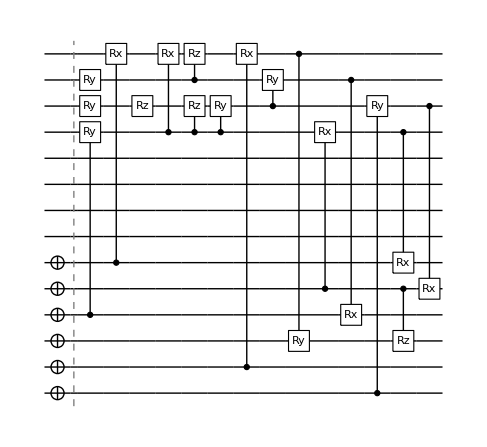

runtime=1.15547 hours

nansatz=18

nansatz/cycle={0,7,13,18,18}

<E>/cycle={-15.5603,-15.5664,-15.5706,-15.5773,-15.5773}

ϵ/cycle={0.0348688,0.0288149,0.0246154,0.017846,0.017846}

<E>=-15.5773

<E>-E_gs=0.017846

<S^2>=0.0121051

<(4-N)^2>=-1.77636×10^-15

{-15.5944,-15.5941,-15.5945,-15.5943,-15.5942,-15.5921,-15.5941,-15.5941,-15.5945,-15.5773}

```mathematica
results2={};
Table[
Print["Trial ",trial];
Print@Now;
Print["target: ",groundstate];
conf=DefaultConfig[14];
{timing,{Elist,ansatz,θvars,finmsg,ncycle,fev,aborted,cycleres,elim}}=AbsoluteTiming[VQEGS[14,hamiltonian,conf]];

Print@DrawCircuit[{conf["ansatzinit"],ansatz},14];
Print["runtime=",timing/3600," hours"];
Print["nansatz=",Length@ansatz];
Print["nansatz/cycle=",Length@#&/@cycleres["ansatz"]];
Print["<E>/cycle=",cycleres["E"]];
Print["ϵ/cycle=",cycleres["E"]-groundstate];
{ψ,ψwork}=CreateQuregs[14,2];
ApplyCircuit[ψ,Join[conf["ansatzinit"],ansatz]/.θvars];
ecur=CalcExpecPauliSum[ψ,hamiltonian,ψwork];
Print["<E>=",ecur];
Print["<E>-E_gs=",ecur-groundstate];
Print["<S^2>=",CalcExpecPauliSum[ψ,spin,ψwork]];
Print["<(4-N)^2>=",CalcExpecPauliSum[ψ,opnum,ψwork]];
DestroyAllQuregs[];
AppendTo[results2,{ansatz,θvars,cycleres,fev,aborted,elim}];
ecur
,{trial,10}]
```

## Results and analysis

```mathematica
results2={{{Subscript[Ry, 12][Subscript[θ, 1370]],Subscript[Ry, 8][Subscript[θ, 1296]],Subscript[C, 5][Subscript[Rx, 2][Subscript[θ, 1262]]],Subscript[C, 3][Subscript[Rx, 11][Subscript[θ, 1310]]],Subscript[C, 0][Subscript[Ry, 6][Subscript[θ, 1317]]],Subscript[Rx, 10][Subscript[θ, 1422]],Subscript[Rx, 4][Subscript[θ, 1358]],Subscript[Ry, 6][Subscript[θ, 1352]],Subscript[C, 1][Subscript[Rz, 8][Subscript[θ, 1306]]],Subscript[Rx, 5][Subscript[θ, 1034]],Subscript[C, 11][Subscript[Rz, 8][Subscript[θ, 1316]]],Subscript[C, 10][Subscript[Ry, 6][Subscript[θ, 1389]]],Subscript[C, 1][Subscript[Rz, 8][Subscript[θ, 1325]]],Subscript[C, 2][Subscript[Rz, 11][Subscript[θ, 1328]]],Subscript[C, 6][Subscript[Rx, 7][Subscript[θ, 6]]],Subscript[Ry, 8][Subscript[θ, 1331]],Subscript[Ry, 11][Subscript[θ, 1491]],Subscript[C, 2][Subscript[Ry, 4][Subscript[θ, 1373]]],Subscript[Rx, 8][Subscript[θ, 874]],Subscript[C, 0][Subscript[Ry, 2][Subscript[θ, 1053]]],Subscript[C, 1][Subscript[Rx, 8][Subscript[θ, 808]]],Subscript[C, 0][Subscript[Rx, 13][Subscript[θ, 1215]]],Subscript[C, 12][Subscript[Rx, 8][Subscript[θ, 1442]]],Subscript[C, 10][Subscript[Rx, 13][Subscript[θ, 1062]]],Subscript[C, 2][Subscript[Rz, 10][Subscript[θ, 1068]]],Subscript[C, 6][Subscript[Ry, 12][Subscript[θ, 1454]]],Subscript[Rx, 2][Subscript[θ, 1088]],Subscript[C, 10][Subscript[Ry, 11][Subscript[θ, 1102]]],Subscript[C, 10][Subscript[Rx, 8][Subscript[θ, 1408]]],Subscript[Rx, 11][Subscript[θ, 1119]],Subscript[C, 2][Subscript[Rx, 4][Subscript[θ, 1091]]],Subscript[C, 13][Subscript[Ry, 10][Subscript[θ, 852]]],Subscript[C, 12][Subscript[Rx, 8][Subscript[θ, 1397]]],Subscript[C, 3][Subscript[Rx, 2][Subscript[θ, 1096]]],Subscript[C, 11][Subscript[Rz, 9][Subscript[θ, 1195]]],Subscript[C, 10][Subscript[Rx, 4][Subscript[θ, 1460]]],Subscript[Rx, 13][Subscript[θ, 1211]],Subscript[Ry, 10][Subscript[θ, 1439]],Subscript[C, 13][Subscript[Rx, 12][Subscript[θ, 1484]]],Subscript[C, 10][Subscript[Ry, 2][Subscript[θ, 1377]]],Subscript[Rz, 12][Subscript[θ, 1415]],Subscript[C, 10][Subscript[Rz, 0][Subscript[θ, 1210]]],Subscript[C, 2][Subscript[Ry, 4][Subscript[θ, 1180]]],Subscript[C, 4][Subscript[Rx, 11][Subscript[θ, 850]]],Subscript[C, 5][Subscript[Rz, 2][Subscript[θ, 1109]]],Subscript[Ry, 5][Subscript[θ, 1121]],Subscript[C, 8][Subscript[Rx, 2][Subscript[θ, 814]]],Subscript[C, 11][Subscript[Ry, 10][Subscript[θ, 531]]],Subscript[C, 8][Subscript[Ry, 9][Subscript[θ, 742]]],Subscript[C, 10][Subscript[Rx, 13][Subscript[θ, 540]]],Subscript[C, 5][Subscript[Rx, 4][Subscript[θ, 1166]]],Subscript[C, 11][Subscript[Ry, 3][Subscript[θ, 493]]],Subscript[C, 6][Subscript[Rz, 13][Subscript[θ, 1379]]],Subscript[C, 4][Subscript[Rz, 11][Subscript[θ, 1383]]],Subscript[Rz, 8][Subscript[θ, 1483]],Subscript[C, 6][Subscript[Rx, 2][Subscript[θ, 62]]],Subscript[C, 1][Subscript[Ry, 13][Subscript[θ, 488]]],Subscript[C, 3][Subscript[Rz, 11][Subscript[θ, 1449]]],Subscript[C, 13][Subscript[Rz, 12][Subscript[θ, 1391]]],Subscript[C, 0][Subscript[Ry, 3][Subscript[θ, 1]]],Subscript[C, 10][Subscript[Ry, 11][Subscript[θ, 152]]],Subscript[C, 13][Subscript[Ry, 2][Subscript[θ, 373]]],Subscript[C, 4][Subscript[Rz, 0][Subscript[θ, 1232]]],Subscript[C, 10][Subscript[Ry, 5][Subscript[θ, 735]]],Subscript[C, 2][Subscript[Rz, 10][Subscript[θ, 1435]]],Subscript[C, 3][Subscript[Rz, 13][Subscript[θ, 1458]]],Subscript[C, 11][Subscript[Ry, 4][Subscript[θ, 407]]],Subscript[C, 9][Subscript[Rz, 13][Subscript[θ, 1420]]],Subscript[C, 2][Subscript[Ry, 3][Subscript[θ, 278]]],Subscript[C, 11][Subscript[Rz, 0][Subscript[θ, 1149]]],Subscript[C, 1][Subscript[Rz, 3][Subscript[θ, 1171]]],Subscript[C, 11][Subscript[Rz, 12][Subscript[θ, 329]]],Subscript[C, 0][Subscript[Rz, 3][Subscript[θ, 1492]]],Subscript[C, 1][Subscript[Rz, 13][Subscript[θ, 1213]]],Subscript[C, 5][Subscript[Rx, 12][Subscript[θ, 1145]]],Subscript[C, 0][Subscript[Rz, 4][Subscript[θ, 810]]],Subscript[C, 12][Subscript[Rz, 5][Subscript[θ, 337]]],Subscript[C, 3][Subscript[Ry, 4][Subscript[θ, 1447]]],Subscript[C, 13][Subscript[Ry, 12][Subscript[θ, 357]]],Subscript[C, 11][Subscript[Rz, 3][Subscript[θ, 978]]],Subscript[C, 13][Subscript[Rz, 6][Subscript[θ, 1018]]],Subscript[C, 12][Subscript[Rz, 5][Subscript[θ, 973]]],Subscript[C, 5][Subscript[Ry, 12][Subscript[θ, 974]]],Subscript[C, 13][Subscript[Rz, 12][Subscript[θ, 1470]]],Subscript[C, 13][Subscript[Rz, 3][Subscript[θ, 1187]]],Subscript[C, 12][Subscript[Rz, 11][Subscript[θ, 988]]],Subscript[C, 4][Subscript[Ry, 12][Subscript[θ, 991]]],Subscript[Rx, 12][Subscript[θ, 992]],Subscript[Ry, 12][Subscript[θ, 995]]},<|Subscript[θ, 1]->-3.141592653589793,Subscript[θ, 6]->-9.42477796076938,Subscript[θ, 62]->-3.1415930995750805,Subscript[θ, 152]->3.1415926535897936,Subscript[θ, 278]->3.141592653589793,Subscript[θ, 329]->-3.140798503609983,Subscript[θ, 337]->-6.609655162227329,Subscript[θ, 357]->-3.141393763432182,Subscript[θ, 373]->3.141590807572825,Subscript[θ, 407]->3.273968407755034,Subscript[θ, 488]->0.02046112353332144,Subscript[θ, 493]->9.42477796076938,Subscript[θ, 531]->4.74467441999841,Subscript[θ, 540]->-3.0620020773361927,Subscript[θ, 735]->-3.141592743054795,Subscript[θ, 742]->-3.141592653589793,Subscript[θ, 808]->2.5075868862929505,Subscript[θ, 810]->-3.23146222417211,Subscript[θ, 814]->3.1415922633607636,Subscript[θ, 850]->-3.0789397700641774,Subscript[θ, 852]->4.987661910415139,Subscript[θ, 874]->-2.0629101387507944,Subscript[θ, 973]->4.474862222459819,Subscript[θ, 974]->8.815113665818215,Subscript[θ, 978]->-4.635552842343203,Subscript[θ, 988]->-3.142302317555123,Subscript[θ, 991]->3.141643979702579,Subscript[θ, 992]->-3.041311663557584,Subscript[θ, 995]->1.570974289823863,Subscript[θ, 1018]->-2.193316034551253,Subscript[θ, 1034]->1.5707987863968833,Subscript[θ, 1053]->-1.5266991750074017,Subscript[θ, 1062]->3.1621078991264584,Subscript[θ, 1068]->-3.2048578278625235,Subscript[θ, 1088]->1.655112581272618,Subscript[θ, 1091]->3.238303736143235,Subscript[θ, 1096]->-3.1414154054902794,Subscript[θ, 1102]->2.9671869617219677,Subscript[θ, 1109]->3.1415383597898576,Subscript[θ, 1119]->3.237147538757731,Subscript[θ, 1121]->-1.5707987416840778,Subscript[θ, 1145]->3.14159251673619,Subscript[θ, 1149]->4.041684673400086,Subscript[θ, 1166]->0.13390707147944358,Subscript[θ, 1171]->-1.941096634874059,Subscript[θ, 1180]->-0.23574199950685212,Subscript[θ, 1187]->-2.9930624418290592,Subscript[θ, 1195]->-3.2943272332499727,Subscript[θ, 1210]->-4.925639972816706,Subscript[θ, 1211]->0.26324529784173867,Subscript[θ, 1213]->2.5646623075800483,Subscript[θ, 1215]->0.257002616193244,Subscript[θ, 1232]->4.680534102279282,Subscript[θ, 1262]->0.12958927835911901,Subscript[θ, 1296]->-2.1977774135737764,Subscript[θ, 1306]->-1.1277804732879895,Subscript[θ, 1310]->-0.00904280098881528,Subscript[θ, 1316]->-3.602436552642207,Subscript[θ, 1317]->2.0459511671482744,Subscript[θ, 1325]->-1.5929259069487092,Subscript[θ, 1328]->5.785591152584366,Subscript[θ, 1331]->-2.2332672953429737,Subscript[θ, 1352]->-1.9390217237859566,Subscript[θ, 1358]->0.014381390627824515,Subscript[θ, 1370]->1.5706050870016874,Subscript[θ, 1373]->0.24361700750631748,Subscript[θ, 1377]->-0.164960649647917,Subscript[θ, 1379]->-1.043163303929059,Subscript[θ, 1383]->1.373271221575789,Subscript[θ, 1389]->-0.13062176487275343,Subscript[θ, 1391]->1.8079924973275912,Subscript[θ, 1397]->3.0397690832151434,Subscript[θ, 1408]->-0.13044898327056845,Subscript[θ, 1415]->0.5030504735426199,Subscript[θ, 1420]->-2.4110991702479065,Subscript[θ, 1422]->-0.14596930798905142,Subscript[θ, 1435]->-1.6489127049919738,Subscript[θ, 1439]->0.04481358636389938,Subscript[θ, 1442]->-3.0397569971943867,Subscript[θ, 1447]->0.1281824771276363,Subscript[θ, 1449]->-1.0274843560480096,Subscript[θ, 1454]->-0.10642768440520887,Subscript[θ, 1458]->0.9485547440720792,Subscript[θ, 1460]->-0.04749707179774749,Subscript[θ, 1470]->3.1405706340596176,Subscript[θ, 1483]->-0.7581709388805791,Subscript[θ, 1484]->0.3873342217008966,Subscript[θ, 1491]->-0.1668926287720035,Subscript[θ, 1492]->-1.5030763668509088|>,<|"ansatz"->{{},{Subscript[C, 0][Subscript[Ry, 3][Subscript[θ, 1]]],Subscript[Ry, 6][Subscript[θ, 3]],Subscript[C, 6][Subscript[Rx, 7][Subscript[θ, 6]]],Subscript[C, 6][Subscript[Rx, 2][Subscript[θ, 62]]],Subscript[C, 2][Subscript[Ry, 3][Subscript[θ, 79]]]},{Subscript[C, 0][Subscript[Ry, 3][Subscript[θ, 1]]],Subscript[Ry, 6][Subscript[θ, 3]],Subscript[Rx, 10][Subscript[θ, 176]],Subscript[C, 10][Subscript[Ry, 11][Subscript[θ, 152]]],Subscript[C, 6][Subscript[Rx, 7][Subscript[θ, 6]]],Subscript[C, 11][Subscript[Ry, 4][Subscript[θ, 117]]],Subscript[C, 6][Subscript[Rx, 2][Subscript[θ, 62]]],Subscript[C, 2][Subscript[Ry, 3][Subscript[θ, 79]]],Subscript[C, 0][Subscript[Rz, 4][Subscript[θ, 126]]],Subscript[C, 11][Subscript[Ry, 5][Subscript[θ, 134]]]},{Subscript[C, 0][Subscript[Ry, 3][Subscript[θ, 1]]],Subscript[Ry, 6][Subscript[θ, 3]],Subscript[Rx, 10][Subscript[θ, 176]],Subscript[C, 10][Subscript[Ry, 11][Subscript[θ, 152]]],Subscript[C, 6][Subscript[Rx, 7][Subscript[θ, 6]]],Subscript[C, 11][Subscript[Ry, 4][Subscript[θ, 117]]],Subscript[C, 6][Subscript[Rx, 2][Subscript[θ, 62]]],Subscript[C, 2][Subscript[Ry, 3][Subscript[θ, 79]]],Subscript[C, 11][Subscript[Ry, 5][Subscript[θ, 134]]],Subscript[C, 4][Subscript[Ry, 3][Subscript[θ, 192]]],Subscript[C, 0][Subscript[Ry, 11][Subscript[θ, 203]]],Subscript[C, 3][Subscript[Rz, 11][Subscript[θ, 209]]],Subscript[C, 3][Subscript[Rz, 13][Subscript[θ, 222]]],Subscript[C, 5][Subscript[Ry, 3][Subscript[θ, 254]]],Subscript[C, 10][Subscript[Rz, 3][Subscript[θ, 258]]]},{Subscript[Rx, 12][Subscript[θ, 312]],Subscript[C, 0][Subscript[Ry, 3][Subscript[θ, 1]]],Subscript[Ry, 11][Subscript[θ, 340]],Subscript[Rx, 10][Subscript[θ, 310]],Subscript[C, 4][Subscript[Rx, 6][Subscript[θ, 292]]],Subscript[C, 11][Subscript[Rx, 5][Subscript[θ, 264]]],Subscript[C, 12][Subscript[Rz, 2][Subscript[θ, 289]]],Subscript[C, 6][Subscript[Rx, 7][Subscript[θ, 6]]],Subscript[C, 10][Subscript[Ry, 11][Subscript[θ, 152]]],Subscript[C, 6][Subscript[Rx, 2][Subscript[θ, 62]]],Subscript[C, 7][Subscript[Rz, 0][Subscript[θ, 281]]],Subscript[C, 11][Subscript[Ry, 4][Subscript[θ, 117]]],Subscript[C, 2][Subscript[Ry, 3][Subscript[θ, 79]]],Subscript[C, 11][Subscript[Ry, 5][Subscript[θ, 134]]],Subscript[C, 11][Subscript[Rz, 12][Subscript[θ, 329]]],Subscript[C, 12][Subscript[Rz, 5][Subscript[θ, 337]]],Subscript[C, 3][Subscript[Rz, 11][Subscript[θ, 209]]],Subscript[C, 0][Subscript[Rx, 12][Subscript[θ, 307]]],Subscript[C, 3][Subscript[Rz, 13][Subscript[θ, 222]]],Subscript[C, 11][Subscript[Rz, 13][Subscript[θ, 300]]],Subscript[C, 10][Subscript[Rz, 3][Subscript[θ, 258]]],Subscript[C, 2][Subscript[Ry, 3][Subscript[θ, 278]]]},{Subscript[Rx, 12][Subscript[θ, 312]],Subscript[C, 0][Subscript[Ry, 3][Subscript[θ, 1]]],Subscript[C, 5][Subscript[Ry, 11][Subscript[θ, 366]]],Subscript[Ry, 10][Subscript[θ, 396]],Subscript[C, 4][Subscript[Rx, 6][Subscript[θ, 292]]],Subscript[C, 5][Subscript[Ry, 13][Subscript[θ, 391]]],Subscript[C, 6][Subscript[Rx, 7][Subscript[θ, 6]]],Subscript[C, 12][Subscript[Rz, 2][Subscript[θ, 289]]],Subscript[C, 11][Subscript[Rx, 5][Subscript[θ, 264]]],Subscript[C, 6][Subscript[Rx, 2][Subscript[θ, 62]]],Subscript[C, 10][Subscript[Ry, 11][Subscript[θ, 152]]],Subscript[C, 13][Subscript[Ry, 2][Subscript[θ, 373]]],Subscript[C, 2][Subscript[Ry, 3][Subscript[θ, 79]]],Subscript[C, 11][Subscript[Ry, 5][Subscript[θ, 134]]],Subscript[C, 11][Subscript[Ry, 4][Subscript[θ, 407]]],Subscript[C, 1][Subscript[Rz, 2][Subscript[θ, 414]]],Subscript[C, 11][Subscript[Rz, 12][Subscript[θ, 329]]],Subscript[C, 12][Subscript[Rz, 5][Subscript[θ, 337]]],Subscript[C, 3][Subscript[Rz, 11][Subscript[θ, 209]]],Subscript[C, 0][Subscript[Rx, 12][Subscript[θ, 307]]],Subscript[C, 5][Subscript[Rz, 3][Subscript[θ, 393]]],Subscript[C, 3][Subscript[Rz, 10][Subscript[θ, 377]]],Subscript[C, 3][Subscript[Rz, 13][Subscript[θ, 222]]],Subscript[C, 10][Subscript[Rz, 0][Subscript[θ, 380]]],Subscript[C, 11][Subscript[Rz, 13][Subscript[θ, 300]]],Subscript[C, 13][Subscript[Rz, 2][Subscript[θ, 379]]],Subscript[C, 13][Subscript[Ry, 12][Subscript[θ, 357]]],Subscript[C, 2][Subscript[Ry, 3][Subscript[θ, 278]]]},{Subscript[C, 0][Subscript[Rx, 13][Subscript[θ, 439]]],Subscript[Rx, 4][Subscript[θ, 434]],Subscript[C, 5][Subscript[Rx, 6][Subscript[θ, 481]]],Subscript[C, 2][Subscript[Rx, 10][Subscript[θ, 442]]],Subscript[C, 4][Subscript[Ry, 11][Subscript[θ, 470]]],Subscript[C, 13][Subscript[Rz, 10][Subscript[θ, 469]]],Subscript[C, 4][Subscript[Ry, 12][Subscript[θ, 482]]],Subscript[C, 11][Subscript[Ry, 3][Subscript[θ, 493]]],Subscript[C, 1][Subscript[Ry, 13][Subscript[θ, 488]]],Subscript[C, 10][Subscript[Rz, 7][Subscript[θ, 494]]],Subscript[C, 4][Subscript[Rx, 6][Subscript[θ, 292]]],Subscript[C, 0][Subscript[Ry, 3][Subscript[θ, 1]]],Subscript[C, 11][Subscript[Ry, 10][Subscript[θ, 495]]],Subscript[C, 6][Subscript[Rx, 7][Subscript[θ, 6]]],Subscript[C, 11][Subscript[Rx, 5][Subscript[θ, 264]]],Subscript[C, 6][Subscript[Rx, 2][Subscript[θ, 62]]],Subscript[C, 10][Subscript[Ry, 11][Subscript[θ, 152]]],Subscript[C, 13][Subscript[Ry, 2][Subscript[θ, 373]]],Subscript[C, 11][Subscript[Ry, 5][Subscript[θ, 134]]],Subscript[C, 1][Subscript[Rz, 2][Subscript[θ, 414]]],Subscript[C, 11][Subscript[Ry, 4][Subscript[θ, 407]]],Subscript[C, 11][Subscript[Rz, 12][Subscript[θ, 329]]],Subscript[C, 12][Subscript[Rz, 5][Subscript[θ, 337]]],Subscript[C, 11][Subscript[Rz, 13][Subscript[θ, 300]]],Subscript[C, 0][Subscript[Rx, 12][Subscript[θ, 307]]],Subscript[C, 5][Subscript[Rz, 3][Subscript[θ, 393]]],Subscript[C, 13][Subscript[Rz, 2][Subscript[θ, 379]]],Subscript[C, 10][Subscript[Rz, 0][Subscript[θ, 380]]],Subscript[C, 13][Subscript[Ry, 12][Subscript[θ, 357]]],Subscript[C, 2][Subscript[Ry, 3][Subscript[θ, 278]]]},{Subscript[Rx, 11][Subscript[θ, 530]],Subscript[C, 4][Subscript[Ry, 12][Subscript[θ, 482]]],Subscript[C, 11][Subscript[Ry, 10][Subscript[θ, 531]]],Subscript[C, 4][Subscript[Rx, 6][Subscript[θ, 292]]],Subscript[C, 10][Subscript[Rx, 13][Subscript[θ, 540]]],Subscript[C, 11][Subscript[Ry, 3][Subscript[θ, 493]]],Subscript[C, 6][Subscript[Rx, 7][Subscript[θ, 6]]],Subscript[C, 2][Subscript[Rx, 10][Subscript[θ, 442]]],Subscript[C, 0][Subscript[Ry, 3][Subscript[θ, 1]]],Subscript[C, 11][Subscript[Rx, 5][Subscript[θ, 264]]],Subscript[C, 1][Subscript[Ry, 13][Subscript[θ, 488]]],Subscript[C, 6][Subscript[Rx, 2][Subscript[θ, 62]]],Subscript[C, 10][Subscript[Ry, 11][Subscript[θ, 152]]],Subscript[C, 13][Subscript[Ry, 2][Subscript[θ, 373]]],Subscript[C, 11][Subscript[Ry, 5][Subscript[θ, 134]]],Subscript[C, 1][Subscript[Rz, 2][Subscript[θ, 414]]],Subscript[C, 11][Subscript[Ry, 4][Subscript[θ, 407]]],Subscript[C, 11][Subscript[Rz, 12][Subscript[θ, 329]]],Subscript[C, 13][Subscript[Rz, 2][Subscript[θ, 379]]],Subscript[C, 12][Subscript[Rz, 5][Subscript[θ, 337]]],Subscript[C, 2][Subscript[Ry, 3][Subscript[θ, 278]]],Subscript[C, 0][Subscript[Rx, 12][Subscript[θ, 307]]],Subscript[C, 13][Subscript[Ry, 12][Subscript[θ, 357]]]},{Subscript[C, 3][Subscript[Rx, 4][Subscript[θ, 622]]],Subscript[C, 2][Subscript[Ry, 6][Subscript[θ, 624]]],Subscript[C, 0][Subscript[Ry, 13][Subscript[θ, 621]]],Subscript[C, 4][Subscript[Rz, 5][Subscript[θ, 623]]],Subscript[C, 6][Subscript[Rx, 11][Subscript[θ, 638]]],Subscript[C, 3][Subscript[Rx, 13][Subscript[θ, 632]]],Subscript[C, 4][Subscript[Rz, 6][Subscript[θ, 641]]],Subscript[Rx, 11][Subscript[θ, 530]],Subscript[Ry, 6][Subscript[θ, 645]],Subscript[C, 11][Subscript[Ry, 10][Subscript[θ, 531]]],Subscript[C, 6][Subscript[Ry, 4][Subscript[θ, 651]]],Subscript[C, 11][Subscript[Ry, 3][Subscript[θ, 493]]],Subscript[C, 13][Subscript[Rz, 6][Subscript[θ, 656]]],Subscript[C, 4][Subscript[Ry, 12][Subscript[θ, 482]]],Subscript[C, 0][Subscript[Ry, 3][Subscript[θ, 1]]],Subscript[C, 11][Subscript[Rx, 5][Subscript[θ, 264]]],Subscript[C, 4][Subscript[Rx, 6][Subscript[θ, 292]]],Subscript[C, 10][Subscript[Rx, 13][Subscript[θ, 540]]],Subscript[C, 6][Subscript[Rx, 7][Subscript[θ, 6]]],Subscript[C, 2][Subscript[Rx, 10][Subscript[θ, 442]]],Subscript[C, 1][Subscript[Ry, 13][Subscript[θ, 488]]],Subscript[C, 6][Subscript[Rx, 2][Subscript[θ, 62]]],Subscript[C, 10][Subscript[Ry, 11][Subscript[θ, 152]]],Subscript[C, 13][Subscript[Ry, 2][Subscript[θ, 373]]],Subscript[C, 11][Subscript[Ry, 5][Subscript[θ, 134]]],Subscript[C, 1][Subscript[Rz, 2][Subscript[θ, 414]]],Subscript[C, 11][Subscript[Ry, 4][Subscript[θ, 407]]],Subscript[C, 11][Subscript[Rz, 12][Subscript[θ, 329]]],Subscript[C, 13][Subscript[Rz, 2][Subscript[θ, 379]]],Subscript[C, 12][Subscript[Rz, 5][Subscript[θ, 337]]],Subscript[C, 2][Subscript[Ry, 3][Subscript[θ, 278]]],Subscript[C, 0][Subscript[Rx, 12][Subscript[θ, 307]]],Subscript[C, 13][Subscript[Ry, 12][Subscript[θ, 357]]]},{Subscript[C, 3][Subscript[Rx, 4][Subscript[θ, 622]]],Subscript[C, 2][Subscript[Ry, 6][Subscript[θ, 624]]],Subscript[C, 3][Subscript[Rx, 13][Subscript[θ, 632]]],Subscript[C, 6][Subscript[Rx, 11][Subscript[θ, 638]]],Subscript[C, 4][Subscript[Rz, 6][Subscript[θ, 641]]],Subscript[Ry, 6][Subscript[θ, 645]],Subscript[C, 11][Subscript[Rx, 4][Subscript[θ, 740]]],Subscript[C, 11][Subscript[Ry, 10][Subscript[θ, 531]]],Subscript[C, 6][Subscript[Ry, 4][Subscript[θ, 651]]],Subscript[C, 11][Subscript[Ry, 3][Subscript[θ, 493]]],Subscript[C, 13][Subscript[Rz, 6][Subscript[θ, 656]]],Subscript[C, 10][Subscript[Rx, 4][Subscript[θ, 737]]],Subscript[C, 0][Subscript[Ry, 3][Subscript[θ, 1]]],Subscript[Ry, 6][Subscript[θ, 733]],Subscript[C, 4][Subscript[Ry, 12][Subscript[θ, 482]]],Subscript[C, 10][Subscript[Rx, 13][Subscript[θ, 540]]],Subscript[C, 6][Subscript[Rx, 7][Subscript[θ, 6]]],Subscript[C, 1][Subscript[Ry, 13][Subscript[θ, 488]]],Subscript[C, 2][Subscript[Rx, 10][Subscript[θ, 442]]],Subscript[C, 0][Subscript[Ry, 12][Subscript[θ, 732]]],Subscript[C, 11][Subscript[Rz, 7][Subscript[θ, 716]]],Subscript[C, 6][Subscript[Rx, 2][Subscript[θ, 62]]],Subscript[C, 10][Subscript[Ry, 11][Subscript[θ, 152]]],Subscript[C, 13][Subscript[Ry, 2][Subscript[θ, 373]]],Subscript[C, 6][Subscript[Rz, 9][Subscript[θ, 673]]],Subscript[C, 5][Subscript[Rz, 11][Subscript[θ, 717]]],Subscript[C, 1][Subscript[Rz, 2][Subscript[θ, 414]]],Subscript[C, 10][Subscript[Rz, 5][Subscript[θ, 696]]],Subscript[C, 11][Subscript[Ry, 4][Subscript[θ, 407]]],Subscript[C, 13][Subscript[Rz, 2][Subscript[θ, 379]]],Subscript[C, 0][Subscript[Rz, 11][Subscript[θ, 682]]],Subscript[C, 2][Subscript[Ry, 3][Subscript[θ, 278]]],Subscript[C, 10][Subscript[Ry, 5][Subscript[θ, 735]]],Subscript[C, 11][Subscript[Rz, 12][Subscript[θ, 329]]],Subscript[C, 12][Subscript[Rz, 5][Subscript[θ, 337]]],Subscript[C, 0][Subscript[Rx, 12][Subscript[θ, 307]]],Subscript[C, 13][Subscript[Ry, 12][Subscript[θ, 357]]]},{Subscript[C, 1][Subscript[Rx, 8][Subscript[θ, 808]]],Subscript[C, 2][Subscript[Ry, 6][Subscript[θ, 624]]],Subscript[C, 6][Subscript[Rx, 11][Subscript[θ, 638]]],Subscript[C, 8][Subscript[Rx, 2][Subscript[θ, 814]]],Subscript[C, 11][Subscript[Ry, 10][Subscript[θ, 531]]],Subscript[C, 6][Subscript[Ry, 4][Subscript[θ, 651]]],Subscript[C, 8][Subscript[Ry, 9][Subscript[θ, 742]]],Subscript[C, 11][Subscript[Ry, 3][Subscript[θ, 493]]],Subscript[Ry, 6][Subscript[θ, 733]],Subscript[C, 4][Subscript[Ry, 12][Subscript[θ, 482]]],Subscript[C, 10][Subscript[Rx, 13][Subscript[θ, 540]]],Subscript[C, 0][Subscript[Ry, 3][Subscript[θ, 1]]],Subscript[C, 6][Subscript[Rx, 7][Subscript[θ, 6]]],Subscript[C, 1][Subscript[Ry, 13][Subscript[θ, 488]]],Subscript[C, 2][Subscript[Rx, 10][Subscript[θ, 442]]],Subscript[C, 6][Subscript[Rx, 2][Subscript[θ, 62]]],Subscript[C, 10][Subscript[Ry, 11][Subscript[θ, 152]]],Subscript[C, 13][Subscript[Ry, 2][Subscript[θ, 373]]],Subscript[C, 11][Subscript[Ry, 4][Subscript[θ, 407]]],Subscript[C, 10][Subscript[Ry, 5][Subscript[θ, 735]]],Subscript[C, 2][Subscript[Ry, 3][Subscript[θ, 278]]],Subscript[C, 11][Subscript[Rz, 12][Subscript[θ, 329]]],Subscript[C, 12][Subscript[Rz, 5][Subscript[θ, 337]]],Subscript[C, 10][Subscript[Rz, 11][Subscript[θ, 747]]],Subscript[C, 0][Subscript[Rx, 12][Subscript[θ, 307]]],Subscript[C, 0][Subscript[Rz, 4][Subscript[θ, 810]]],Subscript[C, 13][Subscript[Ry, 12][Subscript[θ, 357]]]},{Subscript[C, 1][Subscript[Rx, 13][Subscript[θ, 847]]],Subscript[C, 4][Subscript[Rx, 11][Subscript[θ, 850]]],Subscript[Rx, 8][Subscript[θ, 874]],Subscript[Rx, 12][Subscript[θ, 890]],Subscript[C, 13][Subscript[Ry, 10][Subscript[θ, 852]]],Subscript[C, 11][Subscript[Ry, 4][Subscript[θ, 884]]],Subscript[C, 1][Subscript[Ry, 12][Subscript[θ, 894]]],Subscript[C, 3][Subscript[Rz, 13][Subscript[θ, 853]]],Subscript[C, 10][Subscript[Rz, 8][Subscript[θ, 904]]],Subscript[C, 13][Subscript[Rx, 6][Subscript[θ, 910]]],Subscript[C, 8][Subscript[Ry, 6][Subscript[θ, 912]]],Subscript[Rz, 13][Subscript[θ, 919]],Subscript[C, 8][Subscript[Ry, 4][Subscript[θ, 918]]],Subscript[C, 2][Subscript[Ry, 6][Subscript[θ, 624]]],Subscript[Rx, 13][Subscript[θ, 932]],Subscript[C, 1][Subscript[Rx, 8][Subscript[θ, 808]]],Subscript[C, 6][Subscript[Rx, 11][Subscript[θ, 638]]],Subscript[C, 8][Subscript[Rx, 2][Subscript[θ, 814]]],Subscript[C, 11][Subscript[Ry, 10][Subscript[θ, 531]]],Subscript[C, 6][Subscript[Ry, 4][Subscript[θ, 651]]],Subscript[C, 8][Subscript[Ry, 9][Subscript[θ, 742]]],Subscript[C, 11][Subscript[Ry, 3][Subscript[θ, 493]]],Subscript[C, 4][Subscript[Ry, 12][Subscript[θ, 482]]],Subscript[C, 10][Subscript[Rx, 13][Subscript[θ, 540]]],Subscript[C, 6][Subscript[Rx, 7][Subscript[θ, 6]]],Subscript[C, 0][Subscript[Ry, 3][Subscript[θ, 1]]],Subscript[C, 1][Subscript[Ry, 13][Subscript[θ, 488]]],Subscript[C, 2][Subscript[Rx, 10][Subscript[θ, 442]]],Subscript[C, 6][Subscript[Rx, 2][Subscript[θ, 62]]],Subscript[C, 10][Subscript[Ry, 11][Subscript[θ, 152]]],Subscript[C, 13][Subscript[Ry, 2][Subscript[θ, 373]]],Subscript[C, 11][Subscript[Ry, 4][Subscript[θ, 407]]],Subscript[C, 10][Subscript[Ry, 5][Subscript[θ, 735]]],Subscript[C, 2][Subscript[Ry, 3][Subscript[θ, 278]]],Subscript[C, 11][Subscript[Rz, 12][Subscript[θ, 329]]],Subscript[C, 12][Subscript[Rz, 5][Subscript[θ, 337]]],Subscript[C, 10][Subscript[Rz, 11][Subscript[θ, 747]]],Subscript[C, 0][Subscript[Rx, 12][Subscript[θ, 307]]],Subscript[C, 0][Subscript[Rz, 4][Subscript[θ, 810]]],Subscript[C, 13][Subscript[Ry, 12][Subscript[θ, 357]]]},{Subscript[C, 1][Subscript[Rx, 13][Subscript[θ, 847]]],Subscript[C, 4][Subscript[Rx, 11][Subscript[θ, 850]]],Subscript[Rx, 8][Subscript[θ, 874]],Subscript[Rx, 12][Subscript[θ, 890]],Subscript[C, 13][Subscript[Ry, 10][Subscript[θ, 852]]],Subscript[C, 11][Subscript[Ry, 4][Subscript[θ, 884]]],Subscript[C, 1][Subscript[Ry, 12][Subscript[θ, 894]]],Subscript[C, 13][Subscript[Rx, 6][Subscript[θ, 910]]],Subscript[C, 8][Subscript[Ry, 6][Subscript[θ, 912]]],Subscript[Rz, 13][Subscript[θ, 919]],Subscript[C, 8][Subscript[Ry, 4][Subscript[θ, 918]]],Subscript[C, 6][Subscript[Rx, 11][Subscript[θ, 638]]],Subscript[C, 1][Subscript[Rx, 8][Subscript[θ, 808]]],Subscript[C, 11][Subscript[Ry, 10][Subscript[θ, 531]]],Subscript[C, 6][Subscript[Rx, 7][Subscript[θ, 6]]],Subscript[C, 8][Subscript[Rx, 2][Subscript[θ, 814]]],Subscript[C, 11][Subscript[Ry, 3][Subscript[θ, 493]]],Subscript[C, 10][Subscript[Rx, 13][Subscript[θ, 540]]],Subscript[C, 8][Subscript[Ry, 9][Subscript[θ, 742]]],Subscript[C, 0][Subscript[Ry, 3][Subscript[θ, 1]]],Subscript[C, 1][Subscript[Ry, 13][Subscript[θ, 488]]],Subscript[C, 2][Subscript[Rx, 10][Subscript[θ, 442]]],Subscript[C, 6][Subscript[Rx, 2][Subscript[θ, 62]]],Subscript[C, 10][Subscript[Ry, 11][Subscript[θ, 152]]],Subscript[C, 13][Subscript[Ry, 2][Subscript[θ, 373]]],Subscript[C, 11][Subscript[Ry, 4][Subscript[θ, 407]]],Subscript[C, 10][Subscript[Ry, 5][Subscript[θ, 735]]],Subscript[C, 2][Subscript[Ry, 3][Subscript[θ, 278]]],Subscript[C, 11][Subscript[Rz, 12][Subscript[θ, 329]]],Subscript[C, 12][Subscript[Rz, 5][Subscript[θ, 337]]],Subscript[C, 11][Subscript[Rz, 3][Subscript[θ, 978]]],Subscript[C, 0][Subscript[Rx, 12][Subscript[θ, 307]]],Subscript[C, 0][Subscript[Rz, 4][Subscript[θ, 810]]],Subscript[C, 13][Subscript[Ry, 12][Subscript[θ, 357]]],Subscript[C, 8][Subscript[Rx, 12][Subscript[θ, 949]]],Subscript[C, 10][Subscript[Rx, 4][Subscript[θ, 942]]],Subscript[C, 0][Subscript[Ry, 2][Subscript[θ, 999]]],Subscript[C, 13][Subscript[Rz, 6][Subscript[θ, 1018]]],Subscript[C, 12][Subscript[Rz, 5][Subscript[θ, 973]]],Subscript[C, 1][Subscript[Rx, 4][Subscript[θ, 960]]],Subscript[C, 2][Subscript[Ry, 10][Subscript[θ, 1010]]],Subscript[C, 5][Subscript[Ry, 12][Subscript[θ, 974]]],Subscript[C, 8][Subscript[Rz, 1][Subscript[θ, 1013]]],Subscript[Ry, 2][Subscript[θ, 1026]],Subscript[Ry, 10][Subscript[θ, 1022]],Subscript[C, 12][Subscript[Rz, 11][Subscript[θ, 988]]],Subscript[C, 4][Subscript[Ry, 12][Subscript[θ, 991]]],Subscript[Rx, 12][Subscript[θ, 992]],Subscript[Ry, 12][Subscript[θ, 995]]},{Subscript[Rx, 5][Subscript[θ, 1034]],Subscript[Ry, 10][Subscript[θ, 1038]],Subscript[C, 0][Subscript[Ry, 2][Subscript[θ, 1053]]],Subscript[Rx, 8][Subscript[θ, 874]],Subscript[Rx, 12][Subscript[θ, 890]],Subscript[C, 10][Subscript[Rx, 13][Subscript[θ, 1062]]],Subscript[C, 1][Subscript[Ry, 12][Subscript[θ, 894]]],Subscript[C, 8][Subscript[Ry, 6][Subscript[θ, 912]]],Subscript[C, 2][Subscript[Rz, 10][Subscript[θ, 1068]]],Subscript[C, 1][Subscript[Rx, 8][Subscript[θ, 808]]],Subscript[C, 6][Subscript[Rx, 7][Subscript[θ, 6]]],Subscript[Rx, 2][Subscript[θ, 1088]],Subscript[C, 10][Subscript[Ry, 11][Subscript[θ, 1102]]],Subscript[C, 2][Subscript[Rx, 4][Subscript[θ, 1091]]],Subscript[Rx, 11][Subscript[θ, 1119]],Subscript[C, 13][Subscript[Ry, 10][Subscript[θ, 852]]],Subscript[C, 3][Subscript[Rx, 2][Subscript[θ, 1096]]],Subscript[C, 4][Subscript[Rx, 11][Subscript[θ, 850]]],Subscript[C, 5][Subscript[Rz, 2][Subscript[θ, 1109]]],Subscript[C, 11][Subscript[Ry, 10][Subscript[θ, 531]]],Subscript[Ry, 5][Subscript[θ, 1121]],Subscript[C, 8][Subscript[Rx, 2][Subscript[θ, 814]]],Subscript[C, 11][Subscript[Ry, 3][Subscript[θ, 493]]],Subscript[C, 10][Subscript[Rx, 13][Subscript[θ, 540]]],Subscript[C, 8][Subscript[Ry, 9][Subscript[θ, 742]]],Subscript[C, 0][Subscript[Ry, 3][Subscript[θ, 1]]],Subscript[C, 1][Subscript[Ry, 13][Subscript[θ, 488]]],Subscript[C, 2][Subscript[Rx, 10][Subscript[θ, 442]]],Subscript[C, 6][Subscript[Rx, 2][Subscript[θ, 62]]],Subscript[C, 10][Subscript[Ry, 11][Subscript[θ, 152]]],Subscript[C, 13][Subscript[Ry, 2][Subscript[θ, 373]]],Subscript[C, 11][Subscript[Ry, 4][Subscript[θ, 407]]],Subscript[C, 10][Subscript[Ry, 5][Subscript[θ, 735]]],Subscript[C, 2][Subscript[Ry, 3][Subscript[θ, 278]]],Subscript[C, 11][Subscript[Rz, 12][Subscript[θ, 329]]],Subscript[C, 0][Subscript[Rz, 4][Subscript[θ, 810]]],Subscript[C, 12][Subscript[Rz, 5][Subscript[θ, 337]]],Subscript[C, 11][Subscript[Rz, 3][Subscript[θ, 978]]],Subscript[C, 13][Subscript[Ry, 12][Subscript[θ, 357]]],Subscript[C, 13][Subscript[Rz, 6][Subscript[θ, 1018]]],Subscript[C, 12][Subscript[Rz, 5][Subscript[θ, 973]]],Subscript[C, 5][Subscript[Ry, 12][Subscript[θ, 974]]],Subscript[C, 12][Subscript[Rz, 11][Subscript[θ, 988]]],Subscript[C, 4][Subscript[Ry, 12][Subscript[θ, 991]]],Subscript[Rx, 12][Subscript[θ, 992]],Subscript[Ry, 12][Subscript[θ, 995]]},{Subscript[Rx, 5][Subscript[θ, 1034]],Subscript[Ry, 10][Subscript[θ, 1038]],Subscript[C, 0][Subscript[Ry, 2][Subscript[θ, 1053]]],Subscript[Rx, 8][Subscript[θ, 874]],Subscript[Rx, 12][Subscript[θ, 890]],Subscript[Rx, 6][Subscript[θ, 1148]],Subscript[C, 0][Subscript[Rx, 13][Subscript[θ, 1215]]],Subscript[C, 1][Subscript[Ry, 12][Subscript[θ, 894]]],Subscript[C, 6][Subscript[Rx, 7][Subscript[θ, 6]]],Subscript[C, 10][Subscript[Rx, 13][Subscript[θ, 1062]]],Subscript[C, 1][Subscript[Rx, 8][Subscript[θ, 808]]],Subscript[C, 2][Subscript[Rz, 10][Subscript[θ, 1068]]],Subscript[Rz, 8][Subscript[θ, 1231]],Subscript[C, 10][Subscript[Rx, 12][Subscript[θ, 1172]]],Subscript[Rx, 2][Subscript[θ, 1088]],Subscript[C, 10][Subscript[Ry, 11][Subscript[θ, 1102]]],Subscript[C, 2][Subscript[Rx, 4][Subscript[θ, 1091]]],Subscript[C, 7][Subscript[Rx, 12][Subscript[θ, 1223]]],Subscript[Rx, 11][Subscript[θ, 1119]],Subscript[C, 13][Subscript[Ry, 10][Subscript[θ, 852]]],Subscript[C, 3][Subscript[Rx, 2][Subscript[θ, 1096]]],Subscript[C, 2][Subscript[Ry, 4][Subscript[θ, 1180]]],Subscript[C, 11][Subscript[Rz, 9][Subscript[θ, 1195]]],Subscript[C, 10][Subscript[Rz, 0][Subscript[θ, 1210]]],Subscript[Rx, 13][Subscript[θ, 1211]],Subscript[C, 4][Subscript[Rx, 11][Subscript[θ, 850]]],Subscript[C, 5][Subscript[Rz, 2][Subscript[θ, 1109]]],Subscript[C, 13][Subscript[Rz, 7][Subscript[θ, 1197]]],Subscript[C, 11][Subscript[Ry, 10][Subscript[θ, 531]]],Subscript[C, 8][Subscript[Rz, 2][Subscript[θ, 1203]]],Subscript[Ry, 5][Subscript[θ, 1121]],Subscript[C, 11][Subscript[Ry, 3][Subscript[θ, 493]]],Subscript[C, 5][Subscript[Rx, 4][Subscript[θ, 1166]]],Subscript[C, 8][Subscript[Rx, 2][Subscript[θ, 814]]],Subscript[C, 10][Subscript[Rx, 13][Subscript[θ, 540]]],Subscript[C, 0][Subscript[Ry, 3][Subscript[θ, 1]]],Subscript[C, 8][Subscript[Ry, 9][Subscript[θ, 742]]],Subscript[C, 1][Subscript[Ry, 13][Subscript[θ, 488]]],Subscript[C, 6][Subscript[Rx, 2][Subscript[θ, 62]]],Subscript[C, 10][Subscript[Ry, 11][Subscript[θ, 152]]],Subscript[C, 4][Subscript[Rz, 0][Subscript[θ, 1232]]],Subscript[C, 13][Subscript[Ry, 2][Subscript[θ, 373]]],Subscript[C, 10][Subscript[Ry, 5][Subscript[θ, 735]]],Subscript[C, 11][Subscript[Ry, 4][Subscript[θ, 407]]],Subscript[C, 2][Subscript[Ry, 3][Subscript[θ, 278]]],Subscript[C, 11][Subscript[Rz, 0][Subscript[θ, 1149]]],Subscript[C, 11][Subscript[Rz, 12][Subscript[θ, 329]]],Subscript[C, 0][Subscript[Rz, 4][Subscript[θ, 810]]],Subscript[C, 5][Subscript[Rx, 12][Subscript[θ, 1145]]],Subscript[C, 8][Subscript[Rz, 11][Subscript[θ, 1192]]],Subscript[C, 1][Subscript[Ry, 4][Subscript[θ, 1202]]],Subscript[C, 12][Subscript[Rz, 5][Subscript[θ, 337]]],Subscript[C, 1][Subscript[Rz, 3][Subscript[θ, 1171]]],Subscript[C, 1][Subscript[Rz, 13][Subscript[θ, 1213]]],Subscript[C, 11][Subscript[Rz, 3][Subscript[θ, 978]]],Subscript[C, 13][Subscript[Ry, 12][Subscript[θ, 357]]],Subscript[C, 2][Subscript[Rz, 1][Subscript[θ, 1174]]],Subscript[C, 13][Subscript[Rz, 6][Subscript[θ, 1018]]],Subscript[C, 12][Subscript[Rz, 5][Subscript[θ, 973]]],Subscript[C, 5][Subscript[Ry, 12][Subscript[θ, 974]]],Subscript[C, 13][Subscript[Rz, 3][Subscript[θ, 1187]]],Subscript[C, 12][Subscript[Rz, 11][Subscript[θ, 988]]],Subscript[C, 4][Subscript[Ry, 12][Subscript[θ, 991]]],Subscript[Rx, 12][Subscript[θ, 992]],Subscript[Ry, 12][Subscript[θ, 995]]},{Subscript[Ry, 8][Subscript[θ, 1296]],Subscript[C, 5][Subscript[Rx, 2][Subscript[θ, 1262]]],Subscript[C, 3][Subscript[Rx, 11][Subscript[θ, 1310]]],Subscript[C, 0][Subscript[Ry, 6][Subscript[θ, 1317]]],Subscript[Ry, 12][Subscript[θ, 1370]],Subscript[Ry, 10][Subscript[θ, 1038]],Subscript[C, 1][Subscript[Rz, 8][Subscript[θ, 1306]]],Subscript[Ry, 6][Subscript[θ, 1352]],Subscript[Rx, 5][Subscript[θ, 1034]],Subscript[C, 11][Subscript[Rz, 8][Subscript[θ, 1316]]],Subscript[C, 1][Subscript[Rz, 8][Subscript[θ, 1325]]],Subscript[C, 2][Subscript[Rz, 11][Subscript[θ, 1328]]],Subscript[Ry, 8][Subscript[θ, 1331]],Subscript[Ry, 2][Subscript[θ, 1364]],Subscript[C, 4][Subscript[Rz, 8][Subscript[θ, 1333]]],Subscript[Rx, 4][Subscript[θ, 1358]],Subscript[Rx, 8][Subscript[θ, 874]],Subscript[C, 2][Subscript[Ry, 4][Subscript[θ, 1373]]],Subscript[C, 1][Subscript[Rx, 8][Subscript[θ, 808]]],Subscript[C, 2][Subscript[Ry, 6][Subscript[θ, 1375]]],Subscript[C, 2][Subscript[Rz, 3][Subscript[θ, 1376]]],Subscript[Rx, 6][Subscript[θ, 1148]],Subscript[C, 0][Subscript[Ry, 2][Subscript[θ, 1053]]],Subscript[C, 6][Subscript[Rx, 7][Subscript[θ, 6]]],Subscript[C, 0][Subscript[Rx, 13][Subscript[θ, 1215]]],Subscript[C, 10][Subscript[Rx, 13][Subscript[θ, 1062]]],Subscript[C, 2][Subscript[Rz, 10][Subscript[θ, 1068]]],Subscript[Rx, 2][Subscript[θ, 1088]],Subscript[C, 10][Subscript[Ry, 11][Subscript[θ, 1102]]],Subscript[C, 2][Subscript[Rx, 4][Subscript[θ, 1091]]],Subscript[Rx, 11][Subscript[θ, 1119]],Subscript[C, 13][Subscript[Ry, 10][Subscript[θ, 852]]],Subscript[C, 3][Subscript[Rx, 2][Subscript[θ, 1096]]],Subscript[C, 11][Subscript[Rz, 9][Subscript[θ, 1195]]],Subscript[C, 10][Subscript[Rz, 0][Subscript[θ, 1210]]],Subscript[Rx, 13][Subscript[θ, 1211]],Subscript[C, 2][Subscript[Ry, 4][Subscript[θ, 1180]]],Subscript[C, 13][Subscript[Rz, 7][Subscript[θ, 1197]]],Subscript[C, 4][Subscript[Rx, 11][Subscript[θ, 850]]],Subscript[C, 5][Subscript[Rz, 2][Subscript[θ, 1109]]],Subscript[C, 11][Subscript[Ry, 10][Subscript[θ, 531]]],Subscript[Ry, 5][Subscript[θ, 1121]],Subscript[C, 8][Subscript[Rx, 2][Subscript[θ, 814]]],Subscript[C, 11][Subscript[Ry, 3][Subscript[θ, 493]]],Subscript[C, 5][Subscript[Rx, 4][Subscript[θ, 1166]]],Subscript[C, 10][Subscript[Rx, 13][Subscript[θ, 540]]],Subscript[C, 8][Subscript[Ry, 9][Subscript[θ, 742]]],Subscript[C, 6][Subscript[Rx, 2][Subscript[θ, 62]]],Subscript[C, 0][Subscript[Ry, 3][Subscript[θ, 1]]],Subscript[C, 1][Subscript[Ry, 13][Subscript[θ, 488]]],Subscript[C, 10][Subscript[Ry, 11][Subscript[θ, 152]]],Subscript[C, 4][Subscript[Rz, 0][Subscript[θ, 1232]]],Subscript[C, 13][Subscript[Ry, 2][Subscript[θ, 373]]],Subscript[C, 10][Subscript[Ry, 5][Subscript[θ, 735]]],Subscript[C, 11][Subscript[Ry, 4][Subscript[θ, 407]]],Subscript[C, 2][Subscript[Ry, 3][Subscript[θ, 278]]],Subscript[C, 11][Subscript[Rz, 0][Subscript[θ, 1149]]],Subscript[C, 1][Subscript[Rz, 3][Subscript[θ, 1171]]],Subscript[C, 11][Subscript[Rz, 12][Subscript[θ, 329]]],Subscript[C, 0][Subscript[Rz, 4][Subscript[θ, 810]]],Subscript[C, 1][Subscript[Rz, 13][Subscript[θ, 1213]]],Subscript[C, 5][Subscript[Rx, 12][Subscript[θ, 1145]]],Subscript[C, 8][Subscript[Rz, 11][Subscript[θ, 1192]]],Subscript[C, 12][Subscript[Rz, 5][Subscript[θ, 337]]],Subscript[C, 11][Subscript[Rz, 3][Subscript[θ, 978]]],Subscript[C, 13][Subscript[Ry, 12][Subscript[θ, 357]]],Subscript[C, 13][Subscript[Rz, 6][Subscript[θ, 1018]]],Subscript[C, 12][Subscript[Rz, 5][Subscript[θ, 973]]],Subscript[C, 5][Subscript[Ry, 12][Subscript[θ, 974]]],Subscript[C, 13][Subscript[Rz, 3][Subscript[θ, 1187]]],Subscript[C, 12][Subscript[Rz, 11][Subscript[θ, 988]]],Subscript[C, 4][Subscript[Ry, 12][Subscript[θ, 991]]],Subscript[Rx, 12][Subscript[θ, 992]],Subscript[Ry, 12][Subscript[θ, 995]]},{Subscript[Ry, 12][Subscript[θ, 1370]],Subscript[Ry, 8][Subscript[θ, 1296]],Subscript[C, 5][Subscript[Rx, 2][Subscript[θ, 1262]]],Subscript[C, 3][Subscript[Rx, 11][Subscript[θ, 1310]]],Subscript[C, 0][Subscript[Ry, 6][Subscript[θ, 1317]]],Subscript[Rx, 10][Subscript[θ, 1422]],Subscript[Rx, 4][Subscript[θ, 1358]],Subscript[Ry, 6][Subscript[θ, 1352]],Subscript[C, 1][Subscript[Rz, 8][Subscript[θ, 1306]]],Subscript[Rx, 5][Subscript[θ, 1034]],Subscript[C, 11][Subscript[Rz, 8][Subscript[θ, 1316]]],Subscript[C, 10][Subscript[Ry, 6][Subscript[θ, 1389]]],Subscript[C, 1][Subscript[Rz, 8][Subscript[θ, 1325]]],Subscript[C, 2][Subscript[Rz, 11][Subscript[θ, 1328]]],Subscript[C, 6][Subscript[Rx, 7][Subscript[θ, 6]]],Subscript[Ry, 8][Subscript[θ, 1331]],Subscript[Ry, 11][Subscript[θ, 1491]],Subscript[C, 2][Subscript[Ry, 4][Subscript[θ, 1373]]],Subscript[Rx, 8][Subscript[θ, 874]],Subscript[C, 0][Subscript[Ry, 2][Subscript[θ, 1053]]],Subscript[C, 1][Subscript[Rx, 8][Subscript[θ, 808]]],Subscript[C, 0][Subscript[Rx, 13][Subscript[θ, 1215]]],Subscript[C, 12][Subscript[Rx, 8][Subscript[θ, 1442]]],Subscript[C, 10][Subscript[Rx, 13][Subscript[θ, 1062]]],Subscript[C, 2][Subscript[Rz, 10][Subscript[θ, 1068]]],Subscript[C, 6][Subscript[Ry, 12][Subscript[θ, 1454]]],Subscript[Rx, 2][Subscript[θ, 1088]],Subscript[C, 10][Subscript[Ry, 11][Subscript[θ, 1102]]],Subscript[C, 10][Subscript[Rx, 8][Subscript[θ, 1408]]],Subscript[Rx, 11][Subscript[θ, 1119]],Subscript[C, 2][Subscript[Rx, 4][Subscript[θ, 1091]]],Subscript[C, 13][Subscript[Ry, 10][Subscript[θ, 852]]],Subscript[C, 12][Subscript[Rx, 8][Subscript[θ, 1397]]],Subscript[C, 3][Subscript[Rx, 2][Subscript[θ, 1096]]],Subscript[C, 11][Subscript[Rz, 9][Subscript[θ, 1195]]],Subscript[C, 10][Subscript[Rx, 4][Subscript[θ, 1460]]],Subscript[Rx, 13][Subscript[θ, 1211]],Subscript[Ry, 10][Subscript[θ, 1439]],Subscript[C, 13][Subscript[Rx, 12][Subscript[θ, 1484]]],Subscript[C, 10][Subscript[Ry, 2][Subscript[θ, 1377]]],Subscript[Rz, 12][Subscript[θ, 1415]],Subscript[C, 10][Subscript[Rz, 0][Subscript[θ, 1210]]],Subscript[C, 2][Subscript[Ry, 4][Subscript[θ, 1180]]],Subscript[C, 4][Subscript[Rx, 11][Subscript[θ, 850]]],Subscript[C, 5][Subscript[Rz, 2][Subscript[θ, 1109]]],Subscript[Ry, 5][Subscript[θ, 1121]],Subscript[C, 8][Subscript[Rx, 2][Subscript[θ, 814]]],Subscript[C, 11][Subscript[Ry, 10][Subscript[θ, 531]]],Subscript[C, 8][Subscript[Ry, 9][Subscript[θ, 742]]],Subscript[C, 10][Subscript[Rx, 13][Subscript[θ, 540]]],Subscript[C, 5][Subscript[Rx, 4][Subscript[θ, 1166]]],Subscript[C, 11][Subscript[Ry, 3][Subscript[θ, 493]]],Subscript[C, 6][Subscript[Rz, 13][Subscript[θ, 1379]]],Subscript[C, 4][Subscript[Rz, 11][Subscript[θ, 1383]]],Subscript[Rz, 8][Subscript[θ, 1483]],Subscript[C, 6][Subscript[Rx, 2][Subscript[θ, 62]]],Subscript[C, 1][Subscript[Ry, 13][Subscript[θ, 488]]],Subscript[C, 3][Subscript[Rz, 11][Subscript[θ, 1449]]],Subscript[C, 13][Subscript[Rz, 12][Subscript[θ, 1391]]],Subscript[C, 0][Subscript[Ry, 3][Subscript[θ, 1]]],Subscript[C, 10][Subscript[Ry, 11][Subscript[θ, 152]]],Subscript[C, 13][Subscript[Ry, 2][Subscript[θ, 373]]],Subscript[C, 4][Subscript[Rz, 0][Subscript[θ, 1232]]],Subscript[C, 10][Subscript[Ry, 5][Subscript[θ, 735]]],Subscript[C, 2][Subscript[Rz, 10][Subscript[θ, 1435]]],Subscript[C, 3][Subscript[Rz, 13][Subscript[θ, 1458]]],Subscript[C, 11][Subscript[Ry, 4][Subscript[θ, 407]]],Subscript[C, 9][Subscript[Rz, 13][Subscript[θ, 1420]]],Subscript[C, 2][Subscript[Ry, 3][Subscript[θ, 278]]],Subscript[C, 11][Subscript[Rz, 0][Subscript[θ, 1149]]],Subscript[C, 1][Subscript[Rz, 3][Subscript[θ, 1171]]],Subscript[C, 11][Subscript[Rz, 12][Subscript[θ, 329]]],Subscript[C, 0][Subscript[Rz, 3][Subscript[θ, 1492]]],Subscript[C, 1][Subscript[Rz, 13][Subscript[θ, 1213]]],Subscript[C, 5][Subscript[Rx, 12][Subscript[θ, 1145]]],Subscript[C, 0][Subscript[Rz, 4][Subscript[θ, 810]]],Subscript[C, 12][Subscript[Rz, 5][Subscript[θ, 337]]],Subscript[C, 3][Subscript[Ry, 4][Subscript[θ, 1447]]],Subscript[C, 13][Subscript[Ry, 12][Subscript[θ, 357]]],Subscript[C, 11][Subscript[Rz, 3][Subscript[θ, 978]]],Subscript[C, 13][Subscript[Rz, 6][Subscript[θ, 1018]]],Subscript[C, 12][Subscript[Rz, 5][Subscript[θ, 973]]],Subscript[C, 5][Subscript[Ry, 12][Subscript[θ, 974]]],Subscript[C, 13][Subscript[Rz, 12][Subscript[θ, 1470]]],Subscript[C, 13][Subscript[Rz, 3][Subscript[θ, 1187]]],Subscript[C, 12][Subscript[Rz, 11][Subscript[θ, 988]]],Subscript[C, 4][Subscript[Ry, 12][Subscript[θ, 991]]],Subscript[Rx, 12][Subscript[θ, 992]],Subscript[Ry, 12][Subscript[θ, 995]]},{Subscript[Ry, 12][Subscript[θ, 1370]],Subscript[Ry, 8][Subscript[θ, 1296]],Subscript[C, 5][Subscript[Rx, 2][Subscript[θ, 1262]]],Subscript[C, 3][Subscript[Rx, 11][Subscript[θ, 1310]]],Subscript[C, 0][Subscript[Ry, 6][Subscript[θ, 1317]]],Subscript[Rx, 10][Subscript[θ, 1422]],Subscript[Rx, 4][Subscript[θ, 1358]],Subscript[Ry, 6][Subscript[θ, 1352]],Subscript[C, 1][Subscript[Rz, 8][Subscript[θ, 1306]]],Subscript[Rx, 5][Subscript[θ, 1034]],Subscript[C, 11][Subscript[Rz, 8][Subscript[θ, 1316]]],Subscript[C, 10][Subscript[Ry, 6][Subscript[θ, 1389]]],Subscript[C, 1][Subscript[Rz, 8][Subscript[θ, 1325]]],Subscript[C, 2][Subscript[Rz, 11][Subscript[θ, 1328]]],Subscript[C, 6][Subscript[Rx, 7][Subscript[θ, 6]]],Subscript[Ry, 8][Subscript[θ, 1331]],Subscript[Ry, 11][Subscript[θ, 1491]],Subscript[C, 2][Subscript[Ry, 4][Subscript[θ, 1373]]],Subscript[Rx, 8][Subscript[θ, 874]],Subscript[C, 0][Subscript[Ry, 2][Subscript[θ, 1053]]],Subscript[C, 1][Subscript[Rx, 8][Subscript[θ, 808]]],Subscript[C, 0][Subscript[Rx, 13][Subscript[θ, 1215]]],Subscript[C, 12][Subscript[Rx, 8][Subscript[θ, 1442]]],Subscript[C, 10][Subscript[Rx, 13][Subscript[θ, 1062]]],Subscript[C, 2][Subscript[Rz, 10][Subscript[θ, 1068]]],Subscript[C, 6][Subscript[Ry, 12][Subscript[θ, 1454]]],Subscript[Rx, 2][Subscript[θ, 1088]],Subscript[C, 10][Subscript[Ry, 11][Subscript[θ, 1102]]],Subscript[C, 10][Subscript[Rx, 8][Subscript[θ, 1408]]],Subscript[Rx, 11][Subscript[θ, 1119]],Subscript[C, 2][Subscript[Rx, 4][Subscript[θ, 1091]]],Subscript[C, 13][Subscript[Ry, 10][Subscript[θ, 852]]],Subscript[C, 12][Subscript[Rx, 8][Subscript[θ, 1397]]],Subscript[C, 3][Subscript[Rx, 2][Subscript[θ, 1096]]],Subscript[C, 11][Subscript[Rz, 9][Subscript[θ, 1195]]],Subscript[C, 10][Subscript[Rx, 4][Subscript[θ, 1460]]],Subscript[Rx, 13][Subscript[θ, 1211]],Subscript[Ry, 10][Subscript[θ, 1439]],Subscript[C, 13][Subscript[Rx, 12][Subscript[θ, 1484]]],Subscript[C, 10][Subscript[Ry, 2][Subscript[θ, 1377]]],Subscript[Rz, 12][Subscript[θ, 1415]],Subscript[C, 10][Subscript[Rz, 0][Subscript[θ, 1210]]],Subscript[C, 2][Subscript[Ry, 4][Subscript[θ, 1180]]],Subscript[C, 4][Subscript[Rx, 11][Subscript[θ, 850]]],Subscript[C, 5][Subscript[Rz, 2][Subscript[θ, 1109]]],Subscript[Ry, 5][Subscript[θ, 1121]],Subscript[C, 8][Subscript[Rx, 2][Subscript[θ, 814]]],Subscript[C, 11][Subscript[Ry, 10][Subscript[θ, 531]]],Subscript[C, 8][Subscript[Ry, 9][Subscript[θ, 742]]],Subscript[C, 10][Subscript[Rx, 13][Subscript[θ, 540]]],Subscript[C, 5][Subscript[Rx, 4][Subscript[θ, 1166]]],Subscript[C, 11][Subscript[Ry, 3][Subscript[θ, 493]]],Subscript[C, 6][Subscript[Rz, 13][Subscript[θ, 1379]]],Subscript[C, 4][Subscript[Rz, 11][Subscript[θ, 1383]]],Subscript[Rz, 8][Subscript[θ, 1483]],Subscript[C, 6][Subscript[Rx, 2][Subscript[θ, 62]]],Subscript[C, 1][Subscript[Ry, 13][Subscript[θ, 488]]],Subscript[C, 3][Subscript[Rz, 11][Subscript[θ, 1449]]],Subscript[C, 13][Subscript[Rz, 12][Subscript[θ, 1391]]],Subscript[C, 0][Subscript[Ry, 3][Subscript[θ, 1]]],Subscript[C, 10][Subscript[Ry, 11][Subscript[θ, 152]]],Subscript[C, 13][Subscript[Ry, 2][Subscript[θ, 373]]],Subscript[C, 4][Subscript[Rz, 0][Subscript[θ, 1232]]],Subscript[C, 10][Subscript[Ry, 5][Subscript[θ, 735]]],Subscript[C, 2][Subscript[Rz, 10][Subscript[θ, 1435]]],Subscript[C, 3][Subscript[Rz, 13][Subscript[θ, 1458]]],Subscript[C, 11][Subscript[Ry, 4][Subscript[θ, 407]]],Subscript[C, 9][Subscript[Rz, 13][Subscript[θ, 1420]]],Subscript[C, 2][Subscript[Ry, 3][Subscript[θ, 278]]],Subscript[C, 11][Subscript[Rz, 0][Subscript[θ, 1149]]],Subscript[C, 1][Subscript[Rz, 3][Subscript[θ, 1171]]],Subscript[C, 11][Subscript[Rz, 12][Subscript[θ, 329]]],Subscript[C, 0][Subscript[Rz, 3][Subscript[θ, 1492]]],Subscript[C, 1][Subscript[Rz, 13][Subscript[θ, 1213]]],Subscript[C, 5][Subscript[Rx, 12][Subscript[θ, 1145]]],Subscript[C, 0][Subscript[Rz, 4][Subscript[θ, 810]]],Subscript[C, 12][Subscript[Rz, 5][Subscript[θ, 337]]],Subscript[C, 3][Subscript[Ry, 4][Subscript[θ, 1447]]],Subscript[C, 13][Subscript[Ry, 12][Subscript[θ, 357]]],Subscript[C, 11][Subscript[Rz, 3][Subscript[θ, 978]]],Subscript[C, 13][Subscript[Rz, 6][Subscript[θ, 1018]]],Subscript[C, 12][Subscript[Rz, 5][Subscript[θ, 973]]],Subscript[C, 5][Subscript[Ry, 12][Subscript[θ, 974]]],Subscript[C, 13][Subscript[Rz, 12][Subscript[θ, 1470]]],Subscript[C, 13][Subscript[Rz, 3][Subscript[θ, 1187]]],Subscript[C, 12][Subscript[Rz, 11][Subscript[θ, 988]]],Subscript[C, 4][Subscript[Ry, 12][Subscript[θ, 991]]],Subscript[Rx, 12][Subscript[θ, 992]],Subscript[Ry, 12][Subscript[θ, 995]]}},"θvars"->{<||>,<|Subscript[θ, 1]->-3.14158223125478,Subscript[θ, 3]->0.12201950096282524,Subscript[θ, 6]->-3.1437946713193137,Subscript[θ, 62]->-3.1415926535897927,Subscript[θ, 79]->3.1415822382503023|>,<|Subscript[θ, 1]->-3.1415669538840683,Subscript[θ, 3]->0.12169678597272278,Subscript[θ, 6]->-3.1415926535897927,Subscript[θ, 62]->-3.1415927227577862,Subscript[θ, 79]->3.141518288509721,Subscript[θ, 117]->3.141592653589794,Subscript[θ, 126]->-1.5997703470939757,Subscript[θ, 134]->3.141592653589794,Subscript[θ, 152]->3.141592657728484,Subscript[θ, 176]->-0.14626278937196968|>,<|Subscript[θ, 1]->-3.137309961813594,Subscript[θ, 3]->0.12349437377860736,Subscript[θ, 6]->-3.141592653589793,Subscript[θ, 62]->-3.141592653589793,Subscript[θ, 79]->3.1410981967634553,Subscript[θ, 117]->3.141592653589793,Subscript[θ, 134]->3.141592653589793,Subscript[θ, 152]->3.141592653589793,Subscript[θ, 176]->0.1466482002145622,Subscript[θ, 192]->-1.5743086606941046,Subscript[θ, 203]->0.03173201078302149,Subscript[θ, 209]->-3.1419373322849586,Subscript[θ, 222]->3.1418576917442964,Subscript[θ, 254]->1.5700354161516776,Subscript[θ, 258]->3.1422535844551254|>,<|Subscript[θ, 1]->-3.12912420372699,Subscript[θ, 6]->-3.141592653589793,Subscript[θ, 62]->-3.141592647927881,Subscript[θ, 79]->1.5559556810527184,Subscript[θ, 117]->3.1409761449201032,Subscript[θ, 134]->3.141591735699815,Subscript[θ, 152]->3.1415926535164163,Subscript[θ, 209]->-3.1425413467254355,Subscript[θ, 222]->3.142516412526786,Subscript[θ, 258]->3.1421104717659323,Subscript[θ, 264]->3.1415926531129443,Subscript[θ, 278]->1.5731383681569988,Subscript[θ, 281]->-3.136171880482625,Subscript[θ, 289]->3.143051446766182,Subscript[θ, 292]->-0.1201325441601558,Subscript[θ, 300]->-3.1456532796079744,Subscript[θ, 307]->1.5707974856123044,Subscript[θ, 310]->-0.15534300207554946,Subscript[θ, 312]->-1.5707974976123538,Subscript[θ, 329]->-3.141148276329223,Subscript[θ, 337]->-3.1431748042107,Subscript[θ, 340]->0.10158925439746605|>,<|Subscript[θ, 1]->-3.136548176652006,Subscript[θ, 6]->-3.141592653589793,Subscript[θ, 62]->-3.141592653589793,Subscript[θ, 79]->1.5637365258703435,Subscript[θ, 134]->3.1415926535897936,Subscript[θ, 152]->3.141592653589793,Subscript[θ, 209]->-3.1404378618732767,Subscript[θ, 222]->2.174271628935023,Subscript[θ, 264]->3.141592653589793,Subscript[θ, 278]->1.5727638052337094,Subscript[θ, 289]->3.1398549247280627,Subscript[θ, 292]->0.11829632610239842,Subscript[θ, 300]->-3.13999016829608,Subscript[θ, 307]->1.5707932623171457,Subscript[θ, 312]->-1.5707932260707242,Subscript[θ, 329]->-3.1399170236625027,Subscript[θ, 337]->-3.139868166969354,Subscript[θ, 357]->-3.1410039726891665,Subscript[θ, 366]->0.10634010485798234,Subscript[θ, 373]->3.1415926535897936,Subscript[θ, 377]->5.313346784638057,Subscript[θ, 379]->-3.140658909069249,Subscript[θ, 380]->-2.1693842621407082,Subscript[θ, 391]->0.057780411822262394,Subscript[θ, 393]->2.1733408809490182,Subscript[θ, 396]->0.1545405220843419,Subscript[θ, 407]->3.1414599551267006,Subscript[θ, 414]->-1.571013435172494|>,<|Subscript[θ, 1]->-3.141592653589793,Subscript[θ, 6]->-3.141592653589793,Subscript[θ, 62]->-3.141592653589793,Subscript[θ, 134]->3.1415926535897927,Subscript[θ, 152]->3.141592653589793,Subscript[θ, 264]->3.141592653589793,Subscript[θ, 278]->3.1415926535897936,Subscript[θ, 292]->-1.066093959573915,Subscript[θ, 300]->-3.121582332169599,Subscript[θ, 307]->1.5762578197925765,Subscript[θ, 329]->-3.141518693134566,Subscript[θ, 337]->-3.1416006795658595,Subscript[θ, 357]->-3.141626860921821,Subscript[θ, 373]->3.141592653589793,Subscript[θ, 379]->-3.1177224430484975,Subscript[θ, 380]->-3.1918235451104295,Subscript[θ, 393]->3.151393845021359,Subscript[θ, 407]->3.1415856862810165,Subscript[θ, 414]->-1.5708137728599034,Subscript[θ, 434]->0.012867768318484126,Subscript[θ, 439]->0.0945538672888049,Subscript[θ, 442]->0.15806212928204014,Subscript[θ, 469]->-3.1568315937538167,Subscript[θ, 470]->0.10853579829950456,Subscript[θ, 481]->1.1844977255619704,Subscript[θ, 482]->4.70702845922723,Subscript[θ, 488]->-0.03460445448330254,Subscript[θ, 493]->3.1415926535897936,Subscript[θ, 494]->-3.2019716956459603,Subscript[θ, 495]->-0.2390482687544565|>,<|Subscript[θ, 1]->-3.141592653589793,Subscript[θ, 6]->-3.141592653589793,Subscript[θ, 62]->-3.141592653589793,Subscript[θ, 134]->3.1415926535897936,Subscript[θ, 152]->3.141592653589793,Subscript[θ, 264]->3.1415926535897936,Subscript[θ, 278]->3.141592653589793,Subscript[θ, 292]->0.1160521196434203,Subscript[θ, 307]->1.570797487987064,Subscript[θ, 329]->-3.141405405469436,Subscript[θ, 337]->-3.1412403952268257,Subscript[θ, 357]->-3.1416170832608437,Subscript[θ, 373]->3.1415926535897936,Subscript[θ, 379]->-3.1725829052427614,Subscript[θ, 407]->3.1415067615345755,Subscript[θ, 414]->-1.5559761424363134,Subscript[θ, 442]->-0.16772905365366786,Subscript[θ, 482]->4.712387836034424,Subscript[θ, 488]->0.06627849649747591,Subscript[θ, 493]->3.141592653589793,Subscript[θ, 530]->0.15261433284900008,Subscript[θ, 531]->-1.5699801520432548,Subscript[θ, 540]->-3.1419492655501378|>,<|Subscript[θ, 1]->-3.1416115844004104,Subscript[θ, 6]->-3.1415926535897936,Subscript[θ, 62]->-3.141592653589792,Subscript[θ, 134]->3.1415926535898127,Subscript[θ, 152]->3.1415926535897936,Subscript[θ, 264]->3.1415926535886483,Subscript[θ, 278]->3.141611560896194,Subscript[θ, 292]->0.14075217312303226,Subscript[θ, 307]->1.5727171024516433,Subscript[θ, 329]->-3.141445041485015,Subscript[θ, 337]->-3.141615303225731,Subscript[θ, 357]->-3.141545134928014,Subscript[θ, 373]->3.1415926535898033,Subscript[θ, 379]->-4.686133057541462,Subscript[θ, 407]->3.1411853255065454,Subscript[θ, 414]->-0.7983106962970419,Subscript[θ, 442]->-0.16952146273971178,Subscript[θ, 482]->4.71058388007553,Subscript[θ, 488]->-0.053322502001222453,Subscript[θ, 493]->3.141606285977337,Subscript[θ, 530]->0.15364052251751192,Subscript[θ, 531]->-1.579390462498577,Subscript[θ, 540]->-3.142086357257995,Subscript[θ, 621]->0.1131821376643123,Subscript[θ, 622]->0.011201440100841127,Subscript[θ, 623]->-0.9108890749304325,Subscript[θ, 624]->-0.0776895709648624,Subscript[θ, 632]->-0.03795776659715536,Subscript[θ, 638]->0.23263302864287203,Subscript[θ, 641]->-0.8059655313660312,Subscript[θ, 645]->0.13650639211615623,Subscript[θ, 651]->0.12852142822243104,Subscript[θ, 656]->0.6485255026987018|>,<|Subscript[θ, 1]->-3.141592653589793,Subscript[θ, 6]->-3.141592653589793,Subscript[θ, 62]->-3.141592653589793,Subscript[θ, 152]->3.141592653589793,Subscript[θ, 278]->3.141592653589792,Subscript[θ, 307]->1.5707963149322177,Subscript[θ, 329]->-3.141598342746683,Subscript[θ, 337]->-3.1416009805938474,Subscript[θ, 357]->-3.141592670269567,Subscript[θ, 373]->3.141592653589793,Subscript[θ, 379]->-3.8992109310019094,Subscript[θ, 407]->3.1415966324170532,Subscript[θ, 414]->1.0897317777893163,Subscript[θ, 442]->0.17269588292744473,Subscript[θ, 482]->3.1415924245369373,Subscript[θ, 488]->-0.10543759001590164,Subscript[θ, 493]->3.141592653589795,Subscript[θ, 531]->-4.7346161627878045,Subscript[θ, 540]->-3.0938470037833965,Subscript[θ, 622]->0.014625309170633797,Subscript[θ, 624]->-3.017917100330204,Subscript[θ, 632]->-0.07991518749122446,Subscript[θ, 638]->0.15680017259211848,Subscript[θ, 641]->-0.3707706135017164,Subscript[θ, 645]->2.9848055016707824,Subscript[θ, 651]->0.22128110410214594,Subscript[θ, 656]->1.78261666772572,Subscript[θ, 673]->-1.42293102660626,Subscript[θ, 682]->-1.6703766903542072,Subscript[θ, 696]->-0.8549958539272489,Subscript[θ, 716]->-2.2850255845691803,Subscript[θ, 717]->2.0991580423454663,Subscript[θ, 732]->1.570796567356504,Subscript[θ, 733]->0.15315324961553775,Subscript[θ, 735]->-3.141592653589791,Subscript[θ, 737]->0.5409233455025687,Subscript[θ, 740]->-0.4979777642260475|>,<|Subscript[θ, 1]->-3.1415926536499468,Subscript[θ, 6]->-9.42477796076938,Subscript[θ, 62]->-3.141592653589793,Subscript[θ, 152]->3.1415926535897953,Subscript[θ, 278]->3.141592653953541,Subscript[θ, 307]->4.710126035238363,Subscript[θ, 329]->-3.141592918796583,Subscript[θ, 337]->-3.141592914155182,Subscript[θ, 357]->-3.141592895635102,Subscript[θ, 373]->3.141592653589793,Subscript[θ, 407]->3.1321493884983607,Subscript[θ, 442]->0.16903129019891303,Subscript[θ, 482]->7.856088811299116,Subscript[θ, 488]->-0.06611345200362642,Subscript[θ, 493]->3.1415926531945115,Subscript[θ, 531]->7.854125211930344,Subscript[θ, 540]->-3.141592028608173,Subscript[θ, 624]->-3.2509480782642113,Subscript[θ, 638]->-0.1529773708850104,Subscript[θ, 651]->-0.013470676267966867,Subscript[θ, 733]->-3.1450440649065894,Subscript[θ, 735]->-3.1415926535897936,Subscript[θ, 742]->-3.141592653589793,Subscript[θ, 747]->-3.1415969380224236,Subscript[θ, 808]->-0.10985463041506582,Subscript[θ, 810]->-1.5707998002616896,Subscript[θ, 814]->3.141592653589793|>,<|Subscript[θ, 1]->-3.141592653589793,Subscript[θ, 6]->-9.42477796076938,Subscript[θ, 62]->-3.141592653589793,Subscript[θ, 152]->3.1415926535897936,Subscript[θ, 278]->3.141592653589793,Subscript[θ, 307]->4.712420899951552,Subscript[θ, 329]->-3.1263127412643748,Subscript[θ, 337]->-3.122842166266026,Subscript[θ, 357]->-3.1263637659131662,Subscript[θ, 373]->3.1415926535897936,Subscript[θ, 407]->3.141605031107487,Subscript[θ, 442]->0.16558304671570215,Subscript[θ, 482]->9.424867272517657,Subscript[θ, 488]->-0.12377454015742322,Subscript[θ, 493]->3.141592653589793,Subscript[θ, 531]->7.840925572487518,Subscript[θ, 540]->-3.1493860003236773,Subscript[θ, 624]->-0.13032982212855937,Subscript[θ, 638]->0.15456890013539157,Subscript[θ, 651]->-0.12134682074311069,Subscript[θ, 735]->-3.141592653589793,Subscript[θ, 742]->-3.1415762102588674,Subscript[θ, 747]->-3.174334384602198,Subscript[θ, 808]->2.1892442572701714,Subscript[θ, 810]->-1.5679058893221107,Subscript[θ, 814]->3.141592653589793,Subscript[θ, 847]->0.19253903145680581,Subscript[θ, 850]->-0.1543096565016364,Subscript[θ, 852]->0.12848227640908333,Subscript[θ, 853]->1.517426859753706,Subscript[θ, 874]->-2.3019718888168548,Subscript[θ, 884]->-0.16886001236210688,Subscript[θ, 890]->3.1322216089039427,Subscript[θ, 894]->1.5706759310770928,Subscript[θ, 904]->-2.5898630933968536,Subscript[θ, 910]->0.03410254026127783,Subscript[θ, 912]->0.017470836301031797,Subscript[θ, 918]->-0.017612195193193382,Subscript[θ, 919]->-1.2058966822029193,Subscript[θ, 932]->-0.18295453994358857|>,<|Subscript[θ, 1]->-3.141592653589793,Subscript[θ, 6]->-9.42477796076938,Subscript[θ, 62]->-3.141592653589793,Subscript[θ, 152]->3.141592653589793,Subscript[θ, 278]->3.141592653589793,Subscript[θ, 307]->3.9025893465760526,Subscript[θ, 329]->-3.1446049591112346,Subscript[θ, 337]->-6.289318406194042,Subscript[θ, 357]->-3.146884551238582,Subscript[θ, 373]->3.1415926535897936,Subscript[θ, 407]->2.864213930456546,Subscript[θ, 442]->0.31460028541655555,Subscript[θ, 488]->-0.14253290889251755,Subscript[θ, 493]->3.141592653589793,Subscript[θ, 531]->7.814795051490761,Subscript[θ, 540]->-3.126672306682229,Subscript[θ, 638]->-0.1547050454809472,Subscript[θ, 735]->-3.141592653589794,Subscript[θ, 742]->-3.141592653589793,Subscript[θ, 808]->3.1412461096238298,Subscript[θ, 810]->-1.565703907839299,Subscript[θ, 814]->3.141592653589793,Subscript[θ, 847]->-0.1855573211902075,Subscript[θ, 850]->0.15744611244995915,Subscript[θ, 852]->2.0507143132276684,Subscript[θ, 874]->-3.257983066434647,Subscript[θ, 884]->-0.3334132182741956,Subscript[θ, 890]->3.1443229958126517,Subscript[θ, 894]->-1.569135290871939,Subscript[θ, 910]->-0.08320152832446114,Subscript[θ, 912]->-0.1178173646638296,Subscript[θ, 918]->0.12588716044783274,Subscript[θ, 919]->-1.2077503723334277,Subscript[θ, 942]->0.279702478895257,Subscript[θ, 949]->2.9013767197536784,Subscript[θ, 960]->-0.13937262465126565,Subscript[θ, 973]->3.1359432307646893,Subscript[θ, 974]->1.8638116770336202,Subscript[θ, 978]->0.8920945082402258,Subscript[θ, 988]->-3.138471932724692,Subscript[θ, 991]->3.142697026477093,Subscript[θ, 992]->-1.5000793783099584,Subscript[θ, 995]->1.5706207335831177,Subscript[θ, 999]->1.5702191833160433,Subscript[θ, 1010]->-0.0653549057633106,Subscript[θ, 1013]->-2.88860929109667,Subscript[θ, 1018]->4.4232424908085965,Subscript[θ, 1022]->0.032695680660910005,Subscript[θ, 1026]->-1.570218888891337|>,<|Subscript[θ, 1]->-3.1415926535915584,Subscript[θ, 6]->-9.42477796076938,Subscript[θ, 62]->-3.141588014902209,Subscript[θ, 152]->3.141592653558581,Subscript[θ, 278]->3.1415926535915712,Subscript[θ, 329]->-3.1379163527329124,Subscript[θ, 337]->-6.304048841104844,Subscript[θ, 357]->-3.1358045675736723,Subscript[θ, 373]->3.141550254971904,Subscript[θ, 407]->3.1332743237053347,Subscript[θ, 442]->0.14727540842387785,Subscript[θ, 488]->0.055067819852123646,Subscript[θ, 493]->9.424777960764215,Subscript[θ, 531]->7.867183412510317,Subscript[θ, 540]->-2.9235855857472846,Subscript[θ, 735]->-3.141703604806804,Subscript[θ, 742]->-3.141592653589793,Subscript[θ, 808]->3.1379926110111684,Subscript[θ, 810]->-2.3684702283691816,Subscript[θ, 814]->3.1416015768754004,Subscript[θ, 850]->-3.264800725455396,Subscript[θ, 852]->5.07643163539337,Subscript[θ, 874]->-3.237962171957501,Subscript[θ, 890]->3.149025312147396,Subscript[θ, 894]->-1.5496619483549876,Subscript[θ, 912]->-0.09796409639170262,Subscript[θ, 973]->3.142409182095345,Subscript[θ, 974]->7.867544140231358,Subscript[θ, 978]->-3.1301211304762484,Subscript[θ, 988]->-3.1968419856743937,Subscript[θ, 991]->3.1383457478531436,Subscript[θ, 992]->-0.8070707789504321,Subscript[θ, 995]->1.5797185602414148,Subscript[θ, 1018]->-1.474861328176034,Subscript[θ, 1034]->1.5711827647934757,Subscript[θ, 1038]->-0.14208596345471125,Subscript[θ, 1053]->-1.4844377825165445,Subscript[θ, 1062]->3.3214374550920187,Subscript[θ, 1068]->-2.906853010566772,Subscript[θ, 1088]->1.651850970795318,Subscript[θ, 1091]->3.139918114024923,Subscript[θ, 1096]->-3.1411586452550426,Subscript[θ, 1102]->3.187777927719739,Subscript[θ, 1109]->3.144860437158382,Subscript[θ, 1119]->3.128474789021661,Subscript[θ, 1121]->-1.5711686019326905|>,<|Subscript[θ, 1]->-3.1415926535897927,Subscript[θ, 6]->-9.42477796076938,Subscript[θ, 62]->-3.1415926055296968,Subscript[θ, 152]->3.141592653589793,Subscript[θ, 278]->3.141592653589793,Subscript[θ, 329]->-3.1383687568612966,Subscript[θ, 337]->-6.2808683448284315,Subscript[θ, 357]->-3.1414210794821504,Subscript[θ, 373]->3.1415917768712105,Subscript[θ, 407]->3.1401225806400497,Subscript[θ, 488]->0.03844825441910299,Subscript[θ, 493]->9.42477796076938,Subscript[θ, 531]->4.719331156496326,Subscript[θ, 540]->-3.1209367659980756,Subscript[θ, 735]->-3.1415926626702415,Subscript[θ, 742]->-3.141592653589793,Subscript[θ, 808]->2.8263521221408663,Subscript[θ, 810]->-3.1664550922105303,Subscript[θ, 814]->3.1415926789799244,Subscript[θ, 850]->-3.314069503958301,Subscript[θ, 852]->5.039790711530973,Subscript[θ, 874]->-2.724314683452178,Subscript[θ, 890]->3.1424100608614616,Subscript[θ, 894]->-1.5712302262952476,Subscript[θ, 973]->3.1446548400859493,Subscript[θ, 974]->8.906291427050261,Subscript[θ, 978]->-4.430003803017573,Subscript[θ, 988]->-3.1441703494030273,Subscript[θ, 991]->3.140641872658536,Subscript[θ, 992]->-1.9549516344677254,Subscript[θ, 995]->1.5705272294555725,Subscript[θ, 1018]->-1.2289508442111177,Subscript[θ, 1034]->1.5707961357989526,Subscript[θ, 1038]->-0.14356158706124444,Subscript[θ, 1053]->-1.5467179098127801,Subscript[θ, 1062]->3.0647849517154593,Subscript[θ, 1068]->-2.988665033715603,Subscript[θ, 1088]->1.5022160186079443,Subscript[θ, 1091]->3.131214685906662,Subscript[θ, 1096]->-3.1410527369181116,Subscript[θ, 1102]->3.38121448312269,Subscript[θ, 1109]->3.1415823657962982,Subscript[θ, 1119]->3.258862087287417,Subscript[θ, 1121]->-1.5707961354581375,Subscript[θ, 1145]->2.673430215786204,Subscript[θ, 1148]->-0.10230091124257036,Subscript[θ, 1149]->-1.1606168000096648,Subscript[θ, 1166]->-0.00891688073441352,Subscript[θ, 1171]->-1.8653640268352454,Subscript[θ, 1172]->-1.7625843223412314,Subscript[θ, 1174]->-1.8079623031757814,Subscript[θ, 1180]->0.004502093449782718,Subscript[θ, 1187]->-2.500576476381185,Subscript[θ, 1192]->1.9137709233280276,Subscript[θ, 1195]->-1.8403988918287166,Subscript[θ, 1197]->1.968574011878072,Subscript[θ, 1202]->-0.007711941426493846,Subscript[θ, 1203]->-0.6774433733918328,Subscript[θ, 1210]->-1.9562842203016926,Subscript[θ, 1211]->0.19461434035390746,Subscript[θ, 1213]->2.1124772838568937,Subscript[θ, 1215]->0.26512076528526557,Subscript[θ, 1223]->2.3937301063530665,Subscript[θ, 1231]->1.6703753094413436,Subscript[θ, 1232]->5.0859758593184905|>,<|Subscript[θ, 1]->-3.141592653589793,Subscript[θ, 6]->-9.42477796076938,Subscript[θ, 62]->-3.141592555970364,Subscript[θ, 152]->3.141592653589793,Subscript[θ, 278]->3.141592653589793,Subscript[θ, 329]->-3.1437346766481844,Subscript[θ, 337]->-6.283798311885383,Subscript[θ, 357]->-3.1419237607949184,Subscript[θ, 373]->3.1415926237483833,Subscript[θ, 407]->3.139301137960363,Subscript[θ, 488]->0.028615613886578545,Subscript[θ, 493]->9.42477796076938,Subscript[θ, 531]->4.693742195367474,Subscript[θ, 540]->-3.1070845669138736,Subscript[θ, 735]->-3.141592732544407,Subscript[θ, 742]->-3.141592653589793,Subscript[θ, 808]->2.9077789675767796,Subscript[θ, 810]->-2.2481416171868056,Subscript[θ, 814]->3.1415926158041043,Subscript[θ, 850]->-3.258188395887105,Subscript[θ, 852]->5.044826075015592,Subscript[θ, 874]->-1.6627180574824842,Subscript[θ, 973]->3.139631789541056,Subscript[θ, 974]->8.927124549553177,Subscript[θ, 978]->-5.160906860072226,Subscript[θ, 988]->-3.14015736343589,Subscript[θ, 991]->3.1419310465131556,Subscript[θ, 992]->-0.9785249052131141,Subscript[θ, 995]->1.571280232875404,Subscript[θ, 1018]->-1.55433955609321,Subscript[θ, 1034]->1.5707965637881538,Subscript[θ, 1038]->-0.1436851497496579,Subscript[θ, 1053]->-2.3541186809707266,Subscript[θ, 1062]->3.0530121805200894,Subscript[θ, 1068]->-2.938196687257939,Subscript[θ, 1088]->1.5546286134764193,Subscript[θ, 1091]->2.82970544146417,Subscript[θ, 1096]->-3.151433454500785,Subscript[θ, 1102]->3.0248534793986503,Subscript[θ, 1109]->3.1415817540573356,Subscript[θ, 1119]->3.1140162764315837,Subscript[θ, 1121]->-1.5707965665841643,Subscript[θ, 1145]->3.354766502598183,Subscript[θ, 1148]->-0.09402327684528017,Subscript[θ, 1149]->3.9090889573017953,Subscript[θ, 1166]->-0.007589997912015131,Subscript[θ, 1171]->-1.118807602504335,Subscript[θ, 1180]->0.04012869074847667,Subscript[θ, 1187]->-3.3173493119177704,Subscript[θ, 1192]->1.0391043611692123,Subscript[θ, 1195]->-2.1754658634372688,Subscript[θ, 1197]->1.1615321838831114,Subscript[θ, 1210]->-5.935353579669246,Subscript[θ, 1211]->0.18450608813610353,Subscript[θ, 1213]->3.8355410682457554,Subscript[θ, 1215]->0.26981961309556307,Subscript[θ, 1232]->3.660127411564053,Subscript[θ, 1262]->1.1130640627026833,Subscript[θ, 1296]->-1.953884006948585,Subscript[θ, 1306]->-1.515403578857683,Subscript[θ, 1310]->-0.015220899722756632,Subscript[θ, 1316]->-1.8116620879081209,Subscript[θ, 1317]->1.96137916733305,Subscript[θ, 1325]->-1.980549012533839,Subscript[θ, 1328]->2.239852290317671,Subscript[θ, 1331]->-3.293874335519234,Subscript[θ, 1333]->-1.9678072251138017,Subscript[θ, 1352]->-2.0235937235788697,Subscript[θ, 1358]->0.009285434189754107,Subscript[θ, 1364]->1.6767203527975107,Subscript[θ, 1370]->1.5708030372092214,Subscript[θ, 1373]->-0.0467226758590574,Subscript[θ, 1375]->0.019110333936592002,Subscript[θ, 1376]->1.2985736897163451|>,<|Subscript[θ, 1]->-3.141592653589793,Subscript[θ, 6]->-9.42477796076938,Subscript[θ, 62]->-3.1415930995750805,Subscript[θ, 152]->3.1415926535897936,Subscript[θ, 278]->3.141592653589793,Subscript[θ, 329]->-3.140798503609983,Subscript[θ, 337]->-6.609655162227329,Subscript[θ, 357]->-3.141393763432182,Subscript[θ, 373]->3.141590807572825,Subscript[θ, 407]->3.273968407755034,Subscript[θ, 488]->0.02046112353332144,Subscript[θ, 493]->9.42477796076938,Subscript[θ, 531]->4.74467441999841,Subscript[θ, 540]->-3.0620020773361927,Subscript[θ, 735]->-3.141592743054795,Subscript[θ, 742]->-3.141592653589793,Subscript[θ, 808]->2.5075868862929505,Subscript[θ, 810]->-3.23146222417211,Subscript[θ, 814]->3.1415922633607636,Subscript[θ, 850]->-3.0789397700641774,Subscript[θ, 852]->4.987661910415139,Subscript[θ, 874]->-2.0629101387507944,Subscript[θ, 973]->4.474862222459819,Subscript[θ, 974]->8.815113665818215,Subscript[θ, 978]->-4.635552842343203,Subscript[θ, 988]->-3.142302317555123,Subscript[θ, 991]->3.141643979702579,Subscript[θ, 992]->-3.041311663557584,Subscript[θ, 995]->1.570974289823863,Subscript[θ, 1018]->-2.193316034551253,Subscript[θ, 1034]->1.5707987863968833,Subscript[θ, 1053]->-1.5266991750074017,Subscript[θ, 1062]->3.1621078991264584,Subscript[θ, 1068]->-3.2048578278625235,Subscript[θ, 1088]->1.655112581272618,Subscript[θ, 1091]->3.238303736143235,Subscript[θ, 1096]->-3.1414154054902794,Subscript[θ, 1102]->2.9671869617219677,Subscript[θ, 1109]->3.1415383597898576,Subscript[θ, 1119]->3.237147538757731,Subscript[θ, 1121]->-1.5707987416840778,Subscript[θ, 1145]->3.14159251673619,Subscript[θ, 1149]->4.041684673400086,Subscript[θ, 1166]->0.13390707147944358,Subscript[θ, 1171]->-1.941096634874059,Subscript[θ, 1180]->-0.23574199950685212,Subscript[θ, 1187]->-2.9930624418290592,Subscript[θ, 1195]->-3.2943272332499727,Subscript[θ, 1210]->-4.925639972816706,Subscript[θ, 1211]->0.26324529784173867,Subscript[θ, 1213]->2.5646623075800483,Subscript[θ, 1215]->0.257002616193244,Subscript[θ, 1232]->4.680534102279282,Subscript[θ, 1262]->0.12958927835911901,Subscript[θ, 1296]->-2.1977774135737764,Subscript[θ, 1306]->-1.1277804732879895,Subscript[θ, 1310]->-0.00904280098881528,Subscript[θ, 1316]->-3.602436552642207,Subscript[θ, 1317]->2.0459511671482744,Subscript[θ, 1325]->-1.5929259069487092,Subscript[θ, 1328]->5.785591152584366,Subscript[θ, 1331]->-2.2332672953429737,Subscript[θ, 1352]->-1.9390217237859566,Subscript[θ, 1358]->0.014381390627824515,Subscript[θ, 1370]->1.5706050870016874,Subscript[θ, 1373]->0.24361700750631748,Subscript[θ, 1377]->-0.164960649647917,Subscript[θ, 1379]->-1.043163303929059,Subscript[θ, 1383]->1.373271221575789,Subscript[θ, 1389]->-0.13062176487275343,Subscript[θ, 1391]->1.8079924973275912,Subscript[θ, 1397]->3.0397690832151434,Subscript[θ, 1408]->-0.13044898327056845,Subscript[θ, 1415]->0.5030504735426199,Subscript[θ, 1420]->-2.4110991702479065,Subscript[θ, 1422]->-0.14596930798905142,Subscript[θ, 1435]->-1.6489127049919738,Subscript[θ, 1439]->0.04481358636389938,Subscript[θ, 1442]->-3.0397569971943867,Subscript[θ, 1447]->0.1281824771276363,Subscript[θ, 1449]->-1.0274843560480096,Subscript[θ, 1454]->-0.10642768440520887,Subscript[θ, 1458]->0.9485547440720792,Subscript[θ, 1460]->-0.04749707179774749,Subscript[θ, 1470]->3.1405706340596176,Subscript[θ, 1483]->-0.7581709388805791,Subscript[θ, 1484]->0.3873342217008966,Subscript[θ, 1491]->-0.1668926287720035,Subscript[θ, 1492]->-1.5030763668509088|>,<|Subscript[θ, 1]->-3.141592653589793,Subscript[θ, 6]->-9.42477796076938,Subscript[θ, 62]->-3.1415930995750805,Subscript[θ, 152]->3.1415926535897936,Subscript[θ, 278]->3.141592653589793,Subscript[θ, 329]->-3.140798503609983,Subscript[θ, 337]->-6.609655162227329,Subscript[θ, 357]->-3.141393763432182,Subscript[θ, 373]->3.141590807572825,Subscript[θ, 407]->3.273968407755034,Subscript[θ, 488]->0.02046112353332144,Subscript[θ, 493]->9.42477796076938,Subscript[θ, 531]->4.74467441999841,Subscript[θ, 540]->-3.0620020773361927,Subscript[θ, 735]->-3.141592743054795,Subscript[θ, 742]->-3.141592653589793,Subscript[θ, 808]->2.5075868862929505,Subscript[θ, 810]->-3.23146222417211,Subscript[θ, 814]->3.1415922633607636,Subscript[θ, 850]->-3.0789397700641774,Subscript[θ, 852]->4.987661910415139,Subscript[θ, 874]->-2.0629101387507944,Subscript[θ, 973]->4.474862222459819,Subscript[θ, 974]->8.815113665818215,Subscript[θ, 978]->-4.635552842343203,Subscript[θ, 988]->-3.142302317555123,Subscript[θ, 991]->3.141643979702579,Subscript[θ, 992]->-3.041311663557584,Subscript[θ, 995]->1.570974289823863,Subscript[θ, 1018]->-2.193316034551253,Subscript[θ, 1034]->1.5707987863968833,Subscript[θ, 1053]->-1.5266991750074017,Subscript[θ, 1062]->3.1621078991264584,Subscript[θ, 1068]->-3.2048578278625235,Subscript[θ, 1088]->1.655112581272618,Subscript[θ, 1091]->3.238303736143235,Subscript[θ, 1096]->-3.1414154054902794,Subscript[θ, 1102]->2.9671869617219677,Subscript[θ, 1109]->3.1415383597898576,Subscript[θ, 1119]->3.237147538757731,Subscript[θ, 1121]->-1.5707987416840778,Subscript[θ, 1145]->3.14159251673619,Subscript[θ, 1149]->4.041684673400086,Subscript[θ, 1166]->0.13390707147944358,Subscript[θ, 1171]->-1.941096634874059,Subscript[θ, 1180]->-0.23574199950685212,Subscript[θ, 1187]->-2.9930624418290592,Subscript[θ, 1195]->-3.2943272332499727,Subscript[θ, 1210]->-4.925639972816706,Subscript[θ, 1211]->0.26324529784173867,Subscript[θ, 1213]->2.5646623075800483,Subscript[θ, 1215]->0.257002616193244,Subscript[θ, 1232]->4.680534102279282,Subscript[θ, 1262]->0.12958927835911901,Subscript[θ, 1296]->-2.1977774135737764,Subscript[θ, 1306]->-1.1277804732879895,Subscript[θ, 1310]->-0.00904280098881528,Subscript[θ, 1316]->-3.602436552642207,Subscript[θ, 1317]->2.0459511671482744,Subscript[θ, 1325]->-1.5929259069487092,Subscript[θ, 1328]->5.785591152584366,Subscript[θ, 1331]->-2.2332672953429737,Subscript[θ, 1352]->-1.9390217237859566,Subscript[θ, 1358]->0.014381390627824515,Subscript[θ, 1370]->1.5706050870016874,Subscript[θ, 1373]->0.24361700750631748,Subscript[θ, 1377]->-0.164960649647917,Subscript[θ, 1379]->-1.043163303929059,Subscript[θ, 1383]->1.373271221575789,Subscript[θ, 1389]->-0.13062176487275343,Subscript[θ, 1391]->1.8079924973275912,Subscript[θ, 1397]->3.0397690832151434,Subscript[θ, 1408]->-0.13044898327056845,Subscript[θ, 1415]->0.5030504735426199,Subscript[θ, 1420]->-2.4110991702479065,Subscript[θ, 1422]->-0.14596930798905142,Subscript[θ, 1435]->-1.6489127049919738,Subscript[θ, 1439]->0.04481358636389938,Subscript[θ, 1442]->-3.0397569971943867,Subscript[θ, 1447]->0.1281824771276363,Subscript[θ, 1449]->-1.0274843560480096,Subscript[θ, 1454]->-0.10642768440520887,Subscript[θ, 1458]->0.9485547440720792,Subscript[θ, 1460]->-0.04749707179774749,Subscript[θ, 1470]->3.1405706340596176,Subscript[θ, 1483]->-0.7581709388805791,Subscript[θ, 1484]->0.3873342217008966,Subscript[θ, 1491]->-0.1668926287720035,Subscript[θ, 1492]->-1.5030763668509088|>},"E"->{-15.560306710000003,-15.56331861206101,-15.56932235713765,-15.569482156383627,-15.573532603715934,-15.575306350298018,-15.5755320351193,-15.580099093838799,-15.580251679553065,-15.580419277844907,-15.582831275494064,-15.583055481332757,-15.583320246393313,-15.593383491381175,-15.59407759359169,-15.594248964529427,-15.594389362862355,-15.594389362862355},"idx"->{1,101,181,261,341,421,501,581,661,741,837,933,1029,1145,1261,1377,1493,1493}|>,72384,{},{3,1,240,1150}},{{Subscript[Rx, 7][Subscript[θ, 776]],Subscript[Ry, 13][Subscript[θ, 796]],Subscript[C, 4][Subscript[Ry, 11][Subscript[θ, 791]]],Subscript[C, 1][Subscript[Ry, 8][Subscript[θ, 815]]],Subscript[Rx, 12][Subscript[θ, 435]],Subscript[C, 11][Subscript[Rz, 2][Subscript[θ, 802]]],Subscript[Rz, 8][Subscript[θ, 831]],Subscript[C, 12][Subscript[Rz, 1][Subscript[θ, 729]]],Subscript[C, 11][Subscript[Ry, 5][Subscript[θ, 814]]],Subscript[C, 8][Subscript[Rx, 3][Subscript[θ, 844]]],Subscript[C, 11][Subscript[Rx, 13][Subscript[θ, 818]]],Subscript[C, 8][Subscript[Ry, 5][Subscript[θ, 856]]],Subscript[C, 3][Subscript[Ry, 6][Subscript[θ, 150]]],Subscript[C, 13][Subscript[Rx, 10][Subscript[θ, 822]]],Subscript[C, 8][Subscript[Rx, 9][Subscript[θ, 194]]],Subscript[Ry, 5][Subscript[θ, 285]],Subscript[C, 11][Subscript[Rz, 10][Subscript[θ, 840]]],Subscript[C, 7][Subscript[Rz, 13][Subscript[θ, 847]]],Subscript[C, 0][Subscript[Ry, 7][Subscript[θ, 849]]],Subscript[Ry, 13][Subscript[θ, 442]],Subscript[C, 13][Subscript[Ry, 11][Subscript[θ, 457]]],Subscript[C, 0][Subscript[Rx, 3][Subscript[θ, 556]]],Subscript[C, 11][Subscript[Rx, 10][Subscript[θ, 588]]],Subscript[C, 3][Subscript[Rz, 6][Subscript[θ, 622]]],Subscript[C, 5][Subscript[Rx, 13][Subscript[θ, 546]]],Subscript[Rx, 11][Subscript[θ, 279]],Subscript[C, 3][Subscript[Rx, 2][Subscript[θ, 563]]],Subscript[C, 4][Subscript[Ry, 13][Subscript[θ, 551]]],Subscript[C, 5][Subscript[Ry, 10][Subscript[θ, 635]]],Subscript[C, 10][Subscript[Rx, 7][Subscript[θ, 676]]],Subscript[C, 11][Subscript[Rz, 5][Subscript[θ, 672]]],Subscript[C, 4][Subscript[Rx, 2][Subscript[θ, 524]]],Subscript[C, 13][Subscript[Rx, 10][Subscript[θ, 65]]],Subscript[C, 7][Subscript[Rx, 6][Subscript[θ, 589]]],Subscript[C, 8][Subscript[Ry, 2][Subscript[θ, 715]]],Subscript[C, 10][Subscript[Rz, 12][Subscript[θ, 531]]],Subscript[C, 6][Subscript[Rz, 1][Subscript[θ, 599]]],Subscript[C, 0][Subscript[Rx, 7][Subscript[θ, 125]]],Subscript[C, 13][Subscript[Rx, 3][Subscript[θ, 246]]],Subscript[Ry, 6][Subscript[θ, 521]],Subscript[C, 13][Subscript[Rz, 12][Subscript[θ, 614]]],Subscript[C, 11][Subscript[Rx, 3][Subscript[θ, 317]]],Subscript[C, 13][Subscript[Ry, 5][Subscript[θ, 564]]],Subscript[Ry, 12][Subscript[θ, 591]],Subscript[C, 8][Subscript[Ry, 3][Subscript[θ, 703]]],Subscript[C, 11][Subscript[Rz, 2][Subscript[θ, 520]]],Subscript[C, 13][Subscript[Rx, 4][Subscript[θ, 325]]],Subscript[C, 5][Subscript[Rx, 12][Subscript[θ, 516]]],Subscript[Rz, 3][Subscript[θ, 733]],Subscript[C, 12][Subscript[Ry, 4][Subscript[θ, 328]]],Subscript[C, 10][Subscript[Rx, 13][Subscript[θ, 334]]],Subscript[C, 5][Subscript[Rz, 12][Subscript[θ, 338]]],Subscript[C, 13][Subscript[Ry, 2][Subscript[θ, 580]]],Subscript[C, 11][Subscript[Ry, 10][Subscript[θ, 354]]],Subscript[Ry, 5][Subscript[θ, 385]],Subscript[C, 4][Subscript[Ry, 13][Subscript[θ, 366]]],Subscript[C, 2][Subscript[Rz, 12][Subscript[θ, 689]]],Subscript[C, 10][Subscript[Rz, 7][Subscript[θ, 618]]],Subscript[C, 0][Subscript[Ry, 13][Subscript[θ, 379]]],Subscript[C, 11][Subscript[Rx, 2][Subscript[θ, 381]]],Subscript[C, 13][Subscript[Rz, 5][Subscript[θ, 640]]],Subscript[C, 12][Subscript[Rz, 13][Subscript[θ, 579]]]},<|Subscript[θ, 65]->-10.378904198212473,Subscript[θ, 125]->-1.5710547237747265,Subscript[θ, 150]->4.71228675833078,Subscript[θ, 194]->-3.141592653589793,Subscript[θ, 246]->3.141592653589793,Subscript[θ, 279]->-0.11459718518140594,Subscript[θ, 285]->2.977607840054618,Subscript[θ, 317]->3.141592653589793,Subscript[θ, 325]->3.141599896783283,Subscript[θ, 328]->-3.1415754079037828,Subscript[θ, 334]->3.141592653589793,Subscript[θ, 338]->-0.9866179631315551,Subscript[θ, 354]->-3.141592653589793,Subscript[θ, 366]->3.14159428726613,Subscript[θ, 379]->-3.1415944693822726,Subscript[θ, 381]->-3.1415926535897927,Subscript[θ, 385]->-3.1415975114832895,Subscript[θ, 435]->-1.5707962017354797,Subscript[θ, 442]->-0.26040399644803475,Subscript[θ, 457]->7.1260844039057964,Subscript[θ, 516]->-3.141596224281941,Subscript[θ, 520]->-3.2790932545226403,Subscript[θ, 521]->1.5707963018900128,Subscript[θ, 524]->3.1415926535897927,Subscript[θ, 531]->-3.141609041463568,Subscript[θ, 546]->-4.74282844671992,Subscript[θ, 551]->-0.1629650187710935,Subscript[θ, 556]->0.10231688789701092,Subscript[θ, 563]->-3.141592653589792,Subscript[θ, 564]->-3.044129098036118,Subscript[θ, 579]->-5.8221926714518375,Subscript[θ, 580]->3.1415926535897936,Subscript[θ, 588]->3.0054929594274453,Subscript[θ, 589]->3.144909470769808,Subscript[θ, 591]->1.5707960766739402,Subscript[θ, 599]->-6.282780811641483,Subscript[θ, 614]->3.141569305225644,Subscript[θ, 618]->-6.196923717817876,Subscript[θ, 622]->-3.1415917764732204,Subscript[θ, 635]->-1.6914209360289418,Subscript[θ, 640]->2.8743371538548494,Subscript[θ, 672]->5.654236652673254,Subscript[θ, 676]->-5.131315311212287,Subscript[θ, 689]->0.26648161382957497,Subscript[θ, 703]->3.141592653589794,Subscript[θ, 715]->-3.1415926535897927,Subscript[θ, 729]->3.1416600434940234,Subscript[θ, 733]->0.1485356876974466,Subscript[θ, 776]->3.1433037242123105,Subscript[θ, 791]->0.17682687819106022,Subscript[θ, 796]->0.10730748958745953,Subscript[θ, 802]->2.2913676958409144,Subscript[θ, 814]->0.4324027085474528,Subscript[θ, 815]->0.10359584403448319,Subscript[θ, 818]->1.9829014930439866,Subscript[θ, 822]->-0.37880181117037437,Subscript[θ, 831]->-1.5602106907720188,Subscript[θ, 840]->0.8008106529418264,Subscript[θ, 844]->0.11339989958869846,Subscript[θ, 847]->-0.6693097772423475,Subscript[θ, 849]->-1.5710438243436862,Subscript[θ, 856]->0.13001894469182215|>,<|"ansatz"->{{},{Subscript[C, 1][Subscript[Rx, 13][Subscript[θ, 82]]],Subscript[Ry, 7][Subscript[θ, 67]],Subscript[C, 3][Subscript[Ry, 10][Subscript[θ, 17]]],Subscript[C, 10][Subscript[Rz, 11][Subscript[θ, 23]]],Subscript[C, 13][Subscript[Ry, 3][Subscript[θ, 84]]],Subscript[C, 2][Subscript[Ry, 7][Subscript[θ, 22]]],Subscript[C, 5][Subscript[Rx, 10][Subscript[θ, 57]]],Subscript[C, 13][Subscript[Rx, 4][Subscript[θ, 50]]],Subscript[C, 3][Subscript[Rz, 10][Subscript[θ, 74]]],Subscript[C, 5][Subscript[Rz, 4][Subscript[θ, 29]]],Subscript[C, 3][Subscript[Ry, 10][Subscript[θ, 98]]],Subscript[C, 0][Subscript[Ry, 3][Subscript[θ, 36]]],Subscript[C, 1][Subscript[Rx, 10][Subscript[θ, 73]]],Subscript[Ry, 3][Subscript[θ, 64]],Subscript[C, 10][Subscript[Rz, 5][Subscript[θ, 15]]],Subscript[C, 13][Subscript[Rx, 10][Subscript[θ, 65]]],Subscript[C, 3][Subscript[Rx, 1][Subscript[θ, 38]]],Subscript[C, 5][Subscript[Rx, 1][Subscript[θ, 61]]]},{Subscript[C, 0][Subscript[Rx, 3][Subscript[θ, 135]]],Subscript[C, 1][Subscript[Rx, 13][Subscript[θ, 82]]],Subscript[C, 5][Subscript[Ry, 7][Subscript[θ, 165]]],Subscript[C, 3][Subscript[Ry, 6][Subscript[θ, 150]]],Subscript[C, 13][Subscript[Ry, 3][Subscript[θ, 84]]],Subscript[Ry, 6][Subscript[θ, 173]],Subscript[C, 13][Subscript[Rx, 4][Subscript[θ, 50]]],Subscript[C, 7][Subscript[Rz, 6][Subscript[θ, 114]]],Subscript[Rz, 3][Subscript[θ, 123]],Subscript[C, 13][Subscript[Rx, 10][Subscript[θ, 65]]],Subscript[C, 6][Subscript[Rx, 2][Subscript[θ, 143]]],Subscript[C, 0][Subscript[Rx, 7][Subscript[θ, 125]]]},{Subscript[C, 0][Subscript[Rx, 3][Subscript[θ, 135]]],Subscript[C, 1][Subscript[Rx, 13][Subscript[θ, 82]]],Subscript[C, 5][Subscript[Ry, 7][Subscript[θ, 165]]],Subscript[Ry, 8][Subscript[θ, 182]],Subscript[C, 3][Subscript[Ry, 6][Subscript[θ, 150]]],Subscript[C, 13][Subscript[Rx, 4][Subscript[θ, 50]]],Subscript[C, 8][Subscript[Rx, 9][Subscript[θ, 194]]],Subscript[Ry, 6][Subscript[θ, 173]],Subscript[C, 13][Subscript[Rx, 10][Subscript[θ, 65]]],Subscript[C, 9][Subscript[Rx, 3][Subscript[θ, 232]]],Subscript[C, 7][Subscript[Rz, 6][Subscript[θ, 114]]],Subscript[C, 13][Subscript[Rx, 3][Subscript[θ, 246]]],Subscript[C, 6][Subscript[Rx, 2][Subscript[θ, 143]]],Subscript[C, 0][Subscript[Rx, 7][Subscript[θ, 125]]],Subscript[C, 8][Subscript[Rx, 2][Subscript[θ, 201]]],Subscript[C, 1][Subscript[Rz, 7][Subscript[θ, 263]]],Subscript[C, 8][Subscript[Rz, 3][Subscript[θ, 265]]]},{Subscript[C, 0][Subscript[Rx, 3][Subscript[θ, 135]]],Subscript[C, 1][Subscript[Rx, 13][Subscript[θ, 82]]],Subscript[C, 5][Subscript[Ry, 7][Subscript[θ, 165]]],Subscript[Ry, 8][Subscript[θ, 182]],Subscript[Rx, 12][Subscript[θ, 277]],Subscript[Rx, 11][Subscript[θ, 279]],Subscript[C, 3][Subscript[Ry, 6][Subscript[θ, 150]]],Subscript[C, 8][Subscript[Rx, 9][Subscript[θ, 194]]],Subscript[C, 13][Subscript[Rx, 10][Subscript[θ, 65]]],Subscript[Ry, 5][Subscript[θ, 285]],Subscript[Ry, 6][Subscript[θ, 173]],Subscript[C, 9][Subscript[Rx, 3][Subscript[θ, 232]]],Subscript[C, 7][Subscript[Rz, 6][Subscript[θ, 114]]],Subscript[C, 13][Subscript[Rx, 3][Subscript[θ, 246]]],Subscript[C, 6][Subscript[Rx, 2][Subscript[θ, 143]]],Subscript[C, 0][Subscript[Rx, 7][Subscript[θ, 125]]],Subscript[C, 11][Subscript[Rx, 3][Subscript[θ, 317]]],Subscript[C, 13][Subscript[Rx, 4][Subscript[θ, 325]]],Subscript[C, 10][Subscript[Rx, 13][Subscript[θ, 334]]],Subscript[C, 12][Subscript[Ry, 4][Subscript[θ, 328]]],Subscript[C, 9][Subscript[Rx, 2][Subscript[θ, 351]]],Subscript[C, 5][Subscript[Rz, 12][Subscript[θ, 338]]],Subscript[C, 11][Subscript[Ry, 10][Subscript[θ, 354]]],Subscript[C, 4][Subscript[Ry, 13][Subscript[θ, 366]]],Subscript[C, 5][Subscript[Rz, 1][Subscript[θ, 373]]],Subscript[C, 0][Subscript[Ry, 13][Subscript[θ, 379]]],Subscript[C, 11][Subscript[Rx, 2][Subscript[θ, 381]]],Subscript[Ry, 5][Subscript[θ, 385]],Subscript[C, 4][Subscript[Rz, 2][Subscript[θ, 388]]],Subscript[C, 13][Subscript[Rz, 6][Subscript[θ, 390]]]},{Subscript[Rx, 12][Subscript[θ, 435]],Subscript[Ry, 13][Subscript[θ, 442]],Subscript[Ry, 8][Subscript[θ, 182]],Subscript[C, 0][Subscript[Rx, 3][Subscript[θ, 135]]],Subscript[C, 5][Subscript[Ry, 7][Subscript[θ, 165]]],Subscript[C, 13][Subscript[Ry, 11][Subscript[θ, 457]]],Subscript[C, 3][Subscript[Ry, 6][Subscript[θ, 150]]],Subscript[Ry, 5][Subscript[θ, 285]],Subscript[C, 11][Subscript[Rz, 12][Subscript[θ, 493]]],Subscript[C, 13][Subscript[Rx, 10][Subscript[θ, 65]]],Subscript[Ry, 6][Subscript[θ, 173]],Subscript[Rz, 12][Subscript[θ, 506]],Subscript[C, 11][Subscript[Rz, 9][Subscript[θ, 508]]],Subscript[C, 7][Subscript[Rz, 6][Subscript[θ, 114]]],Subscript[Rx, 12][Subscript[θ, 277]],Subscript[Rx, 11][Subscript[θ, 279]],Subscript[C, 8][Subscript[Rx, 9][Subscript[θ, 194]]],Subscript[C, 6][Subscript[Rx, 2][Subscript[θ, 143]]],Subscript[C, 0][Subscript[Rx, 7][Subscript[θ, 125]]],Subscript[C, 9][Subscript[Rx, 3][Subscript[θ, 232]]],Subscript[C, 13][Subscript[Rx, 3][Subscript[θ, 246]]],Subscript[C, 9][Subscript[Rx, 2][Subscript[θ, 351]]],Subscript[C, 11][Subscript[Rx, 3][Subscript[θ, 317]]],Subscript[C, 13][Subscript[Rx, 4][Subscript[θ, 325]]],Subscript[C, 10][Subscript[Rx, 13][Subscript[θ, 334]]],Subscript[C, 12][Subscript[Ry, 4][Subscript[θ, 328]]],Subscript[C, 5][Subscript[Rz, 12][Subscript[θ, 338]]],Subscript[C, 11][Subscript[Ry, 10][Subscript[θ, 354]]],Subscript[C, 4][Subscript[Ry, 13][Subscript[θ, 366]]],Subscript[C, 5][Subscript[Rz, 1][Subscript[θ, 373]]],Subscript[C, 0][Subscript[Ry, 13][Subscript[θ, 379]]],Subscript[C, 11][Subscript[Rx, 2][Subscript[θ, 381]]],Subscript[Ry, 5][Subscript[θ, 385]],Subscript[C, 4][Subscript[Rz, 2][Subscript[θ, 388]]],Subscript[C, 13][Subscript[Rz, 6][Subscript[θ, 390]]]},{Subscript[Rx, 12][Subscript[θ, 435]],Subscript[Ry, 13][Subscript[θ, 442]],Subscript[Ry, 8][Subscript[θ, 182]],Subscript[C, 5][Subscript[Ry, 7][Subscript[θ, 165]]],Subscript[C, 3][Subscript[Ry, 6][Subscript[θ, 150]]],Subscript[C, 13][Subscript[Ry, 11][Subscript[θ, 457]]],Subscript[Ry, 5][Subscript[θ, 285]],Subscript[C, 0][Subscript[Rx, 3][Subscript[θ, 556]]],Subscript[Rz, 12][Subscript[θ, 506]],Subscript[C, 8][Subscript[Rx, 9][Subscript[θ, 194]]],Subscript[C, 5][Subscript[Rx, 13][Subscript[θ, 546]]],Subscript[C, 11][Subscript[Rx, 10][Subscript[θ, 588]]],Subscript[C, 3][Subscript[Rz, 6][Subscript[θ, 622]]],Subscript[C, 4][Subscript[Ry, 13][Subscript[θ, 551]]],Subscript[Rx, 11][Subscript[θ, 279]],Subscript[C, 7][Subscript[Rx, 6][Subscript[θ, 589]]],Subscript[C, 3][Subscript[Rx, 2][Subscript[θ, 563]]],Subscript[C, 13][Subscript[Rx, 10][Subscript[θ, 65]]],Subscript[C, 9][Subscript[Rx, 3][Subscript[θ, 232]]],Subscript[C, 6][Subscript[Rz, 1][Subscript[θ, 599]]],Subscript[C, 10][Subscript[Rz, 12][Subscript[θ, 531]]],Subscript[C, 0][Subscript[Rz, 13][Subscript[θ, 570]]],Subscript[C, 9][Subscript[Rx, 2][Subscript[θ, 351]]],Subscript[Ry, 6][Subscript[θ, 521]],Subscript[C, 0][Subscript[Rx, 7][Subscript[θ, 125]]],Subscript[C, 13][Subscript[Rx, 3][Subscript[θ, 246]]],Subscript[C, 4][Subscript[Rx, 2][Subscript[θ, 524]]],Subscript[Rz, 9][Subscript[θ, 538]],Subscript[C, 13][Subscript[Rz, 12][Subscript[θ, 614]]],Subscript[C, 11][Subscript[Rx, 3][Subscript[θ, 317]]],Subscript[Ry, 12][Subscript[θ, 591]],Subscript[C, 13][Subscript[Ry, 5][Subscript[θ, 564]]],Subscript[C, 11][Subscript[Rz, 2][Subscript[θ, 520]]],Subscript[C, 13][Subscript[Rx, 4][Subscript[θ, 325]]],Subscript[C, 5][Subscript[Rx, 12][Subscript[θ, 516]]],Subscript[C, 10][Subscript[Rx, 13][Subscript[θ, 334]]],Subscript[C, 12][Subscript[Ry, 4][Subscript[θ, 328]]],Subscript[C, 13][Subscript[Ry, 2][Subscript[θ, 580]]],Subscript[C, 5][Subscript[Rz, 12][Subscript[θ, 338]]],Subscript[C, 11][Subscript[Ry, 10][Subscript[θ, 354]]],Subscript[C, 4][Subscript[Ry, 13][Subscript[θ, 366]]],Subscript[C, 10][Subscript[Rz, 7][Subscript[θ, 618]]],Subscript[C, 11][Subscript[Rx, 2][Subscript[θ, 381]]],Subscript[C, 5][Subscript[Rz, 1][Subscript[θ, 373]]],Subscript[C, 0][Subscript[Ry, 13][Subscript[θ, 379]]],Subscript[Ry, 5][Subscript[θ, 385]],Subscript[C, 13][Subscript[Rz, 6][Subscript[θ, 390]]],Subscript[C, 12][Subscript[Rz, 13][Subscript[θ, 579]]]},{Subscript[Rx, 12][Subscript[θ, 435]],Subscript[Rx, 8][Subscript[θ, 629]],Subscript[Ry, 13][Subscript[θ, 442]],Subscript[C, 3][Subscript[Ry, 6][Subscript[θ, 150]]],Subscript[C, 5][Subscript[Ry, 7][Subscript[θ, 165]]],Subscript[C, 8][Subscript[Rx, 9][Subscript[θ, 194]]],Subscript[C, 13][Subscript[Ry, 11][Subscript[θ, 457]]],Subscript[C, 0][Subscript[Rx, 3][Subscript[θ, 556]]],Subscript[Ry, 5][Subscript[θ, 285]],Subscript[C, 12][Subscript[Rz, 1][Subscript[θ, 729]]],Subscript[C, 3][Subscript[Rz, 6][Subscript[θ, 622]]],Subscript[C, 5][Subscript[Rx, 13][Subscript[θ, 546]]],Subscript[C, 11][Subscript[Rx, 10][Subscript[θ, 588]]],Subscript[C, 4][Subscript[Ry, 13][Subscript[θ, 551]]],Subscript[C, 5][Subscript[Ry, 10][Subscript[θ, 635]]],Subscript[Rx, 11][Subscript[θ, 279]],Subscript[C, 3][Subscript[Rx, 2][Subscript[θ, 563]]],Subscript[C, 10][Subscript[Rx, 7][Subscript[θ, 676]]],Subscript[C, 11][Subscript[Rz, 5][Subscript[θ, 672]]],Subscript[C, 4][Subscript[Rx, 2][Subscript[θ, 524]]],Subscript[C, 13][Subscript[Rx, 10][Subscript[θ, 65]]],Subscript[C, 7][Subscript[Rx, 6][Subscript[θ, 589]]],Subscript[C, 8][Subscript[Ry, 2][Subscript[θ, 715]]],Subscript[C, 10][Subscript[Rz, 12][Subscript[θ, 531]]],Subscript[C, 6][Subscript[Rz, 1][Subscript[θ, 599]]],Subscript[C, 0][Subscript[Rx, 7][Subscript[θ, 125]]],Subscript[C, 13][Subscript[Rx, 3][Subscript[θ, 246]]],Subscript[Ry, 6][Subscript[θ, 521]],Subscript[C, 13][Subscript[Rz, 12][Subscript[θ, 614]]],Subscript[C, 11][Subscript[Rx, 3][Subscript[θ, 317]]],Subscript[C, 13][Subscript[Ry, 5][Subscript[θ, 564]]],Subscript[Ry, 12][Subscript[θ, 591]],Subscript[C, 8][Subscript[Ry, 3][Subscript[θ, 703]]],Subscript[C, 11][Subscript[Rz, 2][Subscript[θ, 520]]],Subscript[C, 13][Subscript[Rx, 4][Subscript[θ, 325]]],Subscript[C, 5][Subscript[Rx, 12][Subscript[θ, 516]]],Subscript[Rz, 3][Subscript[θ, 733]],Subscript[C, 12][Subscript[Ry, 4][Subscript[θ, 328]]],Subscript[C, 10][Subscript[Rx, 13][Subscript[θ, 334]]],Subscript[C, 5][Subscript[Rz, 12][Subscript[θ, 338]]],Subscript[C, 13][Subscript[Ry, 2][Subscript[θ, 580]]],Subscript[C, 11][Subscript[Ry, 10][Subscript[θ, 354]]],Subscript[Ry, 5][Subscript[θ, 385]],Subscript[C, 4][Subscript[Ry, 13][Subscript[θ, 366]]],Subscript[C, 2][Subscript[Rz, 12][Subscript[θ, 689]]],Subscript[C, 10][Subscript[Rz, 7][Subscript[θ, 618]]],Subscript[C, 0][Subscript[Ry, 13][Subscript[θ, 379]]],Subscript[C, 11][Subscript[Rx, 2][Subscript[θ, 381]]],Subscript[C, 13][Subscript[Rz, 5][Subscript[θ, 640]]],Subscript[C, 13][Subscript[Rz, 6][Subscript[θ, 390]]],Subscript[C, 12][Subscript[Rz, 13][Subscript[θ, 579]]]},{Subscript[Rx, 7][Subscript[θ, 776]],Subscript[Ry, 13][Subscript[θ, 796]],Subscript[C, 4][Subscript[Ry, 11][Subscript[θ, 791]]],Subscript[C, 1][Subscript[Ry, 8][Subscript[θ, 815]]],Subscript[Rx, 12][Subscript[θ, 435]],Subscript[C, 11][Subscript[Rz, 2][Subscript[θ, 802]]],Subscript[Rz, 8][Subscript[θ, 831]],Subscript[C, 12][Subscript[Rz, 1][Subscript[θ, 729]]],Subscript[C, 11][Subscript[Ry, 5][Subscript[θ, 814]]],Subscript[C, 8][Subscript[Rx, 3][Subscript[θ, 844]]],Subscript[C, 11][Subscript[Rx, 13][Subscript[θ, 818]]],Subscript[C, 8][Subscript[Ry, 5][Subscript[θ, 856]]],Subscript[C, 3][Subscript[Ry, 6][Subscript[θ, 150]]],Subscript[C, 13][Subscript[Rx, 10][Subscript[θ, 822]]],Subscript[C, 8][Subscript[Rx, 9][Subscript[θ, 194]]],Subscript[Ry, 5][Subscript[θ, 285]],Subscript[C, 11][Subscript[Rz, 10][Subscript[θ, 840]]],Subscript[C, 7][Subscript[Rz, 13][Subscript[θ, 847]]],Subscript[C, 0][Subscript[Ry, 7][Subscript[θ, 849]]],Subscript[Ry, 13][Subscript[θ, 442]],Subscript[C, 13][Subscript[Ry, 11][Subscript[θ, 457]]],Subscript[C, 0][Subscript[Rx, 3][Subscript[θ, 556]]],Subscript[C, 11][Subscript[Rx, 10][Subscript[θ, 588]]],Subscript[C, 3][Subscript[Rz, 6][Subscript[θ, 622]]],Subscript[C, 5][Subscript[Rx, 13][Subscript[θ, 546]]],Subscript[Rx, 11][Subscript[θ, 279]],Subscript[C, 3][Subscript[Rx, 2][Subscript[θ, 563]]],Subscript[C, 4][Subscript[Ry, 13][Subscript[θ, 551]]],Subscript[C, 5][Subscript[Ry, 10][Subscript[θ, 635]]],Subscript[C, 10][Subscript[Rx, 7][Subscript[θ, 676]]],Subscript[C, 11][Subscript[Rz, 5][Subscript[θ, 672]]],Subscript[C, 4][Subscript[Rx, 2][Subscript[θ, 524]]],Subscript[C, 13][Subscript[Rx, 10][Subscript[θ, 65]]],Subscript[C, 7][Subscript[Rx, 6][Subscript[θ, 589]]],Subscript[C, 8][Subscript[Ry, 2][Subscript[θ, 715]]],Subscript[C, 10][Subscript[Rz, 12][Subscript[θ, 531]]],Subscript[C, 6][Subscript[Rz, 1][Subscript[θ, 599]]],Subscript[C, 0][Subscript[Rx, 7][Subscript[θ, 125]]],Subscript[C, 13][Subscript[Rx, 3][Subscript[θ, 246]]],Subscript[Ry, 6][Subscript[θ, 521]],Subscript[C, 13][Subscript[Rz, 12][Subscript[θ, 614]]],Subscript[C, 11][Subscript[Rx, 3][Subscript[θ, 317]]],Subscript[C, 13][Subscript[Ry, 5][Subscript[θ, 564]]],Subscript[Ry, 12][Subscript[θ, 591]],Subscript[C, 8][Subscript[Ry, 3][Subscript[θ, 703]]],Subscript[C, 11][Subscript[Rz, 2][Subscript[θ, 520]]],Subscript[C, 13][Subscript[Rx, 4][Subscript[θ, 325]]],Subscript[C, 5][Subscript[Rx, 12][Subscript[θ, 516]]],Subscript[Rz, 3][Subscript[θ, 733]],Subscript[C, 12][Subscript[Ry, 4][Subscript[θ, 328]]],Subscript[C, 10][Subscript[Rx, 13][Subscript[θ, 334]]],Subscript[C, 5][Subscript[Rz, 12][Subscript[θ, 338]]],Subscript[C, 13][Subscript[Ry, 2][Subscript[θ, 580]]],Subscript[C, 11][Subscript[Ry, 10][Subscript[θ, 354]]],Subscript[Ry, 5][Subscript[θ, 385]],Subscript[C, 4][Subscript[Ry, 13][Subscript[θ, 366]]],Subscript[C, 2][Subscript[Rz, 12][Subscript[θ, 689]]],Subscript[C, 10][Subscript[Rz, 7][Subscript[θ, 618]]],Subscript[C, 0][Subscript[Ry, 13][Subscript[θ, 379]]],Subscript[C, 11][Subscript[Rx, 2][Subscript[θ, 381]]],Subscript[C, 13][Subscript[Rz, 5][Subscript[θ, 640]]],Subscript[C, 12][Subscript[Rz, 13][Subscript[θ, 579]]]},{Subscript[Rx, 7][Subscript[θ, 776]],Subscript[Ry, 13][Subscript[θ, 796]],Subscript[C, 4][Subscript[Ry, 11][Subscript[θ, 791]]],Subscript[C, 1][Subscript[Ry, 8][Subscript[θ, 815]]],Subscript[Rx, 12][Subscript[θ, 435]],Subscript[C, 11][Subscript[Rz, 2][Subscript[θ, 802]]],Subscript[Rz, 8][Subscript[θ, 831]],Subscript[C, 12][Subscript[Rz, 1][Subscript[θ, 729]]],Subscript[C, 11][Subscript[Ry, 5][Subscript[θ, 814]]],Subscript[C, 8][Subscript[Rx, 3][Subscript[θ, 844]]],Subscript[C, 11][Subscript[Rx, 13][Subscript[θ, 818]]],Subscript[C, 8][Subscript[Ry, 5][Subscript[θ, 856]]],Subscript[C, 3][Subscript[Ry, 6][Subscript[θ, 150]]],Subscript[C, 13][Subscript[Rx, 10][Subscript[θ, 822]]],Subscript[C, 8][Subscript[Rx, 9][Subscript[θ, 194]]],Subscript[Ry, 5][Subscript[θ, 285]],Subscript[C, 11][Subscript[Rz, 10][Subscript[θ, 840]]],Subscript[C, 7][Subscript[Rz, 13][Subscript[θ, 847]]],Subscript[C, 0][Subscript[Ry, 7][Subscript[θ, 849]]],Subscript[Ry, 13][Subscript[θ, 442]],Subscript[C, 13][Subscript[Ry, 11][Subscript[θ, 457]]],Subscript[C, 0][Subscript[Rx, 3][Subscript[θ, 556]]],Subscript[C, 11][Subscript[Rx, 10][Subscript[θ, 588]]],Subscript[C, 3][Subscript[Rz, 6][Subscript[θ, 622]]],Subscript[C, 5][Subscript[Rx, 13][Subscript[θ, 546]]],Subscript[Rx, 11][Subscript[θ, 279]],Subscript[C, 3][Subscript[Rx, 2][Subscript[θ, 563]]],Subscript[C, 4][Subscript[Ry, 13][Subscript[θ, 551]]],Subscript[C, 5][Subscript[Ry, 10][Subscript[θ, 635]]],Subscript[C, 10][Subscript[Rx, 7][Subscript[θ, 676]]],Subscript[C, 11][Subscript[Rz, 5][Subscript[θ, 672]]],Subscript[C, 4][Subscript[Rx, 2][Subscript[θ, 524]]],Subscript[C, 13][Subscript[Rx, 10][Subscript[θ, 65]]],Subscript[C, 7][Subscript[Rx, 6][Subscript[θ, 589]]],Subscript[C, 8][Subscript[Ry, 2][Subscript[θ, 715]]],Subscript[C, 10][Subscript[Rz, 12][Subscript[θ, 531]]],Subscript[C, 6][Subscript[Rz, 1][Subscript[θ, 599]]],Subscript[C, 0][Subscript[Rx, 7][Subscript[θ, 125]]],Subscript[C, 13][Subscript[Rx, 3][Subscript[θ, 246]]],Subscript[Ry, 6][Subscript[θ, 521]],Subscript[C, 13][Subscript[Rz, 12][Subscript[θ, 614]]],Subscript[C, 11][Subscript[Rx, 3][Subscript[θ, 317]]],Subscript[C, 13][Subscript[Ry, 5][Subscript[θ, 564]]],Subscript[Ry, 12][Subscript[θ, 591]],Subscript[C, 8][Subscript[Ry, 3][Subscript[θ, 703]]],Subscript[C, 11][Subscript[Rz, 2][Subscript[θ, 520]]],Subscript[C, 13][Subscript[Rx, 4][Subscript[θ, 325]]],Subscript[C, 5][Subscript[Rx, 12][Subscript[θ, 516]]],Subscript[Rz, 3][Subscript[θ, 733]],Subscript[C, 12][Subscript[Ry, 4][Subscript[θ, 328]]],Subscript[C, 10][Subscript[Rx, 13][Subscript[θ, 334]]],Subscript[C, 5][Subscript[Rz, 12][Subscript[θ, 338]]],Subscript[C, 13][Subscript[Ry, 2][Subscript[θ, 580]]],Subscript[C, 11][Subscript[Ry, 10][Subscript[θ, 354]]],Subscript[Ry, 5][Subscript[θ, 385]],Subscript[C, 4][Subscript[Ry, 13][Subscript[θ, 366]]],Subscript[C, 2][Subscript[Rz, 12][Subscript[θ, 689]]],Subscript[C, 10][Subscript[Rz, 7][Subscript[θ, 618]]],Subscript[C, 0][Subscript[Ry, 13][Subscript[θ, 379]]],Subscript[C, 11][Subscript[Rx, 2][Subscript[θ, 381]]],Subscript[C, 13][Subscript[Rz, 5][Subscript[θ, 640]]],Subscript[C, 12][Subscript[Rz, 13][Subscript[θ, 579]]]}},"θvars"->{<||>,<|Subscript[θ, 15]->1.5492744838583326,Subscript[θ, 17]->2.387139194072701,Subscript[θ, 22]->0.7269840119257958,Subscript[θ, 23]->-0.4440642168608335,Subscript[θ, 29]->1.210132146735748,Subscript[θ, 36]->-0.39257467724603656,Subscript[θ, 38]->0.0018237080727462303,Subscript[θ, 50]->3.141592653589793,Subscript[θ, 57]->1.0265184050830798,Subscript[θ, 61]->-0.002094256130604168,Subscript[θ, 64]->0.3925746643645371,Subscript[θ, 65]->-1.2686210680174077,Subscript[θ, 67]->-0.7269838500623306,Subscript[θ, 73]->-0.06954192004785982,Subscript[θ, 74]->-0.8806601586661201,Subscript[θ, 82]->-0.07621519012813495,Subscript[θ, 84]->-3.141593663980317,Subscript[θ, 98]->-1.822750897347757|>,<|Subscript[θ, 50]->3.1415926535897922,Subscript[θ, 65]->-9.424802463000171,Subscript[θ, 82]->0.0757216754721227,Subscript[θ, 84]->-3.142013101953025,Subscript[θ, 114]->3.141592654262865,Subscript[θ, 123]->1.57079632785321,Subscript[θ, 125]->-1.570300261028122,Subscript[θ, 135]->0.12074555173383145,Subscript[θ, 143]->-3.1416147946982704,Subscript[θ, 150]->3.141592653594399,Subscript[θ, 165]->1.5692901235112617,Subscript[θ, 173]->-3.141592653594747|>,<|Subscript[θ, 50]->3.141592653589793,Subscript[θ, 65]->-9.424783239981535,Subscript[θ, 82]->0.08041702970719376,Subscript[θ, 114]->3.1415925700942715,Subscript[θ, 125]->-1.5707963271320926,Subscript[θ, 135]->0.11546806877001656,Subscript[θ, 143]->-3.141592654912321,Subscript[θ, 150]->3.1415926818031683,Subscript[θ, 165]->1.5707963264596232,Subscript[θ, 173]->-3.1415926827711376,Subscript[θ, 182]->0.11546806495906169,Subscript[θ, 194]->-3.141592653589626,Subscript[θ, 201]->-3.141592656543439,Subscript[θ, 232]->3.1415926485130377,Subscript[θ, 246]->3.141592655190397,Subscript[θ, 263]->-1.5707980325032989,Subscript[θ, 265]->-3.1415953773196543|>,<|Subscript[θ, 65]->-9.42477796076939,Subscript[θ, 82]->0.09263294002480296,Subscript[θ, 114]->3.1414309766583783,Subscript[θ, 125]->-1.5742189593542737,Subscript[θ, 135]->0.10342173309385906,Subscript[θ, 143]->-3.141592653589793,Subscript[θ, 150]->3.141599411454537,Subscript[θ, 165]->1.5710021121854942,Subscript[θ, 173]->-3.141599816067153,Subscript[θ, 182]->0.10456494891997672,Subscript[θ, 194]->-3.1415926535897936,Subscript[θ, 232]->3.1415916354974347,Subscript[θ, 246]->3.1407109468775403,Subscript[θ, 277]->0.08429234389123952,Subscript[θ, 279]->-0.1245383476037278,Subscript[θ, 285]->1.5707844720670925,Subscript[θ, 317]->3.1414220444299037,Subscript[θ, 325]->3.141592653589793,Subscript[θ, 328]->-3.1415926535897936,Subscript[θ, 334]->3.1412548001828253,Subscript[θ, 338]->-3.1482481343941107,Subscript[θ, 351]->3.141592653589793,Subscript[θ, 354]->-3.141592653589795,Subscript[θ, 366]->3.141439394820978,Subscript[θ, 373]->-3.1483749326940114,Subscript[θ, 379]->-3.1414396133205655,Subscript[θ, 381]->-3.141592653589795,Subscript[θ, 385]->-1.5708078230605873,Subscript[θ, 388]->1.568301711824131,Subscript[θ, 390]->1.5766931427531952|>,<|Subscript[θ, 65]->-9.424777960769378,Subscript[θ, 114]->3.137093501641511,Subscript[θ, 125]->-1.5764338639197648,Subscript[θ, 135]->0.10367040550486392,Subscript[θ, 143]->-3.141592653589793,Subscript[θ, 150]->3.141592653589793,Subscript[θ, 165]->1.5652778850397375,Subscript[θ, 173]->-3.141592653589793,Subscript[θ, 182]->0.10243557509734433,Subscript[θ, 194]->-3.141592653589793,Subscript[θ, 232]->3.141592653589793,Subscript[θ, 246]->3.141592653589793,Subscript[θ, 277]->1.5715772426699985,Subscript[θ, 279]->-0.13496803671123161,Subscript[θ, 285]->1.5707944223957175,Subscript[θ, 317]->3.141592653589793,Subscript[θ, 325]->3.141592653589793,Subscript[θ, 328]->-3.141592653589793,Subscript[θ, 334]->3.1415746711878003,Subscript[θ, 338]->-3.1412435723501235,Subscript[θ, 351]->3.141592653589793,Subscript[θ, 354]->-3.141592653589793,Subscript[θ, 366]->3.141606706738162,Subscript[θ, 373]->-3.141149945620785,Subscript[θ, 379]->-3.141606065951974,Subscript[θ, 381]->-3.141592653589793,Subscript[θ, 385]->-1.5707944376988852,Subscript[θ, 388]->1.5685872311985989,Subscript[θ, 390]->4.708355519966818,Subscript[θ, 435]->-1.5698729376042915,Subscript[θ, 442]->0.13480832009901242,Subscript[θ, 457]->-1.5714970319168327,Subscript[θ, 493]->-3.186875989120546,Subscript[θ, 506]->-0.0887014285118949,Subscript[θ, 508]->3.1404971877314187|>,<|Subscript[θ, 65]->-10.409882381510359,Subscript[θ, 125]->-1.5707968636795937,Subscript[θ, 150]->4.712388987309331,Subscript[θ, 165]->1.5707966521123409,Subscript[θ, 182]->0.10189010475902549,Subscript[θ, 194]->-3.141592653589797,Subscript[θ, 232]->3.14159265347614,Subscript[θ, 246]->3.1415926535395395,Subscript[θ, 279]->-0.11383675479104056,Subscript[θ, 285]->3.0099424269571715,Subscript[θ, 317]->3.141592653639545,Subscript[θ, 325]->3.141592654237723,Subscript[θ, 328]->-3.14159265329458,Subscript[θ, 334]->3.1415926535897936,Subscript[θ, 338]->-4.550607450658665,Subscript[θ, 351]->3.1443169672063886,Subscript[θ, 354]->-3.1421088667860215,Subscript[θ, 366]->3.141592653589794,Subscript[θ, 373]->-1.6605635318408298,Subscript[θ, 379]->-3.1415926535897944,Subscript[θ, 381]->-3.142616625555143,Subscript[θ, 385]->-3.1415926535897927,Subscript[θ, 390]->8.102903770829789,Subscript[θ, 435]->-1.5707963267947975,Subscript[θ, 442]->-0.791417990245432,Subscript[θ, 457]->6.781585442258873,Subscript[θ, 506]->1.5707963267948974,Subscript[θ, 516]->-3.1415926535897927,Subscript[θ, 520]->-1.6445384126699163,Subscript[θ, 521]->1.5707954739680634,Subscript[θ, 524]->3.1432351563669405,Subscript[θ, 531]->-3.141592653589791,Subscript[θ, 538]->-1.563404338935708,Subscript[θ, 546]->-3.2091337917262397,Subscript[θ, 551]->-0.7704778460022058,Subscript[θ, 556]->0.10264193929040574,Subscript[θ, 563]->-3.144430467994803,Subscript[θ, 564]->-3.117558849508343,Subscript[θ, 570]->3.18791031450777,Subscript[θ, 579]->-4.661080089841465,Subscript[θ, 580]->3.140504818258954,Subscript[θ, 588]->2.932218496622482,Subscript[θ, 589]->3.1416934350912085,Subscript[θ, 591]->1.570796326794798,Subscript[θ, 599]->-6.283630397745756,Subscript[θ, 614]->3.1415926535897882,Subscript[θ, 618]->1.3527022363843721,Subscript[θ, 622]->-3.1415926537745005|>,<|Subscript[θ, 65]->-10.490093466884414,Subscript[θ, 125]->-1.5708150896261714,Subscript[θ, 150]->4.712389082232724,Subscript[θ, 165]->1.5708195896006252,Subscript[θ, 194]->-3.141592653589793,Subscript[θ, 246]->3.1415926535897936,Subscript[θ, 279]->-0.1125265378761791,Subscript[θ, 285]->2.977888970102103,Subscript[θ, 317]->3.1415926535897936,Subscript[θ, 325]->3.141592651196477,Subscript[θ, 328]->-3.1415926526475064,Subscript[θ, 334]->3.1415926535928747,Subscript[θ, 338]->-2.0108745344872823,Subscript[θ, 354]->-3.141592652919952,Subscript[θ, 366]->3.141549090383824,Subscript[θ, 379]->-3.1415479483332933,Subscript[θ, 381]->-3.1415926545896187,Subscript[θ, 385]->-3.1416095290400983,Subscript[θ, 390]->10.839977858823444,Subscript[θ, 435]->-1.5708152676451383,Subscript[θ, 442]->-0.941180985680029,Subscript[θ, 457]->6.731566181073071,Subscript[θ, 516]->-3.1414644607455524,Subscript[θ, 520]->-4.531409975826959,Subscript[θ, 521]->1.5707960800126701,Subscript[θ, 524]->3.1415928066185326,Subscript[θ, 531]->-3.1415631636442503,Subscript[θ, 546]->-3.1829551838568437,Subscript[θ, 551]->-0.9269108120277686,Subscript[θ, 556]->0.10101255337083052,Subscript[θ, 563]->-3.1415928068233505,Subscript[θ, 564]->-3.102877429180104,Subscript[θ, 579]->-6.155000244205347,Subscript[θ, 580]->3.1415926535254886,Subscript[θ, 588]->2.8020884541252067,Subscript[θ, 589]->3.141935481960227,Subscript[θ, 591]->1.5708142515338346,Subscript[θ, 599]->-6.284772438448713,Subscript[θ, 614]->3.141650887437287,Subscript[θ, 618]->-5.845109817131867,Subscript[θ, 622]->-3.141592661563732,Subscript[θ, 629]->0.10194159386596506,Subscript[θ, 635]->-1.9192319789868102,Subscript[θ, 640]->2.6752226627887055,Subscript[θ, 672]->2.831482240579248,Subscript[θ, 676]->-4.242085090486395,Subscript[θ, 689]->1.378909433407897,Subscript[θ, 703]->3.141592653589796,Subscript[θ, 715]->-3.1415926532642047,Subscript[θ, 729]->3.1413285260343806,Subscript[θ, 733]->0.6651941852919752|>,<|Subscript[θ, 65]->-10.378904198212473,Subscript[θ, 125]->-1.5710547237747265,Subscript[θ, 150]->4.71228675833078,Subscript[θ, 194]->-3.141592653589793,Subscript[θ, 246]->3.141592653589793,Subscript[θ, 279]->-0.11459718518140594,Subscript[θ, 285]->2.977607840054618,Subscript[θ, 317]->3.141592653589793,Subscript[θ, 325]->3.141599896783283,Subscript[θ, 328]->-3.1415754079037828,Subscript[θ, 334]->3.141592653589793,Subscript[θ, 338]->-0.9866179631315551,Subscript[θ, 354]->-3.141592653589793,Subscript[θ, 366]->3.14159428726613,Subscript[θ, 379]->-3.1415944693822726,Subscript[θ, 381]->-3.1415926535897927,Subscript[θ, 385]->-3.1415975114832895,Subscript[θ, 435]->-1.5707962017354797,Subscript[θ, 442]->-0.26040399644803475,Subscript[θ, 457]->7.1260844039057964,Subscript[θ, 516]->-3.141596224281941,Subscript[θ, 520]->-3.2790932545226403,Subscript[θ, 521]->1.5707963018900128,Subscript[θ, 524]->3.1415926535897927,Subscript[θ, 531]->-3.141609041463568,Subscript[θ, 546]->-4.74282844671992,Subscript[θ, 551]->-0.1629650187710935,Subscript[θ, 556]->0.10231688789701092,Subscript[θ, 563]->-3.141592653589792,Subscript[θ, 564]->-3.044129098036118,Subscript[θ, 579]->-5.8221926714518375,Subscript[θ, 580]->3.1415926535897936,Subscript[θ, 588]->3.0054929594274453,Subscript[θ, 589]->3.144909470769808,Subscript[θ, 591]->1.5707960766739402,Subscript[θ, 599]->-6.282780811641483,Subscript[θ, 614]->3.141569305225644,Subscript[θ, 618]->-6.196923717817876,Subscript[θ, 622]->-3.1415917764732204,Subscript[θ, 635]->-1.6914209360289418,Subscript[θ, 640]->2.8743371538548494,Subscript[θ, 672]->5.654236652673254,Subscript[θ, 676]->-5.131315311212287,Subscript[θ, 689]->0.26648161382957497,Subscript[θ, 703]->3.141592653589794,Subscript[θ, 715]->-3.1415926535897927,Subscript[θ, 729]->3.1416600434940234,Subscript[θ, 733]->0.1485356876974466,Subscript[θ, 776]->3.1433037242123105,Subscript[θ, 791]->0.17682687819106022,Subscript[θ, 796]->0.10730748958745953,Subscript[θ, 802]->2.2913676958409144,Subscript[θ, 814]->0.4324027085474528,Subscript[θ, 815]->0.10359584403448319,Subscript[θ, 818]->1.9829014930439866,Subscript[θ, 822]->-0.37880181117037437,Subscript[θ, 831]->-1.5602106907720188,Subscript[θ, 840]->0.8008106529418264,Subscript[θ, 844]->0.11339989958869846,Subscript[θ, 847]->-0.6693097772423475,Subscript[θ, 849]->-1.5710438243436862,Subscript[θ, 856]->0.13001894469182215|>,<|Subscript[θ, 65]->-10.378904198212473,Subscript[θ, 125]->-1.5710547237747265,Subscript[θ, 150]->4.71228675833078,Subscript[θ, 194]->-3.141592653589793,Subscript[θ, 246]->3.141592653589793,Subscript[θ, 279]->-0.11459718518140594,Subscript[θ, 285]->2.977607840054618,Subscript[θ, 317]->3.141592653589793,Subscript[θ, 325]->3.141599896783283,Subscript[θ, 328]->-3.1415754079037828,Subscript[θ, 334]->3.141592653589793,Subscript[θ, 338]->-0.9866179631315551,Subscript[θ, 354]->-3.141592653589793,Subscript[θ, 366]->3.14159428726613,Subscript[θ, 379]->-3.1415944693822726,Subscript[θ, 381]->-3.1415926535897927,Subscript[θ, 385]->-3.1415975114832895,Subscript[θ, 435]->-1.5707962017354797,Subscript[θ, 442]->-0.26040399644803475,Subscript[θ, 457]->7.1260844039057964,Subscript[θ, 516]->-3.141596224281941,Subscript[θ, 520]->-3.2790932545226403,Subscript[θ, 521]->1.5707963018900128,Subscript[θ, 524]->3.1415926535897927,Subscript[θ, 531]->-3.141609041463568,Subscript[θ, 546]->-4.74282844671992,Subscript[θ, 551]->-0.1629650187710935,Subscript[θ, 556]->0.10231688789701092,Subscript[θ, 563]->-3.141592653589792,Subscript[θ, 564]->-3.044129098036118,Subscript[θ, 579]->-5.8221926714518375,Subscript[θ, 580]->3.1415926535897936,Subscript[θ, 588]->3.0054929594274453,Subscript[θ, 589]->3.144909470769808,Subscript[θ, 591]->1.5707960766739402,Subscript[θ, 599]->-6.282780811641483,Subscript[θ, 614]->3.141569305225644,Subscript[θ, 618]->-6.196923717817876,Subscript[θ, 622]->-3.1415917764732204,Subscript[θ, 635]->-1.6914209360289418,Subscript[θ, 640]->2.8743371538548494,Subscript[θ, 672]->5.654236652673254,Subscript[θ, 676]->-5.131315311212287,Subscript[θ, 689]->0.26648161382957497,Subscript[θ, 703]->3.141592653589794,Subscript[θ, 715]->-3.1415926535897927,Subscript[θ, 729]->3.1416600434940234,Subscript[θ, 733]->0.1485356876974466,Subscript[θ, 776]->3.1433037242123105,Subscript[θ, 791]->0.17682687819106022,Subscript[θ, 796]->0.10730748958745953,Subscript[θ, 802]->2.2913676958409144,Subscript[θ, 814]->0.4324027085474528,Subscript[θ, 815]->0.10359584403448319,Subscript[θ, 818]->1.9829014930439866,Subscript[θ, 822]->-0.37880181117037437,Subscript[θ, 831]->-1.5602106907720188,Subscript[θ, 840]->0.8008106529418264,Subscript[θ, 844]->0.11339989958869846,Subscript[θ, 847]->-0.6693097772423475,Subscript[θ, 849]->-1.5710438243436862,Subscript[θ, 856]->0.13001894469182215|>},"E"->{-15.560306710000003,-15.562642609504135,-15.565629149380504,-15.568376659902906,-15.576831243634665,-15.58047071979519,-15.589444924142896,-15.59359967174385,-15.59407866992611,-15.59407866992611},"idx"->{1,101,181,277,393,509,625,741,857,857}|>,35429,{},{0,0,66,724}},{{Subscript[Ry, 12][Subscript[θ, 801]],Subscript[C, 3][Subscript[Rx, 4][Subscript[θ, 810]]],Subscript[Rx, 5][Subscript[θ, 672]],Subscript[C, 0][Subscript[Ry, 9][Subscript[θ, 764]]],Subscript[C, 0][Subscript[Rz, 4][Subscript[θ, 431]]],Subscript[C, 9][Subscript[Ry, 11][Subscript[θ, 781]]],Subscript[C, 11][Subscript[Ry, 2][Subscript[θ, 825]]],Subscript[C, 1][Subscript[Rx, 9][Subscript[θ, 823]]],Subscript[C, 11][Subscript[Rx, 10][Subscript[θ, 843]]],Subscript[C, 4][Subscript[Rz, 9][Subscript[θ, 1097]]],Subscript[C, 10][Subscript[Rx, 13][Subscript[θ, 857]]],Subscript[Rx, 11][Subscript[θ, 566]],Subscript[Rx, 10][Subscript[θ, 644]],Subscript[C, 10][Subscript[Rx, 8][Subscript[θ, 674]]],Subscript[C, 4][Subscript[Rz, 10][Subscript[θ, 319]]],Subscript[C, 8][Subscript[Rx, 2][Subscript[θ, 354]]],Subscript[C, 4][Subscript[Rz, 13][Subscript[θ, 1144]]],Subscript[Rz, 10][Subscript[θ, 1183]],Subscript[C, 2][Subscript[Ry, 9][Subscript[θ, 390]]],Subscript[C, 8][Subscript[Rx, 3][Subscript[θ, 410]]],Subscript[C, 4][Subscript[Rz, 2][Subscript[θ, 676]]],Subscript[C, 9][Subscript[Rx, 13][Subscript[θ, 420]]],Subscript[C, 3][Subscript[Rx, 11][Subscript[θ, 418]]],Subscript[Rz, 2][Subscript[θ, 1002]],Subscript[C, 1][Subscript[Rz, 13][Subscript[θ, 1046]]],Subscript[Ry, 4][Subscript[θ, 324]],Subscript[C, 0][Subscript[Ry, 9][Subscript[θ, 980]]],Subscript[C, 11][Subscript[Rz, 7][Subscript[θ, 206]]],Subscript[C, 3][Subscript[Rx, 13][Subscript[θ, 334]]],Subscript[C, 2][Subscript[Ry, 10][Subscript[θ, 1118]]],Subscript[C, 1][Subscript[Ry, 11][Subscript[θ, 620]]],Subscript[C, 13][Subscript[Rz, 4][Subscript[θ, 881]]],Subscript[C, 8][Subscript[Rx, 3][Subscript[θ, 1195]]],Subscript[Ry, 4][Subscript[θ, 1193]],Subscript[C, 4][Subscript[Rx, 3][Subscript[θ, 1207]]],Subscript[C, 3][Subscript[Rz, 8][Subscript[θ, 1087]]],Subscript[C, 4][Subscript[Rx, 13][Subscript[θ, 336]]],Subscript[Ry, 4][Subscript[θ, 200]],Subscript[C, 4][Subscript[Ry, 3][Subscript[θ, 235]]],Subscript[C, 11][Subscript[Rx, 3][Subscript[θ, 220]]],Subscript[C, 13][Subscript[Ry, 4][Subscript[θ, 1181]]],Subscript[C, 4][Subscript[Ry, 12][Subscript[θ, 133]]],Subscript[C, 13][Subscript[Ry, 5][Subscript[θ, 116]]],Subscript[C, 3][Subscript[Ry, 10][Subscript[θ, 981]]],Subscript[C, 5][Subscript[Rx, 12][Subscript[θ, 1109]]],Subscript[Ry, 4][Subscript[θ, 971]],Subscript[C, 8][Subscript[Ry, 13][Subscript[θ, 716]]],Subscript[Rx, 10][Subscript[θ, 642]],Subscript[Ry, 12][Subscript[θ, 1110]],Subscript[C, 0][Subscript[Ry, 5][Subscript[θ, 681]]],Subscript[C, 1][Subscript[Ry, 10][Subscript[θ, 1122]]],Subscript[C, 4][Subscript[Rz, 13][Subscript[θ, 469]]],Subscript[C, 12][Subscript[Ry, 11][Subscript[θ, 651]]],Subscript[C, 10][Subscript[Rz, 6][Subscript[θ, 1083]]],Subscript[C, 0][Subscript[Rx, 3][Subscript[θ, 641]]],Subscript[Rz, 5][Subscript[θ, 1191]],Subscript[Rx, 4][Subscript[θ, 488]],Subscript[C, 9][Subscript[Rz, 11][Subscript[θ, 1130]]],Subscript[C, 2][Subscript[Rz, 12][Subscript[θ, 1047]]],Subscript[C, 10][Subscript[Ry, 3][Subscript[θ, 1005]]],Subscript[C, 5][Subscript[Ry, 1][Subscript[θ, 1143]]],Subscript[C, 0][Subscript[Rx, 9][Subscript[θ, 687]]],Subscript[Rx, 11][Subscript[θ, 595]],Subscript[C, 8][Subscript[Rx, 10][Subscript[θ, 937]]],Subscript[C, 12][Subscript[Ry, 3][Subscript[θ, 984]]],Subscript[C, 0][Subscript[Ry, 7][Subscript[θ, 929]]],Subscript[Rz, 11][Subscript[θ, 1186]],Subscript[C, 13][Subscript[Rz, 12][Subscript[θ, 1044]]],Subscript[C, 1][Subscript[Rx, 3][Subscript[θ, 215]]],Subscript[C, 10][Subscript[Rx, 5][Subscript[θ, 59]]],Subscript[C, 7][Subscript[Rz, 2][Subscript[θ, 1104]]],Subscript[C, 12][Subscript[Rz, 9][Subscript[θ, 867]]],Subscript[C, 8][Subscript[Rz, 13][Subscript[θ, 1202]]],Subscript[C, 5][Subscript[Rz, 3][Subscript[θ, 1096]]],Subscript[Rx, 10][Subscript[θ, 675]],Subscript[C, 5][Subscript[Rx, 4][Subscript[θ, 499]]],Subscript[C, 3][Subscript[Rx, 11][Subscript[θ, 717]]],Subscript[C, 4][Subscript[Rz, 6][Subscript[θ, 1082]]],Subscript[C, 7][Subscript[Rz, 3][Subscript[θ, 576]]],Subscript[C, 2][Subscript[Ry, 11][Subscript[θ, 462]]],Subscript[C, 1][Subscript[Rx, 7][Subscript[θ, 445]]],Subscript[C, 0][Subscript[Rz, 2][Subscript[θ, 903]]],Subscript[C, 4][Subscript[Ry, 11][Subscript[θ, 1051]]],Subscript[Ry, 2][Subscript[θ, 1169]],Subscript[C, 3][Subscript[Rx, 7][Subscript[θ, 946]]],Subscript[C, 11][Subscript[Rz, 13][Subscript[θ, 581]]],Subscript[C, 1][Subscript[Rx, 11][Subscript[θ, 1145]]],Subscript[C, 10][Subscript[Rz, 3][Subscript[θ, 1085]]],Subscript[Rx, 11][Subscript[θ, 895]],Subscript[C, 2][Subscript[Rx, 10][Subscript[θ, 700]]],Subscript[C, 3][Subscript[Rz, 5][Subscript[θ, 743]]],Subscript[C, 11][Subscript[Rz, 4][Subscript[θ, 1042]]],Subscript[C, 7][Subscript[Rz, 10][Subscript[θ, 660]]],Subscript[C, 2][Subscript[Rz, 5][Subscript[θ, 965]]],Subscript[C, 0][Subscript[Rz, 11][Subscript[θ, 974]]],Subscript[C, 7][Subscript[Ry, 3][Subscript[θ, 449]]],Subscript[C, 8][Subscript[Rz, 11][Subscript[θ, 979]]],Subscript[C, 3][Subscript[Rx, 7][Subscript[θ, 738]]],Subscript[C, 0][Subscript[Ry, 11][Subscript[θ, 1024]]],Subscript[C, 7][Subscript[Ry, 2][Subscript[θ, 485]]],Subscript[C, 0][Subscript[Rx, 11][Subscript[θ, 1093]]],Subscript[C, 7][Subscript[Ry, 6][Subscript[θ, 511]]],Subscript[Rz, 2][Subscript[θ, 1188]],Subscript[C, 6][Subscript[Rz, 2][Subscript[θ, 518]]]},<|Subscript[θ, 59]->3.1415926535897922,Subscript[θ, 116]->-3.1415926535897936,Subscript[θ, 133]->3.1415927594527804,Subscript[θ, 200]->-0.01247126048281445,Subscript[θ, 206]->-3.1414289713814405,Subscript[θ, 215]->4.709818753204035,Subscript[θ, 220]->-9.411304017107087,Subscript[θ, 235]->1.6312816658292089,Subscript[θ, 319]->0.17111738637097554,Subscript[θ, 324]->5.008652927682733,Subscript[θ, 334]->-3.3602259873121323,Subscript[θ, 336]->3.3383713893489557,Subscript[θ, 354]->3.141592653589793,Subscript[θ, 390]->3.141592653589793,Subscript[θ, 410]->3.141655501541001,Subscript[θ, 418]->9.424452863127874,Subscript[θ, 420]->3.052719708821126,Subscript[θ, 431]->3.2378810287263846,Subscript[θ, 445]->3.1415136596793385,Subscript[θ, 449]->0.12428647155007268,Subscript[θ, 462]->-3.1409722127374877,Subscript[θ, 469]->3.141600439376079,Subscript[θ, 485]->3.1415926535898344,Subscript[θ, 488]->-1.5707963324766754,Subscript[θ, 499]->3.1415926252074797,Subscript[θ, 511]->3.141592653585184,Subscript[θ, 518]->5.443790870695218,Subscript[θ, 566]->2.061461295680091,Subscript[θ, 576]->-4.051780218859134,Subscript[θ, 581]->6.282796030357582,Subscript[θ, 595]->-3.1410335288858784,Subscript[θ, 620]->-2.061199945589257,Subscript[θ, 641]->1.552192972696642,Subscript[θ, 642]->1.0960582299669177,Subscript[θ, 644]->-1.6528419064507303,Subscript[θ, 651]->-3.1422428576062607,Subscript[θ, 660]->-6.283322467894609,Subscript[θ, 672]->-3.141592653589794,Subscript[θ, 674]->-0.15069915885381752,Subscript[θ, 675]->-3.1415926535897922,Subscript[θ, 676]->-3.095123107034171,Subscript[θ, 681]->3.1415926535897922,Subscript[θ, 687]->-3.141592653589793,Subscript[θ, 700]->3.141592653589787,Subscript[θ, 716]->3.141592653589793,Subscript[θ, 717]->3.1417760275936706,Subscript[θ, 738]->-2.1133007538621444,Subscript[θ, 743]->7.864386707653199,Subscript[θ, 764]->-0.1834478877443826,Subscript[θ, 781]->-3.141592653589793,Subscript[θ, 801]->-1.5707964401171663,Subscript[θ, 810]->1.6435239263889672,Subscript[θ, 823]->-3.141592653589793,Subscript[θ, 825]->-3.141592653589793,Subscript[θ, 843]->-1.2489724922041865,Subscript[θ, 857]->-3.7365217082097977,Subscript[θ, 867]->4.195022940504856,Subscript[θ, 881]->1.2429043827637185,Subscript[θ, 895]->-1.6285128496262273,Subscript[θ, 903]->2.1650961710369727,Subscript[θ, 929]->3.1414303479125287,Subscript[θ, 937]->-1.3182829560572484,Subscript[θ, 946]->-2.1147687383675566,Subscript[θ, 965]->-0.8142524497206876,Subscript[θ, 971]->-1.570796324558025,Subscript[θ, 974]->2.7275671623634445,Subscript[θ, 979]->-3.142044951875649,Subscript[θ, 980]->3.141592653589793,Subscript[θ, 981]->0.5397563510531053,Subscript[θ, 984]->3.442909881621776,Subscript[θ, 1002]->2.5866473599099593,Subscript[θ, 1005]->-2.1962025413103103,Subscript[θ, 1024]->2.4789440142692984,Subscript[θ, 1042]->-0.8237107108596277,Subscript[θ, 1044]->-3.622295284170182,Subscript[θ, 1046]->2.059950719160798,Subscript[θ, 1047]->-3.6594970370369535,Subscript[θ, 1051]->-2.316986893232151,Subscript[θ, 1082]->-2.3500306327433553,Subscript[θ, 1083]->-1.9208477668893673,Subscript[θ, 1085]->-2.6802941138525003,Subscript[θ, 1087]->3.1712189446900596,Subscript[θ, 1093]->1.5728323353401834,Subscript[θ, 1096]->-3.691072080063124,Subscript[θ, 1097]->1.6450065597566812,Subscript[θ, 1104]->2.3975254307062537,Subscript[θ, 1109]->3.71261500922796,Subscript[θ, 1110]->-1.5707963200964277,Subscript[θ, 1118]->0.6478952547741598,Subscript[θ, 1122]->0.41786943375643565,Subscript[θ, 1130]->-1.9762380868144602,Subscript[θ, 1143]->0.005224582845737869,Subscript[θ, 1144]->3.5475041267799003,Subscript[θ, 1145]->0.05542842631052127,Subscript[θ, 1169]->-0.018503188446029155,Subscript[θ, 1181]->3.0836695822748004,Subscript[θ, 1183]->0.43879222901004744,Subscript[θ, 1186]->1.5873807961864466,Subscript[θ, 1188]->-1.1501883740323153,Subscript[θ, 1191]->0.9396162769948397,Subscript[θ, 1193]->-0.8907391942323646,Subscript[θ, 1195]->-0.22686021571097417,Subscript[θ, 1202]->-1.9974620665299718,Subscript[θ, 1207]->-1.5008463503910647|>,<|"ansatz"->{{},{Subscript[C, 3][Subscript[Ry, 1][Subscript[θ, 50]]],Subscript[C, 0][Subscript[Rx, 10][Subscript[θ, 34]]],Subscript[C, 4][Subscript[Rx, 8][Subscript[θ, 49]]],Subscript[C, 4][Subscript[Ry, 1][Subscript[θ, 35]]],Subscript[C, 0][Subscript[Rx, 11][Subscript[θ, 47]]],Subscript[Rx, 8][Subscript[θ, 11]],Subscript[Rx, 10][Subscript[θ, 53]],Subscript[C, 11][Subscript[Rz, 5][Subscript[θ, 5]]],Subscript[C, 2][Subscript[Rz, 1][Subscript[θ, 70]]],Subscript[Rx, 1][Subscript[θ, 73]],Subscript[C, 11][Subscript[Rz, 10][Subscript[θ, 4]]],Subscript[Rx, 2][Subscript[θ, 76]],Subscript[C, 10][Subscript[Rx, 4][Subscript[θ, 20]]],Subscript[C, 1][Subscript[Rx, 11][Subscript[θ, 26]]],Subscript[C, 0][Subscript[Rx, 2][Subscript[θ, 3]]],Subscript[C, 10][Subscript[Rx, 5][Subscript[θ, 59]]]},{Subscript[C, 0][Subscript[Rx, 11][Subscript[θ, 47]]],Subscript[C, 4][Subscript[Rx, 13][Subscript[θ, 123]]],Subscript[Rx, 10][Subscript[θ, 143]],Subscript[C, 1][Subscript[Ry, 12][Subscript[θ, 125]]],Subscript[C, 13][Subscript[Ry, 4][Subscript[θ, 159]]],Subscript[C, 3][Subscript[Rz, 11][Subscript[θ, 158]]],Subscript[C, 11][Subscript[Rz, 10][Subscript[θ, 4]]],Subscript[C, 4][Subscript[Ry, 12][Subscript[θ, 133]]],Subscript[C, 13][Subscript[Ry, 5][Subscript[θ, 116]]],Subscript[C, 10][Subscript[Rx, 4][Subscript[θ, 20]]],Subscript[C, 1][Subscript[Rx, 11][Subscript[θ, 26]]],Subscript[C, 4][Subscript[Rz, 0][Subscript[θ, 179]]],Subscript[C, 10][Subscript[Rz, 8][Subscript[θ, 144]]],Subscript[C, 4][Subscript[Rz, 10][Subscript[θ, 122]]],Subscript[C, 10][Subscript[Rx, 5][Subscript[θ, 59]]]},{Subscript[C, 0][Subscript[Rx, 11][Subscript[θ, 47]]],Subscript[Ry, 4][Subscript[θ, 200]],Subscript[Rx, 10][Subscript[θ, 143]],Subscript[C, 1][Subscript[Ry, 12][Subscript[θ, 125]]],Subscript[C, 4][Subscript[Rx, 13][Subscript[θ, 123]]],Subscript[C, 4][Subscript[Ry, 3][Subscript[θ, 235]]],Subscript[C, 13][Subscript[Ry, 4][Subscript[θ, 159]]],Subscript[C, 3][Subscript[Rz, 11][Subscript[θ, 158]]],Subscript[C, 4][Subscript[Ry, 12][Subscript[θ, 133]]],Subscript[C, 11][Subscript[Rz, 7][Subscript[θ, 206]]],Subscript[C, 13][Subscript[Ry, 5][Subscript[θ, 116]]],Subscript[C, 11][Subscript[Rx, 3][Subscript[θ, 220]]],Subscript[C, 11][Subscript[Rz, 10][Subscript[θ, 4]]],Subscript[C, 1][Subscript[Rx, 3][Subscript[θ, 215]]],Subscript[C, 10][Subscript[Rx, 4][Subscript[θ, 20]]],Subscript[C, 1][Subscript[Rx, 11][Subscript[θ, 26]]],Subscript[C, 13][Subscript[Rz, 10][Subscript[θ, 222]]],Subscript[C, 10][Subscript[Rx, 5][Subscript[θ, 59]]]},{Subscript[C, 0][Subscript[Ry, 4][Subscript[θ, 276]]],Subscript[C, 5][Subscript[Ry, 10][Subscript[θ, 284]]],Subscript[C, 3][Subscript[Rx, 13][Subscript[θ, 334]]],Subscript[C, 1][Subscript[Ry, 12][Subscript[θ, 125]]],Subscript[C, 0][Subscript[Rx, 8][Subscript[θ, 308]]],Subscript[C, 4][Subscript[Rz, 10][Subscript[θ, 319]]],Subscript[Ry, 4][Subscript[θ, 324]],Subscript[Rx, 8][Subscript[θ, 325]],Subscript[C, 0][Subscript[Rx, 11][Subscript[θ, 47]]],Subscript[C, 4][Subscript[Rz, 9][Subscript[θ, 332]]],Subscript[C, 4][Subscript[Rx, 13][Subscript[θ, 336]]],Subscript[Ry, 4][Subscript[θ, 200]],Subscript[C, 4][Subscript[Rx, 13][Subscript[θ, 123]]],Subscript[C, 4][Subscript[Ry, 3][Subscript[θ, 235]]],Subscript[C, 13][Subscript[Ry, 4][Subscript[θ, 159]]],Subscript[C, 3][Subscript[Rz, 11][Subscript[θ, 158]]],Subscript[C, 4][Subscript[Ry, 12][Subscript[θ, 133]]],Subscript[C, 11][Subscript[Rz, 7][Subscript[θ, 206]]],Subscript[C, 13][Subscript[Ry, 5][Subscript[θ, 116]]],Subscript[C, 11][Subscript[Rx, 3][Subscript[θ, 220]]],Subscript[C, 11][Subscript[Rz, 10][Subscript[θ, 4]]],Subscript[C, 1][Subscript[Rx, 3][Subscript[θ, 215]]],Subscript[C, 10][Subscript[Rx, 4][Subscript[θ, 20]]],Subscript[C, 1][Subscript[Rx, 11][Subscript[θ, 26]]],Subscript[C, 13][Subscript[Rz, 10][Subscript[θ, 222]]],Subscript[C, 10][Subscript[Rx, 5][Subscript[θ, 59]]]},{Subscript[C, 2][Subscript[Ry, 8][Subscript[θ, 350]]],Subscript[C, 3][Subscript[Ry, 4][Subscript[θ, 355]]],Subscript[Ry, 10][Subscript[θ, 423]],Subscript[C, 1][Subscript[Ry, 12][Subscript[θ, 125]]],Subscript[C, 8][Subscript[Rx, 2][Subscript[θ, 354]]],Subscript[C, 0][Subscript[Rz, 4][Subscript[θ, 431]]],Subscript[C, 2][Subscript[Ry, 9][Subscript[θ, 390]]],Subscript[C, 8][Subscript[Rx, 3][Subscript[θ, 410]]],Subscript[Ry, 9][Subscript[θ, 413]],Subscript[C, 3][Subscript[Rx, 11][Subscript[θ, 418]]],Subscript[C, 9][Subscript[Rx, 13][Subscript[θ, 420]]],Subscript[C, 0][Subscript[Rx, 11][Subscript[θ, 47]]],Subscript[C, 3][Subscript[Rx, 13][Subscript[θ, 334]]],Subscript[C, 10][Subscript[Rz, 9][Subscript[θ, 434]]],Subscript[C, 4][Subscript[Rz, 10][Subscript[θ, 319]]],Subscript[Ry, 4][Subscript[θ, 324]],Subscript[C, 4][Subscript[Rz, 9][Subscript[θ, 332]]],Subscript[C, 4][Subscript[Rx, 13][Subscript[θ, 336]]],Subscript[Ry, 4][Subscript[θ, 200]],Subscript[C, 4][Subscript[Ry, 3][Subscript[θ, 235]]],Subscript[C, 13][Subscript[Ry, 4][Subscript[θ, 159]]],Subscript[C, 3][Subscript[Rz, 11][Subscript[θ, 158]]],Subscript[C, 4][Subscript[Ry, 12][Subscript[θ, 133]]],Subscript[C, 11][Subscript[Rz, 7][Subscript[θ, 206]]],Subscript[C, 13][Subscript[Ry, 5][Subscript[θ, 116]]],Subscript[C, 11][Subscript[Rx, 3][Subscript[θ, 220]]],Subscript[C, 11][Subscript[Rz, 10][Subscript[θ, 4]]],Subscript[C, 1][Subscript[Rx, 3][Subscript[θ, 215]]],Subscript[C, 10][Subscript[Rx, 4][Subscript[θ, 20]]],Subscript[C, 1][Subscript[Rx, 11][Subscript[θ, 26]]],Subscript[C, 13][Subscript[Rz, 10][Subscript[θ, 222]]],Subscript[C, 10][Subscript[Rx, 5][Subscript[θ, 59]]]},{Subscript[C, 2][Subscript[Ry, 8][Subscript[θ, 350]]],Subscript[C, 3][Subscript[Ry, 4][Subscript[θ, 355]]],Subscript[Ry, 10][Subscript[θ, 423]],Subscript[C, 1][Subscript[Ry, 12][Subscript[θ, 125]]],Subscript[C, 8][Subscript[Rx, 2][Subscript[θ, 354]]],Subscript[C, 0][Subscript[Rz, 4][Subscript[θ, 431]]],Subscript[C, 2][Subscript[Ry, 9][Subscript[θ, 390]]],Subscript[C, 8][Subscript[Rx, 3][Subscript[θ, 410]]],Subscript[C, 4][Subscript[Rz, 10][Subscript[θ, 319]]],Subscript[Ry, 9][Subscript[θ, 413]],Subscript[C, 3][Subscript[Rx, 11][Subscript[θ, 418]]],Subscript[Ry, 4][Subscript[θ, 324]],Subscript[C, 9][Subscript[Rx, 13][Subscript[θ, 420]]],Subscript[C, 3][Subscript[Rx, 13][Subscript[θ, 334]]],Subscript[C, 4][Subscript[Rx, 13][Subscript[θ, 336]]],Subscript[Ry, 4][Subscript[θ, 200]],Subscript[C, 4][Subscript[Ry, 3][Subscript[θ, 235]]],Subscript[C, 13][Subscript[Ry, 4][Subscript[θ, 159]]],Subscript[C, 3][Subscript[Rz, 11][Subscript[θ, 158]]],Subscript[C, 4][Subscript[Ry, 12][Subscript[θ, 133]]],Subscript[C, 11][Subscript[Rz, 7][Subscript[θ, 206]]],Subscript[C, 13][Subscript[Ry, 5][Subscript[θ, 116]]],Subscript[C, 11][Subscript[Rx, 3][Subscript[θ, 220]]],Subscript[Ry, 4][Subscript[θ, 458]],Subscript[C, 9][Subscript[Rz, 12][Subscript[θ, 515]]],Subscript[C, 11][Subscript[Rz, 10][Subscript[θ, 4]]],Subscript[C, 1][Subscript[Rx, 3][Subscript[θ, 215]]],Subscript[C, 4][Subscript[Rz, 13][Subscript[θ, 469]]],Subscript[C, 10][Subscript[Rx, 5][Subscript[θ, 59]]],Subscript[C, 1][Subscript[Rx, 7][Subscript[θ, 445]]],Subscript[Rx, 4][Subscript[θ, 488]],Subscript[C, 2][Subscript[Ry, 11][Subscript[θ, 462]]],Subscript[C, 7][Subscript[Ry, 3][Subscript[θ, 449]]],Subscript[C, 5][Subscript[Rx, 4][Subscript[θ, 499]]],Subscript[C, 10][Subscript[Rz, 11][Subscript[θ, 530]]],Subscript[C, 7][Subscript[Ry, 2][Subscript[θ, 485]]],Subscript[C, 7][Subscript[Ry, 6][Subscript[θ, 511]]],Subscript[C, 6][Subscript[Rz, 2][Subscript[θ, 518]]]},{Subscript[C, 2][Subscript[Ry, 8][Subscript[θ, 350]]],Subscript[Ry, 10][Subscript[θ, 423]],Subscript[Rx, 11][Subscript[θ, 566]],Subscript[C, 1][Subscript[Ry, 12][Subscript[θ, 125]]],Subscript[C, 3][Subscript[Ry, 4][Subscript[θ, 355]]],Subscript[C, 8][Subscript[Rx, 2][Subscript[θ, 354]]],Subscript[C, 0][Subscript[Rz, 4][Subscript[θ, 431]]],Subscript[C, 2][Subscript[Ry, 9][Subscript[θ, 390]]],Subscript[C, 8][Subscript[Rx, 3][Subscript[θ, 410]]],Subscript[C, 4][Subscript[Rz, 10][Subscript[θ, 319]]],Subscript[Ry, 9][Subscript[θ, 413]],Subscript[C, 3][Subscript[Rx, 11][Subscript[θ, 418]]],Subscript[Ry, 4][Subscript[θ, 324]],Subscript[C, 9][Subscript[Rx, 13][Subscript[θ, 420]]],Subscript[C, 3][Subscript[Rx, 13][Subscript[θ, 334]]],Subscript[Rx, 9][Subscript[θ, 596]],Subscript[C, 4][Subscript[Rx, 13][Subscript[θ, 336]]],Subscript[Ry, 4][Subscript[θ, 200]],Subscript[C, 4][Subscript[Ry, 3][Subscript[θ, 235]]],Subscript[C, 13][Subscript[Ry, 4][Subscript[θ, 159]]],Subscript[C, 3][Subscript[Rz, 11][Subscript[θ, 158]]],Subscript[Rx, 4][Subscript[θ, 533]],Subscript[C, 11][Subscript[Rz, 7][Subscript[θ, 206]]],Subscript[C, 13][Subscript[Ry, 5][Subscript[θ, 116]]],Subscript[C, 1][Subscript[Ry, 11][Subscript[θ, 620]]],Subscript[C, 8][Subscript[Ry, 7][Subscript[θ, 575]]],Subscript[C, 4][Subscript[Ry, 12][Subscript[θ, 133]]],Subscript[C, 11][Subscript[Rx, 3][Subscript[θ, 220]]],Subscript[C, 0][Subscript[Rz, 12][Subscript[θ, 584]]],Subscript[Ry, 4][Subscript[θ, 458]],Subscript[C, 11][Subscript[Rz, 10][Subscript[θ, 4]]],Subscript[C, 1][Subscript[Rx, 3][Subscript[θ, 215]]],Subscript[C, 9][Subscript[Rz, 12][Subscript[θ, 515]]],Subscript[C, 4][Subscript[Rz, 13][Subscript[θ, 469]]],Subscript[Rx, 11][Subscript[θ, 595]],Subscript[C, 0][Subscript[Rz, 3][Subscript[θ, 601]]],Subscript[C, 10][Subscript[Rx, 5][Subscript[θ, 59]]],Subscript[Rx, 4][Subscript[θ, 488]],Subscript[C, 2][Subscript[Ry, 11][Subscript[θ, 462]]],Subscript[C, 7][Subscript[Rz, 3][Subscript[θ, 576]]],Subscript[C, 5][Subscript[Rx, 4][Subscript[θ, 499]]],Subscript[C, 1][Subscript[Rx, 7][Subscript[θ, 445]]],Subscript[C, 10][Subscript[Rz, 11][Subscript[θ, 530]]],Subscript[C, 4][Subscript[Rz, 0][Subscript[θ, 609]]],Subscript[C, 1][Subscript[Rx, 9][Subscript[θ, 562]]],Subscript[C, 7][Subscript[Ry, 3][Subscript[θ, 449]]],Subscript[C, 11][Subscript[Rz, 13][Subscript[θ, 581]]],Subscript[C, 7][Subscript[Ry, 2][Subscript[θ, 485]]],Subscript[C, 7][Subscript[Ry, 6][Subscript[θ, 511]]],Subscript[C, 6][Subscript[Rz, 2][Subscript[θ, 518]]]},{Subscript[Rx, 11][Subscript[θ, 566]],Subscript[C, 5][Subscript[Ry, 3][Subscript[θ, 731]]],Subscript[Rx, 10][Subscript[θ, 644]],Subscript[C, 1][Subscript[Ry, 12][Subscript[θ, 125]]],Subscript[Rx, 5][Subscript[θ, 672]],Subscript[C, 10][Subscript[Rx, 8][Subscript[θ, 674]]],Subscript[C, 3][Subscript[Rz, 13][Subscript[θ, 671]]],Subscript[C, 3][Subscript[Ry, 4][Subscript[θ, 355]]],Subscript[C, 8][Subscript[Rx, 2][Subscript[θ, 354]]],Subscript[C, 0][Subscript[Rz, 4][Subscript[θ, 431]]],Subscript[C, 2][Subscript[Ry, 9][Subscript[θ, 390]]],Subscript[C, 8][Subscript[Rx, 3][Subscript[θ, 410]]],Subscript[C, 4][Subscript[Rz, 10][Subscript[θ, 319]]],Subscript[Ry, 9][Subscript[θ, 413]],Subscript[C, 3][Subscript[Rx, 11][Subscript[θ, 418]]],Subscript[C, 4][Subscript[Rz, 2][Subscript[θ, 676]]],Subscript[C, 9][Subscript[Rx, 13][Subscript[θ, 420]]],Subscript[Ry, 4][Subscript[θ, 324]],Subscript[C, 3][Subscript[Rx, 13][Subscript[θ, 334]]],Subscript[Rx, 9][Subscript[θ, 596]],Subscript[C, 11][Subscript[Ry, 2][Subscript[θ, 697]]],Subscript[C, 4][Subscript[Rz, 5][Subscript[θ, 656]]],Subscript[C, 11][Subscript[Rz, 7][Subscript[θ, 206]]],Subscript[C, 4][Subscript[Rx, 13][Subscript[θ, 336]]],Subscript[C, 1][Subscript[Ry, 11][Subscript[θ, 620]]],Subscript[Ry, 7][Subscript[θ, 708]],Subscript[Ry, 4][Subscript[θ, 200]],Subscript[C, 4][Subscript[Ry, 3][Subscript[θ, 235]]],Subscript[C, 13][Subscript[Ry, 4][Subscript[θ, 159]]],Subscript[C, 11][Subscript[Rx, 3][Subscript[θ, 220]]],Subscript[C, 4][Subscript[Ry, 12][Subscript[θ, 133]]],Subscript[C, 13][Subscript[Ry, 5][Subscript[θ, 116]]],Subscript[C, 2][Subscript[Ry, 11][Subscript[θ, 735]]],Subscript[C, 0][Subscript[Ry, 5][Subscript[θ, 681]]],Subscript[C, 8][Subscript[Ry, 13][Subscript[θ, 716]]],Subscript[Ry, 4][Subscript[θ, 458]],Subscript[C, 11][Subscript[Rz, 10][Subscript[θ, 4]]],Subscript[C, 0][Subscript[Rx, 3][Subscript[θ, 641]]],Subscript[Rx, 10][Subscript[θ, 642]],Subscript[C, 12][Subscript[Ry, 11][Subscript[θ, 651]]],Subscript[C, 4][Subscript[Rz, 13][Subscript[θ, 469]]],Subscript[C, 0][Subscript[Rx, 9][Subscript[θ, 687]]],Subscript[C, 1][Subscript[Rx, 3][Subscript[θ, 215]]],Subscript[Rx, 11][Subscript[θ, 595]],Subscript[C, 10][Subscript[Rx, 5][Subscript[θ, 59]]],Subscript[Rx, 4][Subscript[θ, 488]],Subscript[Rx, 10][Subscript[θ, 675]],Subscript[C, 0][Subscript[Rz, 3][Subscript[θ, 601]]],Subscript[C, 5][Subscript[Rx, 4][Subscript[θ, 499]]],Subscript[C, 3][Subscript[Rz, 2][Subscript[θ, 712]]],Subscript[C, 3][Subscript[Rx, 11][Subscript[θ, 717]]],Subscript[C, 8][Subscript[Ry, 11][Subscript[θ, 631]]],Subscript[C, 7][Subscript[Rz, 3][Subscript[θ, 576]]],Subscript[C, 2][Subscript[Ry, 11][Subscript[θ, 462]]],Subscript[C, 3][Subscript[Ry, 1][Subscript[θ, 720]]],Subscript[C, 1][Subscript[Rx, 7][Subscript[θ, 445]]],Subscript[C, 9][Subscript[Rz, 3][Subscript[θ, 729]]],Subscript[C, 2][Subscript[Rx, 10][Subscript[θ, 700]]],Subscript[C, 10][Subscript[Rz, 11][Subscript[θ, 530]]],Subscript[Ry, 1][Subscript[θ, 669]],Subscript[C, 3][Subscript[Rz, 5][Subscript[θ, 743]]],Subscript[C, 7][Subscript[Rz, 10][Subscript[θ, 660]]],Subscript[C, 11][Subscript[Rz, 13][Subscript[θ, 581]]],Subscript[Rz, 10][Subscript[θ, 677]],Subscript[C, 7][Subscript[Ry, 3][Subscript[θ, 449]]],Subscript[C, 3][Subscript[Rx, 7][Subscript[θ, 738]]],Subscript[C, 7][Subscript[Ry, 2][Subscript[θ, 485]]],Subscript[C, 7][Subscript[Ry, 6][Subscript[θ, 511]]],Subscript[C, 6][Subscript[Rz, 2][Subscript[θ, 518]]]},{Subscript[C, 0][Subscript[Ry, 9][Subscript[θ, 764]]],Subscript[Ry, 12][Subscript[θ, 801]],Subscript[C, 9][Subscript[Ry, 11][Subscript[θ, 781]]],Subscript[C, 12][Subscript[Ry, 8][Subscript[θ, 805]]],Subscript[C, 9][Subscript[Ry, 4][Subscript[θ, 796]]],Subscript[C, 11][Subscript[Ry, 2][Subscript[θ, 825]]],Subscript[Rz, 8][Subscript[θ, 844]],Subscript[C, 3][Subscript[Rx, 4][Subscript[θ, 810]]],Subscript[C, 1][Subscript[Rx, 9][Subscript[θ, 823]]],Subscript[C, 11][Subscript[Rx, 10][Subscript[θ, 843]]],Subscript[C, 10][Subscript[Rx, 13][Subscript[θ, 857]]],Subscript[C, 5][Subscript[Ry, 3][Subscript[θ, 731]]],Subscript[C, 0][Subscript[Rz, 4][Subscript[θ, 431]]],Subscript[C, 11][Subscript[Rz, 10][Subscript[θ, 858]]],Subscript[Rx, 5][Subscript[θ, 672]],Subscript[Rx, 11][Subscript[θ, 566]],Subscript[Rx, 10][Subscript[θ, 644]],Subscript[C, 10][Subscript[Rx, 8][Subscript[θ, 674]]],Subscript[C, 8][Subscript[Rx, 2][Subscript[θ, 354]]],Subscript[C, 4][Subscript[Rz, 10][Subscript[θ, 319]]],Subscript[C, 2][Subscript[Ry, 9][Subscript[θ, 390]]],Subscript[C, 8][Subscript[Rx, 3][Subscript[θ, 410]]],Subscript[C, 3][Subscript[Rx, 11][Subscript[θ, 418]]],Subscript[C, 4][Subscript[Rz, 2][Subscript[θ, 676]]],Subscript[C, 9][Subscript[Rx, 13][Subscript[θ, 420]]],Subscript[Ry, 4][Subscript[θ, 324]],Subscript[C, 11][Subscript[Ry, 2][Subscript[θ, 697]]],Subscript[C, 3][Subscript[Rx, 13][Subscript[θ, 334]]],Subscript[Rx, 9][Subscript[θ, 596]],Subscript[C, 4][Subscript[Rz, 5][Subscript[θ, 656]]],Subscript[C, 11][Subscript[Rz, 7][Subscript[θ, 206]]],Subscript[C, 4][Subscript[Rx, 13][Subscript[θ, 336]]],Subscript[C, 1][Subscript[Ry, 11][Subscript[θ, 620]]],Subscript[Ry, 7][Subscript[θ, 708]],Subscript[Ry, 4][Subscript[θ, 200]],Subscript[C, 4][Subscript[Ry, 3][Subscript[θ, 235]]],Subscript[C, 13][Subscript[Ry, 4][Subscript[θ, 159]]],Subscript[C, 11][Subscript[Rx, 3][Subscript[θ, 220]]],Subscript[C, 4][Subscript[Ry, 12][Subscript[θ, 133]]],Subscript[C, 13][Subscript[Ry, 5][Subscript[θ, 116]]],Subscript[C, 2][Subscript[Ry, 11][Subscript[θ, 735]]],Subscript[C, 0][Subscript[Ry, 5][Subscript[θ, 681]]],Subscript[C, 8][Subscript[Ry, 13][Subscript[θ, 716]]],Subscript[Ry, 4][Subscript[θ, 458]],Subscript[C, 11][Subscript[Rz, 10][Subscript[θ, 4]]],Subscript[C, 0][Subscript[Rx, 3][Subscript[θ, 641]]],Subscript[Rx, 10][Subscript[θ, 642]],Subscript[C, 12][Subscript[Ry, 11][Subscript[θ, 651]]],Subscript[C, 4][Subscript[Rz, 13][Subscript[θ, 469]]],Subscript[C, 0][Subscript[Rx, 9][Subscript[θ, 687]]],Subscript[C, 1][Subscript[Rx, 3][Subscript[θ, 215]]],Subscript[Rx, 11][Subscript[θ, 595]],Subscript[C, 10][Subscript[Rx, 5][Subscript[θ, 59]]],Subscript[Rx, 4][Subscript[θ, 488]],Subscript[Rx, 10][Subscript[θ, 675]],Subscript[C, 0][Subscript[Rz, 3][Subscript[θ, 601]]],Subscript[C, 5][Subscript[Rx, 4][Subscript[θ, 499]]],Subscript[C, 3][Subscript[Rx, 11][Subscript[θ, 717]]],Subscript[C, 8][Subscript[Ry, 11][Subscript[θ, 631]]],Subscript[C, 7][Subscript[Rz, 3][Subscript[θ, 576]]],Subscript[C, 2][Subscript[Ry, 11][Subscript[θ, 462]]],Subscript[C, 1][Subscript[Rx, 7][Subscript[θ, 445]]],Subscript[C, 9][Subscript[Rz, 3][Subscript[θ, 729]]],Subscript[C, 2][Subscript[Rx, 10][Subscript[θ, 700]]],Subscript[C, 3][Subscript[Rz, 5][Subscript[θ, 743]]],Subscript[C, 10][Subscript[Rz, 11][Subscript[θ, 530]]],Subscript[C, 7][Subscript[Rz, 10][Subscript[θ, 660]]],Subscript[C, 11][Subscript[Rz, 13][Subscript[θ, 581]]],Subscript[Rz, 10][Subscript[θ, 677]],Subscript[C, 7][Subscript[Ry, 3][Subscript[θ, 449]]],Subscript[C, 3][Subscript[Rx, 7][Subscript[θ, 738]]],Subscript[C, 7][Subscript[Ry, 2][Subscript[θ, 485]]],Subscript[C, 7][Subscript[Ry, 6][Subscript[θ, 511]]],Subscript[C, 6][Subscript[Rz, 2][Subscript[θ, 518]]]},{Subscript[C, 0][Subscript[Ry, 9][Subscript[θ, 764]]],Subscript[Ry, 12][Subscript[θ, 801]],Subscript[C, 3][Subscript[Rx, 4][Subscript[θ, 810]]],Subscript[Rx, 5][Subscript[θ, 672]],Subscript[C, 9][Subscript[Ry, 11][Subscript[θ, 781]]],Subscript[C, 0][Subscript[Rz, 4][Subscript[θ, 431]]],Subscript[C, 11][Subscript[Ry, 2][Subscript[θ, 825]]],Subscript[C, 1][Subscript[Rx, 9][Subscript[θ, 823]]],Subscript[C, 0][Subscript[Ry, 3][Subscript[θ, 868]]],Subscript[C, 11][Subscript[Rx, 10][Subscript[θ, 843]]],Subscript[C, 10][Subscript[Rx, 13][Subscript[θ, 857]]],Subscript[C, 11][Subscript[Rz, 10][Subscript[θ, 858]]],Subscript[Rx, 11][Subscript[θ, 566]],Subscript[C, 4][Subscript[Rz, 10][Subscript[θ, 873]]],Subscript[Rx, 10][Subscript[θ, 644]],Subscript[C, 10][Subscript[Rx, 8][Subscript[θ, 674]]],Subscript[C, 8][Subscript[Rx, 2][Subscript[θ, 354]]],Subscript[C, 4][Subscript[Rz, 10][Subscript[θ, 319]]],Subscript[C, 2][Subscript[Ry, 9][Subscript[θ, 390]]],Subscript[C, 8][Subscript[Rx, 3][Subscript[θ, 410]]],Subscript[C, 10][Subscript[Rz, 0][Subscript[θ, 888]]],Subscript[C, 12][Subscript[Rz, 2][Subscript[θ, 960]]],Subscript[C, 3][Subscript[Rx, 11][Subscript[θ, 418]]],Subscript[C, 9][Subscript[Rx, 13][Subscript[θ, 420]]],Subscript[C, 4][Subscript[Rz, 2][Subscript[θ, 676]]],Subscript[Rx, 9][Subscript[θ, 596]],Subscript[C, 3][Subscript[Rx, 13][Subscript[θ, 334]]],Subscript[Ry, 2][Subscript[θ, 877]],Subscript[Ry, 4][Subscript[θ, 324]],Subscript[C, 11][Subscript[Ry, 2][Subscript[θ, 697]]],Subscript[C, 13][Subscript[Rz, 4][Subscript[θ, 881]]],Subscript[C, 11][Subscript[Rz, 7][Subscript[θ, 206]]],Subscript[C, 4][Subscript[Rx, 13][Subscript[θ, 336]]],Subscript[C, 1][Subscript[Ry, 11][Subscript[θ, 620]]],Subscript[Ry, 7][Subscript[θ, 708]],Subscript[Ry, 4][Subscript[θ, 200]],Subscript[C, 4][Subscript[Ry, 3][Subscript[θ, 235]]],Subscript[C, 13][Subscript[Ry, 4][Subscript[θ, 159]]],Subscript[C, 11][Subscript[Rx, 3][Subscript[θ, 220]]],Subscript[C, 4][Subscript[Ry, 12][Subscript[θ, 133]]],Subscript[C, 2][Subscript[Ry, 11][Subscript[θ, 735]]],Subscript[C, 13][Subscript[Ry, 5][Subscript[θ, 116]]],Subscript[C, 11][Subscript[Rz, 10][Subscript[θ, 4]]],Subscript[Ry, 4][Subscript[θ, 971]],Subscript[C, 0][Subscript[Ry, 5][Subscript[θ, 681]]],Subscript[C, 8][Subscript[Ry, 13][Subscript[θ, 716]]],Subscript[Rx, 10][Subscript[θ, 642]],Subscript[C, 0][Subscript[Rx, 3][Subscript[θ, 641]]],Subscript[C, 4][Subscript[Rz, 13][Subscript[θ, 469]]],Subscript[C, 12][Subscript[Ry, 11][Subscript[θ, 651]]],Subscript[C, 13][Subscript[Ry, 3][Subscript[θ, 924]]],Subscript[C, 0][Subscript[Rx, 9][Subscript[θ, 687]]],Subscript[C, 8][Subscript[Rx, 10][Subscript[θ, 937]]],Subscript[Rx, 11][Subscript[θ, 595]],Subscript[Rx, 4][Subscript[θ, 488]],Subscript[C, 0][Subscript[Ry, 7][Subscript[θ, 929]]],Subscript[C, 1][Subscript[Rx, 3][Subscript[θ, 215]]],Subscript[C, 10][Subscript[Rx, 5][Subscript[θ, 59]]],Subscript[C, 8][Subscript[Rz, 11][Subscript[θ, 972]]],Subscript[C, 12][Subscript[Rz, 9][Subscript[θ, 867]]],Subscript[Rx, 10][Subscript[θ, 675]],Subscript[C, 5][Subscript[Rx, 4][Subscript[θ, 499]]],Subscript[C, 3][Subscript[Rx, 11][Subscript[θ, 717]]],Subscript[C, 7][Subscript[Rz, 3][Subscript[θ, 576]]],Subscript[C, 8][Subscript[Ry, 11][Subscript[θ, 631]]],Subscript[C, 1][Subscript[Rx, 7][Subscript[θ, 445]]],Subscript[C, 2][Subscript[Ry, 11][Subscript[θ, 462]]],Subscript[C, 3][Subscript[Rx, 7][Subscript[θ, 946]]],Subscript[C, 0][Subscript[Rz, 2][Subscript[θ, 903]]],Subscript[C, 11][Subscript[Rz, 13][Subscript[θ, 581]]],Subscript[C, 2][Subscript[Rx, 10][Subscript[θ, 700]]],Subscript[Rx, 11][Subscript[θ, 895]],Subscript[C, 3][Subscript[Rz, 5][Subscript[θ, 743]]],Subscript[C, 7][Subscript[Rz, 10][Subscript[θ, 660]]],Subscript[C, 0][Subscript[Rz, 11][Subscript[θ, 974]]],Subscript[C, 2][Subscript[Rz, 5][Subscript[θ, 965]]],Subscript[Rz, 10][Subscript[θ, 677]],Subscript[C, 7][Subscript[Ry, 3][Subscript[θ, 449]]],Subscript[C, 3][Subscript[Rx, 7][Subscript[θ, 738]]],Subscript[C, 7][Subscript[Ry, 2][Subscript[θ, 485]]],Subscript[C, 7][Subscript[Ry, 6][Subscript[θ, 511]]],Subscript[C, 6][Subscript[Rz, 2][Subscript[θ, 518]]]},{Subscript[Ry, 12][Subscript[θ, 801]],Subscript[C, 3][Subscript[Rx, 4][Subscript[θ, 810]]],Subscript[Rx, 5][Subscript[θ, 672]],Subscript[C, 0][Subscript[Ry, 9][Subscript[θ, 764]]],Subscript[C, 0][Subscript[Rz, 4][Subscript[θ, 431]]],Subscript[C, 9][Subscript[Ry, 11][Subscript[θ, 781]]],Subscript[C, 11][Subscript[Ry, 2][Subscript[θ, 825]]],Subscript[C, 1][Subscript[Rx, 9][Subscript[θ, 823]]],Subscript[C, 11][Subscript[Rx, 10][Subscript[θ, 843]]],Subscript[C, 10][Subscript[Rx, 13][Subscript[θ, 857]]],Subscript[Rx, 11][Subscript[θ, 566]],Subscript[C, 4][Subscript[Rz, 10][Subscript[θ, 873]]],Subscript[Rx, 10][Subscript[θ, 644]],Subscript[C, 10][Subscript[Rx, 8][Subscript[θ, 674]]],Subscript[C, 8][Subscript[Rx, 2][Subscript[θ, 354]]],Subscript[C, 4][Subscript[Rz, 10][Subscript[θ, 319]]],Subscript[C, 2][Subscript[Ry, 9][Subscript[θ, 390]]],Subscript[C, 8][Subscript[Rx, 3][Subscript[θ, 410]]],Subscript[C, 3][Subscript[Rx, 11][Subscript[θ, 418]]],Subscript[C, 9][Subscript[Rx, 13][Subscript[θ, 420]]],Subscript[C, 4][Subscript[Rz, 2][Subscript[θ, 676]]],Subscript[C, 1][Subscript[Rz, 13][Subscript[θ, 1046]]],Subscript[Rz, 2][Subscript[θ, 1002]],Subscript[Rx, 9][Subscript[θ, 596]],Subscript[Ry, 4][Subscript[θ, 324]],Subscript[C, 3][Subscript[Rx, 13][Subscript[θ, 334]]],Subscript[C, 9][Subscript[Rz, 12][Subscript[θ, 1003]]],Subscript[C, 11][Subscript[Ry, 2][Subscript[θ, 697]]],Subscript[C, 13][Subscript[Rz, 4][Subscript[θ, 881]]],Subscript[C, 11][Subscript[Rz, 7][Subscript[θ, 206]]],Subscript[C, 0][Subscript[Rx, 3][Subscript[θ, 1021]]],Subscript[C, 13][Subscript[Ry, 2][Subscript[θ, 1001]]],Subscript[C, 1][Subscript[Ry, 11][Subscript[θ, 620]]],Subscript[C, 3][Subscript[Rz, 8][Subscript[θ, 1087]]],Subscript[C, 0][Subscript[Ry, 9][Subscript[θ, 980]]],Subscript[C, 4][Subscript[Rx, 13][Subscript[θ, 336]]],Subscript[Ry, 4][Subscript[θ, 200]],Subscript[C, 4][Subscript[Ry, 3][Subscript[θ, 235]]],Subscript[C, 13][Subscript[Ry, 4][Subscript[θ, 159]]],Subscript[C, 11][Subscript[Rx, 3][Subscript[θ, 220]]],Subscript[C, 4][Subscript[Ry, 12][Subscript[θ, 133]]],Subscript[C, 13][Subscript[Ry, 5][Subscript[θ, 116]]],Subscript[C, 3][Subscript[Ry, 10][Subscript[θ, 981]]],Subscript[Ry, 4][Subscript[θ, 971]],Subscript[C, 0][Subscript[Ry, 5][Subscript[θ, 681]]],Subscript[C, 8][Subscript[Ry, 13][Subscript[θ, 716]]],Subscript[Rx, 10][Subscript[θ, 642]],Subscript[C, 12][Subscript[Ry, 11][Subscript[θ, 651]]],Subscript[C, 0][Subscript[Rx, 3][Subscript[θ, 641]]],Subscript[C, 4][Subscript[Rz, 13][Subscript[θ, 469]]],Subscript[C, 10][Subscript[Rz, 6][Subscript[θ, 1083]]],Subscript[C, 2][Subscript[Rz, 12][Subscript[θ, 1047]]],Subscript[Rx, 11][Subscript[θ, 595]],Subscript[C, 13][Subscript[Ry, 3][Subscript[θ, 924]]],Subscript[C, 0][Subscript[Rx, 9][Subscript[θ, 687]]],Subscript[Rx, 4][Subscript[θ, 488]],Subscript[C, 10][Subscript[Ry, 3][Subscript[θ, 1005]]],Subscript[C, 0][Subscript[Ry, 7][Subscript[θ, 929]]],Subscript[C, 8][Subscript[Rx, 10][Subscript[θ, 937]]],Subscript[C, 12][Subscript[Ry, 3][Subscript[θ, 984]]],Subscript[C, 13][Subscript[Rz, 12][Subscript[θ, 1044]]],Subscript[C, 1][Subscript[Rx, 3][Subscript[θ, 215]]],Subscript[C, 10][Subscript[Rx, 5][Subscript[θ, 59]]],Subscript[C, 12][Subscript[Rz, 9][Subscript[θ, 867]]],Subscript[Rx, 10][Subscript[θ, 675]],Subscript[Ry, 3][Subscript[θ, 998]],Subscript[C, 5][Subscript[Rx, 4][Subscript[θ, 499]]],Subscript[C, 3][Subscript[Rx, 11][Subscript[θ, 717]]],Subscript[C, 4][Subscript[Rz, 6][Subscript[θ, 1082]]],Subscript[C, 7][Subscript[Rz, 3][Subscript[θ, 576]]],Subscript[C, 2][Subscript[Ry, 11][Subscript[θ, 462]]],Subscript[C, 1][Subscript[Rx, 7][Subscript[θ, 445]]],Subscript[C, 4][Subscript[Ry, 11][Subscript[θ, 1051]]],Subscript[C, 0][Subscript[Rz, 2][Subscript[θ, 903]]],Subscript[C, 11][Subscript[Rz, 13][Subscript[θ, 581]]],Subscript[C, 3][Subscript[Rx, 7][Subscript[θ, 946]]],Subscript[Rx, 11][Subscript[θ, 895]],Subscript[C, 10][Subscript[Rz, 3][Subscript[θ, 1085]]],Subscript[C, 11][Subscript[Rz, 4][Subscript[θ, 1042]]],Subscript[C, 2][Subscript[Rx, 10][Subscript[θ, 700]]],Subscript[C, 3][Subscript[Rz, 5][Subscript[θ, 743]]],Subscript[C, 0][Subscript[Rz, 11][Subscript[θ, 974]]],Subscript[C, 7][Subscript[Rz, 10][Subscript[θ, 660]]],Subscript[C, 2][Subscript[Rz, 5][Subscript[θ, 965]]],Subscript[C, 8][Subscript[Rz, 11][Subscript[θ, 979]]],Subscript[Rz, 10][Subscript[θ, 677]],Subscript[C, 0][Subscript[Ry, 11][Subscript[θ, 1024]]],Subscript[C, 3][Subscript[Ry, 0][Subscript[θ, 1016]]],Subscript[C, 7][Subscript[Ry, 3][Subscript[θ, 449]]],Subscript[C, 3][Subscript[Rx, 7][Subscript[θ, 738]]],Subscript[C, 7][Subscript[Ry, 2][Subscript[θ, 485]]],Subscript[C, 2][Subscript[Ry, 0][Subscript[θ, 1030]]],Subscript[C, 7][Subscript[Ry, 6][Subscript[θ, 511]]],Subscript[C, 6][Subscript[Rz, 2][Subscript[θ, 518]]]},{Subscript[Ry, 12][Subscript[θ, 801]],Subscript[C, 3][Subscript[Rx, 4][Subscript[θ, 810]]],Subscript[Rx, 5][Subscript[θ, 672]],Subscript[C, 0][Subscript[Ry, 9][Subscript[θ, 764]]],Subscript[C, 0][Subscript[Rz, 4][Subscript[θ, 431]]],Subscript[C, 9][Subscript[Ry, 11][Subscript[θ, 781]]],Subscript[C, 11][Subscript[Ry, 2][Subscript[θ, 825]]],Subscript[C, 1][Subscript[Rx, 9][Subscript[θ, 823]]],Subscript[C, 11][Subscript[Rx, 10][Subscript[θ, 843]]],Subscript[C, 4][Subscript[Rz, 9][Subscript[θ, 1097]]],Subscript[C, 10][Subscript[Rx, 13][Subscript[θ, 857]]],Subscript[Rx, 11][Subscript[θ, 566]],Subscript[Rx, 10][Subscript[θ, 644]],Subscript[C, 10][Subscript[Rx, 8][Subscript[θ, 674]]],Subscript[C, 4][Subscript[Rz, 10][Subscript[θ, 319]]],Subscript[C, 8][Subscript[Rx, 2][Subscript[θ, 354]]],Subscript[C, 4][Subscript[Rz, 13][Subscript[θ, 1144]]],Subscript[Rz, 10][Subscript[θ, 1183]],Subscript[C, 2][Subscript[Ry, 9][Subscript[θ, 390]]],Subscript[C, 8][Subscript[Rx, 3][Subscript[θ, 410]]],Subscript[C, 4][Subscript[Rz, 2][Subscript[θ, 676]]],Subscript[C, 9][Subscript[Rx, 13][Subscript[θ, 420]]],Subscript[C, 3][Subscript[Rx, 11][Subscript[θ, 418]]],Subscript[Rz, 2][Subscript[θ, 1002]],Subscript[C, 1][Subscript[Rz, 13][Subscript[θ, 1046]]],Subscript[Ry, 4][Subscript[θ, 324]],Subscript[C, 0][Subscript[Ry, 9][Subscript[θ, 980]]],Subscript[C, 11][Subscript[Rz, 7][Subscript[θ, 206]]],Subscript[C, 3][Subscript[Rx, 13][Subscript[θ, 334]]],Subscript[C, 2][Subscript[Ry, 10][Subscript[θ, 1118]]],Subscript[C, 1][Subscript[Ry, 11][Subscript[θ, 620]]],Subscript[C, 13][Subscript[Rz, 4][Subscript[θ, 881]]],Subscript[C, 8][Subscript[Rx, 3][Subscript[θ, 1195]]],Subscript[Ry, 4][Subscript[θ, 1193]],Subscript[C, 4][Subscript[Rx, 3][Subscript[θ, 1207]]],Subscript[C, 3][Subscript[Rz, 8][Subscript[θ, 1087]]],Subscript[C, 4][Subscript[Rx, 13][Subscript[θ, 336]]],Subscript[Ry, 4][Subscript[θ, 200]],Subscript[C, 4][Subscript[Ry, 3][Subscript[θ, 235]]],Subscript[C, 11][Subscript[Rx, 3][Subscript[θ, 220]]],Subscript[C, 13][Subscript[Ry, 4][Subscript[θ, 1181]]],Subscript[C, 4][Subscript[Ry, 12][Subscript[θ, 133]]],Subscript[C, 13][Subscript[Ry, 5][Subscript[θ, 116]]],Subscript[C, 3][Subscript[Ry, 10][Subscript[θ, 981]]],Subscript[C, 5][Subscript[Rx, 12][Subscript[θ, 1109]]],Subscript[Ry, 4][Subscript[θ, 971]],Subscript[C, 8][Subscript[Ry, 13][Subscript[θ, 716]]],Subscript[Rx, 10][Subscript[θ, 642]],Subscript[Ry, 12][Subscript[θ, 1110]],Subscript[C, 0][Subscript[Ry, 5][Subscript[θ, 681]]],Subscript[C, 1][Subscript[Ry, 10][Subscript[θ, 1122]]],Subscript[C, 4][Subscript[Rz, 13][Subscript[θ, 469]]],Subscript[C, 12][Subscript[Ry, 11][Subscript[θ, 651]]],Subscript[C, 10][Subscript[Rz, 6][Subscript[θ, 1083]]],Subscript[C, 0][Subscript[Rx, 3][Subscript[θ, 641]]],Subscript[Rz, 5][Subscript[θ, 1191]],Subscript[Rx, 4][Subscript[θ, 488]],Subscript[C, 9][Subscript[Rz, 11][Subscript[θ, 1130]]],Subscript[C, 2][Subscript[Rz, 12][Subscript[θ, 1047]]],Subscript[C, 10][Subscript[Ry, 3][Subscript[θ, 1005]]],Subscript[C, 5][Subscript[Ry, 1][Subscript[θ, 1143]]],Subscript[C, 0][Subscript[Rx, 9][Subscript[θ, 687]]],Subscript[Rx, 11][Subscript[θ, 595]],Subscript[C, 8][Subscript[Rx, 10][Subscript[θ, 937]]],Subscript[C, 12][Subscript[Ry, 3][Subscript[θ, 984]]],Subscript[C, 0][Subscript[Ry, 7][Subscript[θ, 929]]],Subscript[Rz, 11][Subscript[θ, 1186]],Subscript[C, 13][Subscript[Rz, 12][Subscript[θ, 1044]]],Subscript[C, 1][Subscript[Rx, 3][Subscript[θ, 215]]],Subscript[C, 10][Subscript[Rx, 5][Subscript[θ, 59]]],Subscript[C, 7][Subscript[Rz, 2][Subscript[θ, 1104]]],Subscript[C, 12][Subscript[Rz, 9][Subscript[θ, 867]]],Subscript[C, 8][Subscript[Rz, 13][Subscript[θ, 1202]]],Subscript[C, 5][Subscript[Rz, 3][Subscript[θ, 1096]]],Subscript[Rx, 10][Subscript[θ, 675]],Subscript[C, 5][Subscript[Rx, 4][Subscript[θ, 499]]],Subscript[C, 3][Subscript[Rx, 11][Subscript[θ, 717]]],Subscript[C, 4][Subscript[Rz, 6][Subscript[θ, 1082]]],Subscript[C, 7][Subscript[Rz, 3][Subscript[θ, 576]]],Subscript[C, 2][Subscript[Ry, 11][Subscript[θ, 462]]],Subscript[C, 1][Subscript[Rx, 7][Subscript[θ, 445]]],Subscript[C, 0][Subscript[Rz, 2][Subscript[θ, 903]]],Subscript[C, 4][Subscript[Ry, 11][Subscript[θ, 1051]]],Subscript[Ry, 2][Subscript[θ, 1169]],Subscript[C, 3][Subscript[Rx, 7][Subscript[θ, 946]]],Subscript[C, 11][Subscript[Rz, 13][Subscript[θ, 581]]],Subscript[C, 1][Subscript[Rx, 11][Subscript[θ, 1145]]],Subscript[C, 10][Subscript[Rz, 3][Subscript[θ, 1085]]],Subscript[Rx, 11][Subscript[θ, 895]],Subscript[C, 2][Subscript[Rx, 10][Subscript[θ, 700]]],Subscript[C, 3][Subscript[Rz, 5][Subscript[θ, 743]]],Subscript[C, 11][Subscript[Rz, 4][Subscript[θ, 1042]]],Subscript[C, 7][Subscript[Rz, 10][Subscript[θ, 660]]],Subscript[C, 2][Subscript[Rz, 5][Subscript[θ, 965]]],Subscript[C, 0][Subscript[Rz, 11][Subscript[θ, 974]]],Subscript[C, 7][Subscript[Ry, 3][Subscript[θ, 449]]],Subscript[C, 8][Subscript[Rz, 11][Subscript[θ, 979]]],Subscript[C, 3][Subscript[Rx, 7][Subscript[θ, 738]]],Subscript[C, 0][Subscript[Ry, 11][Subscript[θ, 1024]]],Subscript[C, 7][Subscript[Ry, 2][Subscript[θ, 485]]],Subscript[C, 0][Subscript[Rx, 11][Subscript[θ, 1093]]],Subscript[C, 7][Subscript[Ry, 6][Subscript[θ, 511]]],Subscript[Rz, 2][Subscript[θ, 1188]],Subscript[C, 6][Subscript[Rz, 2][Subscript[θ, 518]]]},{Subscript[Ry, 12][Subscript[θ, 801]],Subscript[C, 3][Subscript[Rx, 4][Subscript[θ, 810]]],Subscript[Rx, 5][Subscript[θ, 672]],Subscript[C, 0][Subscript[Ry, 9][Subscript[θ, 764]]],Subscript[C, 0][Subscript[Rz, 4][Subscript[θ, 431]]],Subscript[C, 9][Subscript[Ry, 11][Subscript[θ, 781]]],Subscript[C, 11][Subscript[Ry, 2][Subscript[θ, 825]]],Subscript[C, 1][Subscript[Rx, 9][Subscript[θ, 823]]],Subscript[C, 11][Subscript[Rx, 10][Subscript[θ, 843]]],Subscript[C, 4][Subscript[Rz, 9][Subscript[θ, 1097]]],Subscript[C, 10][Subscript[Rx, 13][Subscript[θ, 857]]],Subscript[Rx, 11][Subscript[θ, 566]],Subscript[Rx, 10][Subscript[θ, 644]],Subscript[C, 10][Subscript[Rx, 8][Subscript[θ, 674]]],Subscript[C, 4][Subscript[Rz, 10][Subscript[θ, 319]]],Subscript[C, 8][Subscript[Rx, 2][Subscript[θ, 354]]],Subscript[C, 4][Subscript[Rz, 13][Subscript[θ, 1144]]],Subscript[Rz, 10][Subscript[θ, 1183]],Subscript[C, 2][Subscript[Ry, 9][Subscript[θ, 390]]],Subscript[C, 8][Subscript[Rx, 3][Subscript[θ, 410]]],Subscript[C, 4][Subscript[Rz, 2][Subscript[θ, 676]]],Subscript[C, 9][Subscript[Rx, 13][Subscript[θ, 420]]],Subscript[C, 3][Subscript[Rx, 11][Subscript[θ, 418]]],Subscript[Rz, 2][Subscript[θ, 1002]],Subscript[C, 1][Subscript[Rz, 13][Subscript[θ, 1046]]],Subscript[Ry, 4][Subscript[θ, 324]],Subscript[C, 0][Subscript[Ry, 9][Subscript[θ, 980]]],Subscript[C, 11][Subscript[Rz, 7][Subscript[θ, 206]]],Subscript[C, 3][Subscript[Rx, 13][Subscript[θ, 334]]],Subscript[C, 2][Subscript[Ry, 10][Subscript[θ, 1118]]],Subscript[C, 1][Subscript[Ry, 11][Subscript[θ, 620]]],Subscript[C, 13][Subscript[Rz, 4][Subscript[θ, 881]]],Subscript[C, 8][Subscript[Rx, 3][Subscript[θ, 1195]]],Subscript[Ry, 4][Subscript[θ, 1193]],Subscript[C, 4][Subscript[Rx, 3][Subscript[θ, 1207]]],Subscript[C, 3][Subscript[Rz, 8][Subscript[θ, 1087]]],Subscript[C, 4][Subscript[Rx, 13][Subscript[θ, 336]]],Subscript[Ry, 4][Subscript[θ, 200]],Subscript[C, 4][Subscript[Ry, 3][Subscript[θ, 235]]],Subscript[C, 11][Subscript[Rx, 3][Subscript[θ, 220]]],Subscript[C, 13][Subscript[Ry, 4][Subscript[θ, 1181]]],Subscript[C, 4][Subscript[Ry, 12][Subscript[θ, 133]]],Subscript[C, 13][Subscript[Ry, 5][Subscript[θ, 116]]],Subscript[C, 3][Subscript[Ry, 10][Subscript[θ, 981]]],Subscript[C, 5][Subscript[Rx, 12][Subscript[θ, 1109]]],Subscript[Ry, 4][Subscript[θ, 971]],Subscript[C, 8][Subscript[Ry, 13][Subscript[θ, 716]]],Subscript[Rx, 10][Subscript[θ, 642]],Subscript[Ry, 12][Subscript[θ, 1110]],Subscript[C, 0][Subscript[Ry, 5][Subscript[θ, 681]]],Subscript[C, 1][Subscript[Ry, 10][Subscript[θ, 1122]]],Subscript[C, 4][Subscript[Rz, 13][Subscript[θ, 469]]],Subscript[C, 12][Subscript[Ry, 11][Subscript[θ, 651]]],Subscript[C, 10][Subscript[Rz, 6][Subscript[θ, 1083]]],Subscript[C, 0][Subscript[Rx, 3][Subscript[θ, 641]]],Subscript[Rz, 5][Subscript[θ, 1191]],Subscript[Rx, 4][Subscript[θ, 488]],Subscript[C, 9][Subscript[Rz, 11][Subscript[θ, 1130]]],Subscript[C, 2][Subscript[Rz, 12][Subscript[θ, 1047]]],Subscript[C, 10][Subscript[Ry, 3][Subscript[θ, 1005]]],Subscript[C, 5][Subscript[Ry, 1][Subscript[θ, 1143]]],Subscript[C, 0][Subscript[Rx, 9][Subscript[θ, 687]]],Subscript[Rx, 11][Subscript[θ, 595]],Subscript[C, 8][Subscript[Rx, 10][Subscript[θ, 937]]],Subscript[C, 12][Subscript[Ry, 3][Subscript[θ, 984]]],Subscript[C, 0][Subscript[Ry, 7][Subscript[θ, 929]]],Subscript[Rz, 11][Subscript[θ, 1186]],Subscript[C, 13][Subscript[Rz, 12][Subscript[θ, 1044]]],Subscript[C, 1][Subscript[Rx, 3][Subscript[θ, 215]]],Subscript[C, 10][Subscript[Rx, 5][Subscript[θ, 59]]],Subscript[C, 7][Subscript[Rz, 2][Subscript[θ, 1104]]],Subscript[C, 12][Subscript[Rz, 9][Subscript[θ, 867]]],Subscript[C, 8][Subscript[Rz, 13][Subscript[θ, 1202]]],Subscript[C, 5][Subscript[Rz, 3][Subscript[θ, 1096]]],Subscript[Rx, 10][Subscript[θ, 675]],Subscript[C, 5][Subscript[Rx, 4][Subscript[θ, 499]]],Subscript[C, 3][Subscript[Rx, 11][Subscript[θ, 717]]],Subscript[C, 4][Subscript[Rz, 6][Subscript[θ, 1082]]],Subscript[C, 7][Subscript[Rz, 3][Subscript[θ, 576]]],Subscript[C, 2][Subscript[Ry, 11][Subscript[θ, 462]]],Subscript[C, 1][Subscript[Rx, 7][Subscript[θ, 445]]],Subscript[C, 0][Subscript[Rz, 2][Subscript[θ, 903]]],Subscript[C, 4][Subscript[Ry, 11][Subscript[θ, 1051]]],Subscript[Ry, 2][Subscript[θ, 1169]],Subscript[C, 3][Subscript[Rx, 7][Subscript[θ, 946]]],Subscript[C, 11][Subscript[Rz, 13][Subscript[θ, 581]]],Subscript[C, 1][Subscript[Rx, 11][Subscript[θ, 1145]]],Subscript[C, 10][Subscript[Rz, 3][Subscript[θ, 1085]]],Subscript[Rx, 11][Subscript[θ, 895]],Subscript[C, 2][Subscript[Rx, 10][Subscript[θ, 700]]],Subscript[C, 3][Subscript[Rz, 5][Subscript[θ, 743]]],Subscript[C, 11][Subscript[Rz, 4][Subscript[θ, 1042]]],Subscript[C, 7][Subscript[Rz, 10][Subscript[θ, 660]]],Subscript[C, 2][Subscript[Rz, 5][Subscript[θ, 965]]],Subscript[C, 0][Subscript[Rz, 11][Subscript[θ, 974]]],Subscript[C, 7][Subscript[Ry, 3][Subscript[θ, 449]]],Subscript[C, 8][Subscript[Rz, 11][Subscript[θ, 979]]],Subscript[C, 3][Subscript[Rx, 7][Subscript[θ, 738]]],Subscript[C, 0][Subscript[Ry, 11][Subscript[θ, 1024]]],Subscript[C, 7][Subscript[Ry, 2][Subscript[θ, 485]]],Subscript[C, 0][Subscript[Rx, 11][Subscript[θ, 1093]]],Subscript[C, 7][Subscript[Ry, 6][Subscript[θ, 511]]],Subscript[Rz, 2][Subscript[θ, 1188]],Subscript[C, 6][Subscript[Rz, 2][Subscript[θ, 518]]]}},"θvars"->{<||>,<|Subscript[θ, 3]->0.021630840996191565,Subscript[θ, 4]->-3.141436450648304,Subscript[θ, 5]->-3.1414364659277867,Subscript[θ, 11]->1.0973345316139964,Subscript[θ, 20]->-3.141592653419043,Subscript[θ, 26]->1.5708000678327463,Subscript[θ, 34]->0.04407148012890595,Subscript[θ, 35]->0.03906676301543501,Subscript[θ, 47]->-1.5708000230782697,Subscript[θ, 49]->-1.09733453537749,Subscript[θ, 50]->-0.00592035329096032,Subscript[θ, 53]->0.09969773567698209,Subscript[θ, 59]->3.141592653589789,Subscript[θ, 70]->-1.5731916829746655,Subscript[θ, 73]->-0.03388905369921685,Subscript[θ, 76]->-0.021630841059770943|>,<|Subscript[θ, 4]->-3.1418448098866714,Subscript[θ, 20]->-3.141592653589793,Subscript[θ, 26]->1.5710232301618843,Subscript[θ, 47]->-1.5710237441227968,Subscript[θ, 59]->3.141592653589793,Subscript[θ, 116]->-3.1415926535897936,Subscript[θ, 122]->-1.3558692011775935,Subscript[θ, 123]->0.07015885038948438,Subscript[θ, 125]->-3.141592653589793,Subscript[θ, 133]->3.141592653589793,Subscript[θ, 143]->0.1342665850058641,Subscript[θ, 144]->-3.1348189288294646,Subscript[θ, 158]->-1.5709871120792362,Subscript[θ, 159]->3.1418788336107504,Subscript[θ, 179]->1.7783842041210287|>,<|Subscript[θ, 4]->-3.1417829074320816,Subscript[θ, 20]->-3.141592653589793,Subscript[θ, 26]->1.5707950512957667,Subscript[θ, 47]->-1.5707950515025049,Subscript[θ, 59]->3.141592653589793,Subscript[θ, 116]->-3.141592653589793,Subscript[θ, 123]->0.07297942341001788,Subscript[θ, 125]->-3.141592653589793,Subscript[θ, 133]->3.141592653589793,Subscript[θ, 143]->0.1490490984545238,Subscript[θ, 158]->-3.141627155941157,Subscript[θ, 159]->2.8471799648515574,Subscript[θ, 200]->0.1052199063075287,Subscript[θ, 206]->-3.1414588610550904,Subscript[θ, 215]->2.9042032926477086,Subscript[θ, 220]->-5.808406569678105,Subscript[θ, 222]->3.144971348229904,Subscript[θ, 235]->2.922943729035547|>,<|Subscript[θ, 4]->-3.1430283750477837,Subscript[θ, 20]->-3.141592653589793,Subscript[θ, 26]->1.5707956549586612,Subscript[θ, 47]->-1.5707957364732694,Subscript[θ, 59]->3.141592653589793,Subscript[θ, 116]->-3.141592653589794,Subscript[θ, 123]->2.8758157185471416,Subscript[θ, 125]->-3.141592653589793,Subscript[θ, 133]->3.141592653589793,Subscript[θ, 158]->-3.1408760666700624,Subscript[θ, 159]->3.1441438262644152,Subscript[θ, 200]->0.48626833937984903,Subscript[θ, 206]->-3.1401048995948098,Subscript[θ, 215]->2.996013464287471,Subscript[θ, 220]->-5.992028939566261,Subscript[θ, 222]->9.416258874902681,Subscript[θ, 235]->3.004039539872177,Subscript[θ, 276]->0.6972806140901148,Subscript[θ, 284]->0.17308621024070692,Subscript[θ, 308]->-1.5505371648315187,Subscript[θ, 319]->-1.7031885528667727,Subscript[θ, 324]->-0.5079792305777984,Subscript[θ, 325]->1.5515435100862165,Subscript[θ, 332]->-3.1282734022513505,Subscript[θ, 334]->-3.3435767869500808,Subscript[θ, 336]->0.4150295898927389|>,<|Subscript[θ, 4]->-3.1457621816964774,Subscript[θ, 20]->-3.141592653589793,Subscript[θ, 26]->1.5708069141061662,Subscript[θ, 47]->-4.712397544944691,Subscript[θ, 59]->3.141592653589793,Subscript[θ, 116]->-3.141592653589793,Subscript[θ, 125]->-3.141592653589793,Subscript[θ, 133]->3.141592653589793,Subscript[θ, 158]->-3.1395840359590665,Subscript[θ, 159]->3.146989575805218,Subscript[θ, 200]->0.09603924172798751,Subscript[θ, 206]->-3.1362335740574845,Subscript[θ, 215]->2.9858793276871074,Subscript[θ, 220]->-5.971754746807602,Subscript[θ, 222]->3.087539606829571,Subscript[θ, 235]->3.0026325039410033,Subscript[θ, 319]->-8.027926485747402,Subscript[θ, 324]->3.8030619862559227,Subscript[θ, 332]->-7.835510415307934,Subscript[θ, 334]->-2.961579671979497,Subscript[θ, 336]->3.037580047562604,Subscript[θ, 350]->0.11574916828261084,Subscript[θ, 354]->3.141592653589793,Subscript[θ, 355]->2.464188418926637,Subscript[θ, 390]->3.141592653589793,Subscript[θ, 410]->3.141627051832161,Subscript[θ, 413]->-3.141592653589793,Subscript[θ, 418]->3.1415895913030876,Subscript[θ, 420]->3.3400837161884307,Subscript[θ, 423]->0.1710354301115617,Subscript[θ, 431]->2.292929256876791,Subscript[θ, 434]->2.9096864730979597|>,<|Subscript[θ, 4]->-3.1612375968891704,Subscript[θ, 59]->3.141592653589795,Subscript[θ, 116]->-3.1415926535897944,Subscript[θ, 125]->-3.1416891193908993,Subscript[θ, 133]->3.1416815799376328,Subscript[θ, 158]->-3.131748770889774,Subscript[θ, 159]->3.141921171957379,Subscript[θ, 200]->-0.0951679696776114,Subscript[θ, 206]->-6.262463361287175,Subscript[θ, 215]->3.1426779514563075,Subscript[θ, 220]->-6.284898121202154,Subscript[θ, 235]->3.142414429984932,Subscript[θ, 319]->-11.343104864595468,Subscript[θ, 324]->5.312741128338021,Subscript[θ, 334]->-3.2069312531558927,Subscript[θ, 336]->3.130801600108295,Subscript[θ, 350]->0.11236783349078794,Subscript[θ, 354]->3.141592653589794,Subscript[θ, 355]->0.9913626762162132,Subscript[θ, 390]->3.141592653589794,Subscript[θ, 410]->3.137486417124824,Subscript[θ, 413]->-3.141592653589794,Subscript[θ, 418]->4.714839318935514,Subscript[θ, 420]->3.2365393429076357,Subscript[θ, 423]->0.1698547945603624,Subscript[θ, 431]->0.6114210057190745,Subscript[θ, 445]->0.11412771786389922,Subscript[θ, 449]->3.1413074963178307,Subscript[θ, 458]->-1.570817745188147,Subscript[θ, 462]->1.568295732255291,Subscript[θ, 469]->3.142493368596998,Subscript[θ, 485]->3.141592653589794,Subscript[θ, 488]->-1.5708044832458514,Subscript[θ, 499]->3.1416242999153385,Subscript[θ, 511]->3.1415926535897944,Subscript[θ, 515]->3.132742453179643,Subscript[θ, 518]->3.142023277542985,Subscript[θ, 530]->4.346562567776967|>,<|Subscript[θ, 4]->-3.1416867706921097,Subscript[θ, 59]->3.141592653589793,Subscript[θ, 116]->-3.141592653589793,Subscript[θ, 125]->-3.1418415403086755,Subscript[θ, 133]->3.1418374464741254,Subscript[θ, 158]->-3.149704467093712,Subscript[θ, 159]->3.1407115318972556,Subscript[θ, 200]->0.0982171639985479,Subscript[θ, 206]->-6.282796574094342,Subscript[θ, 215]->3.1135834118252634,Subscript[θ, 220]->-6.22716247612787,Subscript[θ, 235]->3.1421464673963717,Subscript[θ, 319]->-9.947953076958992,Subscript[θ, 324]->5.777595656925964,Subscript[θ, 334]->-2.9581410576418934,Subscript[θ, 336]->3.0358753651178954,Subscript[θ, 350]->0.11711458953659006,Subscript[θ, 354]->3.141592653589793,Subscript[θ, 355]->0.49136444432670096,Subscript[θ, 390]->3.1416084013797008,Subscript[θ, 410]->3.1472272615885397,Subscript[θ, 413]->-3.1415983833687444,Subscript[θ, 418]->7.8605734137889085,Subscript[θ, 420]->3.3225901170604693,Subscript[θ, 423]->0.1745286621984802,Subscript[θ, 431]->1.3069202831614237,Subscript[θ, 445]->0.11721782391132092,Subscript[θ, 449]->3.141801839332935,Subscript[θ, 458]->-1.5707971854430332,Subscript[θ, 462]->1.5707519218734318,Subscript[θ, 469]->3.1411013564128867,Subscript[θ, 485]->3.1415926535897936,Subscript[θ, 488]->-1.5707970580061579,Subscript[θ, 499]->3.141594734276459,Subscript[θ, 511]->3.1415926535897936,Subscript[θ, 515]->6.2834468856057315,Subscript[θ, 518]->3.142306285161834,Subscript[θ, 530]->3.4634807150699323,Subscript[θ, 533]->0.01893149234266426,Subscript[θ, 562]->-1.3213536750284793,Subscript[θ, 566]->3.1350351656468853,Subscript[θ, 575]->0.12255064640915342,Subscript[θ, 576]->-3.135986639871105,Subscript[θ, 581]->3.217682731538308,Subscript[θ, 584]->-1.9823912832235808,Subscript[θ, 595]->-1.5817080221258069,Subscript[θ, 596]->-1.3213536132274677,Subscript[θ, 601]->1.5629333805564491,Subscript[θ, 609]->2.292412304938265,Subscript[θ, 620]->-1.5724828390466348|>,<|Subscript[θ, 4]->-3.4780686227563162,Subscript[θ, 59]->3.1415923498854066,Subscript[θ, 116]->-3.1415924014876606,Subscript[θ, 125]->-3.14160839079277,Subscript[θ, 133]->3.1416076555887975,Subscript[θ, 159]->3.144044272661254,Subscript[θ, 200]->0.0873463806697533,Subscript[θ, 206]->-3.172661941856459,Subscript[θ, 215]->3.1653694289455068,Subscript[θ, 220]->-9.35050418895977,Subscript[θ, 235]->3.147220940968115,Subscript[θ, 319]->-11.722330379658256,Subscript[θ, 324]->4.706022956505729,Subscript[θ, 334]->-3.0861155899921844,Subscript[θ, 336]->3.1474352463343775,Subscript[θ, 354]->3.141592653589793,Subscript[θ, 355]->1.5728091570591798,Subscript[θ, 390]->3.141592653589793,Subscript[θ, 410]->3.168982922047126,Subscript[θ, 413]->-3.141592653589793,Subscript[θ, 418]->9.51090936970925,Subscript[θ, 420]->3.109160650694862,Subscript[θ, 431]->1.5512565423560352,Subscript[θ, 445]->1.0706251894851597,Subscript[θ, 449]->0.12989525582612038,Subscript[θ, 458]->-1.5707989056548552,Subscript[θ, 462]->-0.12658707728914342,Subscript[θ, 469]->3.141948359694375,Subscript[θ, 485]->3.1415975448403843,Subscript[θ, 488]->-1.5707996236080621,Subscript[θ, 499]->3.1415985654341902,Subscript[θ, 511]->3.141592653589793,Subscript[θ, 518]->3.1414090078398242,Subscript[θ, 530]->5.288013556104949,Subscript[θ, 566]->2.224106435936612,Subscript[θ, 576]->-3.1596122495027585,Subscript[θ, 581]->9.052745281834929,Subscript[θ, 595]->-3.395766057196265,Subscript[θ, 596]->0.7726173343572598,Subscript[θ, 601]->0.9724406834851163,Subscript[θ, 620]->-2.311882357429794,Subscript[θ, 631]->-3.170739119371685,Subscript[θ, 641]->3.0431393774554647,Subscript[θ, 642]->0.13523576815573823,Subscript[θ, 644]->0.23362550889562375,Subscript[θ, 651]->-2.1433707737203402,Subscript[θ, 656]->-5.1797022931031105,Subscript[θ, 660]->-0.016245825188474856,Subscript[θ, 669]->-0.00938912801660959,Subscript[θ, 671]->-1.3469049021420576,Subscript[θ, 672]->-3.1415926654804407,Subscript[θ, 674]->-0.9362098012913995,Subscript[θ, 675]->-3.141589403519712,Subscript[θ, 676]->-2.2897161596306206,Subscript[θ, 677]->0.8812414319078878,Subscript[θ, 681]->3.1415926617602765,Subscript[θ, 687]->-0.7726173343572595,Subscript[θ, 697]->-0.27210928046337435,Subscript[θ, 700]->3.1415894151128168,Subscript[θ, 708]->1.0652088431988336,Subscript[θ, 712]->3.0100219868150564,Subscript[θ, 716]->3.14159274930812,Subscript[θ, 717]->1.0370956914943787,Subscript[θ, 720]->0.01111607179872183,Subscript[θ, 729]->3.055545168303228,Subscript[θ, 731]->0.0637880250320393,Subscript[θ, 735]->0.7966978126277787,Subscript[θ, 738]->-2.13291246961768,Subscript[θ, 743]->2.246050302157511|>,<|Subscript[θ, 4]->-6.0151344096685575,Subscript[θ, 59]->3.141592653589793,Subscript[θ, 116]->-3.141592653589793,Subscript[θ, 133]->3.141597805737394,Subscript[θ, 159]->3.1292246787738107,Subscript[θ, 200]->0.09491045989867489,Subscript[θ, 206]->-3.1327267047353646,Subscript[θ, 215]->3.258695377258082,Subscript[θ, 220]->-9.430221787523813,Subscript[θ, 235]->3.1377275825750646,Subscript[θ, 319]->-0.18661040289890174,Subscript[θ, 324]->4.750920052459744,Subscript[θ, 334]->-3.1709334211535714,Subscript[θ, 336]->3.1708175943836148,Subscript[θ, 354]->3.1415926535897234,Subscript[θ, 390]->3.1415926535834977,Subscript[θ, 410]->3.0512941300429244,Subscript[θ, 418]->9.392641747623543,Subscript[θ, 420]->3.1336040015546605,Subscript[θ, 431]->3.173049792644161,Subscript[θ, 445]->1.5741869582076315,Subscript[θ, 449]->0.10727330008308637,Subscript[θ, 458]->-1.5707979389322069,Subscript[θ, 462]->-1.4605067160599532,Subscript[θ, 469]->3.1418615304125477,Subscript[θ, 485]->3.141592653589793,Subscript[θ, 488]->-1.5707968242619692,Subscript[θ, 499]->3.141594835499616,Subscript[θ, 511]->3.141592653589793,Subscript[θ, 518]->3.139745678301042,Subscript[θ, 530]->-0.8603794907003093,Subscript[θ, 566]->2.5071501483465903,Subscript[θ, 576]->-3.1505112052001754,Subscript[θ, 581]->4.223039587622199,Subscript[θ, 595]->-3.1604906053735595,Subscript[θ, 596]->1.441336900635999,Subscript[θ, 601]->-2.161519032362836,Subscript[θ, 620]->-2.4659631800570443,Subscript[θ, 631]->-3.1395202318065745,Subscript[θ, 641]->3.0247002760687947,Subscript[θ, 642]->1.5164451411416282,Subscript[θ, 644]->-1.5183213047288622,Subscript[θ, 651]->-3.0819384856199,Subscript[θ, 656]->-4.0591454810980245,Subscript[θ, 660]->-4.771524360825608,Subscript[θ, 672]->-3.141592653589793,Subscript[θ, 674]->-0.20386501872341647,Subscript[θ, 675]->-3.141592653589793,Subscript[θ, 676]->-3.2203172386482333,Subscript[θ, 677]->2.57971858393017,Subscript[θ, 681]->3.141592653589793,Subscript[θ, 687]->-1.4413369005523253,Subscript[θ, 697]->0.14705819414141078,Subscript[θ, 700]->3.141592653589793,Subscript[θ, 708]->1.571738003485438,Subscript[θ, 716]->3.141592653589793,Subscript[θ, 717]->3.159433367497396,Subscript[θ, 729]->3.439544254867068,Subscript[θ, 731]->0.08017092783064779,Subscript[θ, 735]->1.6767606829471788,Subscript[θ, 738]->-3.1368690839498874,Subscript[θ, 743]->1.5474029336534105,Subscript[θ, 764]->-0.15967701981327603,Subscript[θ, 781]->-3.141592653492058,Subscript[θ, 796]->1.2688224660449983,Subscript[θ, 801]->-3.1415978299283362,Subscript[θ, 805]->-0.09628796796539857,Subscript[θ, 810]->1.5367251362362901,Subscript[θ, 823]->-3.141592653589818,Subscript[θ, 825]->-3.1415926535872534,Subscript[θ, 843]->-1.315664786037691,Subscript[θ, 844]->1.5016631961740003,Subscript[θ, 857]->-3.087642541604093,Subscript[θ, 858]->-4.368367318662311|>,<|Subscript[θ, 4]->-5.905583337124988,Subscript[θ, 59]->3.141592653589793,Subscript[θ, 116]->-3.141592653589793,Subscript[θ, 133]->3.1415926648228667,Subscript[θ, 159]->3.1398148904631973,Subscript[θ, 200]->-0.0977868585631098,Subscript[θ, 206]->-3.0998349349427183,Subscript[θ, 215]->4.736057645770288,Subscript[θ, 220]->-9.449377449925054,Subscript[θ, 235]->3.1388026616638096,Subscript[θ, 319]->-0.21133783370683917,Subscript[θ, 324]->4.718244700582505,Subscript[θ, 334]->-3.151160264301918,Subscript[θ, 336]->3.1425613619185366,Subscript[θ, 354]->3.141592653589781,Subscript[θ, 390]->3.1415926535836816,Subscript[θ, 410]->3.2215268094986826,Subscript[θ, 418]->9.453208870523264,Subscript[θ, 420]->3.138977761696609,Subscript[θ, 431]->2.5565610785071313,Subscript[θ, 445]->3.141550998778977,Subscript[θ, 449]->0.17319211081172242,Subscript[θ, 462]->-1.5887637386957354,Subscript[θ, 469]->3.141576785222585,Subscript[θ, 485]->3.141592653589793,Subscript[θ, 488]->-1.570796303228994,Subscript[θ, 499]->3.141592638033609,Subscript[θ, 511]->3.141592653589793,Subscript[θ, 518]->3.140644891061866,Subscript[θ, 566]->1.5525558376148525,Subscript[θ, 576]->-4.4657200304346905,Subscript[θ, 581]->6.502886818071765,Subscript[θ, 595]->-3.2621008785996963,Subscript[θ, 596]->3.1415987188793038,Subscript[θ, 620]->-1.5784216368326296,Subscript[θ, 631]->-3.240476074830848,Subscript[θ, 641]->1.5742641242568032,Subscript[θ, 642]->2.214165621043522,Subscript[θ, 644]->-2.204471630353643,Subscript[θ, 651]->-3.140188517922439,Subscript[θ, 660]->-6.2832283194588054,Subscript[θ, 672]->-3.141592653589793,Subscript[θ, 674]->-0.1169047250277552,Subscript[θ, 675]->-3.141592653589793,Subscript[θ, 676]->-3.1934530433533093,Subscript[θ, 677]->5.186882732458763,Subscript[θ, 681]->3.141592653589793,Subscript[θ, 687]->-3.1415987188792913,Subscript[θ, 697]->-0.2401115264711872,Subscript[θ, 700]->3.141592653589793,Subscript[θ, 708]->1.354313088764206,Subscript[θ, 716]->3.141592653589793,Subscript[θ, 717]->3.1515847610074745,Subscript[θ, 735]->1.5774439072104178,Subscript[θ, 738]->-1.3332442952552577,Subscript[θ, 743]->3.9589927480578244,Subscript[θ, 764]->0.1400447598004987,Subscript[θ, 781]->-3.1415926535893894,Subscript[θ, 801]->-3.141592647946487,Subscript[θ, 810]->1.5692224723763473,Subscript[θ, 823]->-3.141592653603161,Subscript[θ, 825]->-3.1415926535894845,Subscript[θ, 843]->-1.61089847293806,Subscript[θ, 857]->-3.04961860466136,Subscript[θ, 858]->-4.678682761658716,Subscript[θ, 867]->3.354175136669189,Subscript[θ, 868]->0.08248204332140101,Subscript[θ, 873]->-1.353785206719048,Subscript[θ, 877]->0.11889421858763383,Subscript[θ, 881]->2.1301378966140585,Subscript[θ, 888]->-0.15952986467564784,Subscript[θ, 895]->-0.11329627057712667,Subscript[θ, 903]->5.07406663458522,Subscript[θ, 924]->1.458924297323432,Subscript[θ, 929]->1.7873105604743598,Subscript[θ, 937]->-2.21688990713538,Subscript[θ, 946]->-1.3367557892839068,Subscript[θ, 960]->-4.665835342443885,Subscript[θ, 965]->0.4229518276799038,Subscript[θ, 971]->-1.5707963350064682,Subscript[θ, 972]->3.900466457487032,Subscript[θ, 974]->2.5604079339177863|>,<|Subscript[θ, 59]->3.1415888811691643,Subscript[θ, 116]->-3.1415888769655185,Subscript[θ, 133]->3.14159438000262,Subscript[θ, 159]->3.1674066235532887,Subscript[θ, 200]->0.09796460578998628,Subscript[θ, 206]->-3.141569024791073,Subscript[θ, 215]->4.696625464241355,Subscript[θ, 220]->-9.528270654508333,Subscript[θ, 235]->2.9159636399681497,Subscript[θ, 319]->-0.17062061924309377,Subscript[θ, 324]->4.708515402874359,Subscript[θ, 334]->-3.1350099516993266,Subscript[θ, 336]->3.056454755954849,Subscript[θ, 354]->3.1415926556568885,Subscript[θ, 390]->3.141589826897192,Subscript[θ, 410]->3.140949026144757,Subscript[θ, 418]->9.424833653671216,Subscript[θ, 420]->3.1951650511265437,Subscript[θ, 431]->2.5626545757146952,Subscript[θ, 445]->3.141970262546262,Subscript[θ, 449]->0.12666833878123707,Subscript[θ, 462]->-3.141520393552762,Subscript[θ, 469]->3.1415536081833695,Subscript[θ, 485]->3.1415931236737866,Subscript[θ, 488]->-1.5707962407847087,Subscript[θ, 499]->3.1415923301978435,Subscript[θ, 511]->3.141592653589793,Subscript[θ, 518]->3.1416659349313942,Subscript[θ, 566]->1.467071937573316,Subscript[θ, 576]->-5.321393662031907,Subscript[θ, 581]->6.282865592316503,Subscript[θ, 595]->-3.1422557949920913,Subscript[θ, 596]->0.3029479272244336,Subscript[θ, 620]->-1.466303399343995,Subscript[θ, 641]->1.5909822628189927,Subscript[θ, 642]->1.7436519903497791,Subscript[θ, 644]->-1.6178608463109139,Subscript[θ, 651]->-3.1413051821787428,Subscript[θ, 660]->-6.282798133223005,Subscript[θ, 672]->-3.1415926809184573,Subscript[θ, 674]->0.14796792270052503,Subscript[θ, 675]->-3.14159361038861,Subscript[θ, 676]->-3.2220420785804045,Subscript[θ, 677]->4.4294843194801805,Subscript[θ, 681]->3.1415925246715912,Subscript[θ, 687]->-2.8542712270209685,Subscript[θ, 697]->0.23770768758822436,Subscript[θ, 700]->3.14159319853987,Subscript[θ, 716]->3.1415920958798473,Subscript[θ, 717]->3.141875780206924,Subscript[θ, 738]->-2.0323040071401515,Subscript[θ, 743]->6.643599072987072,Subscript[θ, 764]->0.14120458404441932,Subscript[θ, 781]->-3.141633136876466,Subscript[θ, 801]->-3.1415943796436294,Subscript[θ, 810]->1.5902939022688845,Subscript[θ, 823]->-3.1415926233465017,Subscript[θ, 825]->-3.141592697686489,Subscript[θ, 843]->-1.6342472487361421,Subscript[θ, 857]->-3.075294248268802,Subscript[θ, 867]->4.369537962797975,Subscript[θ, 873]->-1.269865041933841,Subscript[θ, 881]->1.731685191677248,Subscript[θ, 895]->-1.5688476751597056,Subscript[θ, 903]->4.440545552336106,Subscript[θ, 924]->-1.2372232746193503,Subscript[θ, 929]->3.141419203456962,Subscript[θ, 937]->-1.630335360280901,Subscript[θ, 946]->-2.0343705880528997,Subscript[θ, 965]->-1.8461651341760346,Subscript[θ, 971]->-1.5707960468824844,Subscript[θ, 974]->3.876163052650778,Subscript[θ, 979]->-3.1411698795451817,Subscript[θ, 980]->3.0441917762217723,Subscript[θ, 981]->2.189868012346567,Subscript[θ, 984]->1.6698444466332647,Subscript[θ, 998]->-0.1289616721654698,Subscript[θ, 1001]->-0.13107794401016126,Subscript[θ, 1002]->2.116468855040914,Subscript[θ, 1003]->0.6358567507313653,Subscript[θ, 1005]->-1.078263180995901,Subscript[θ, 1016]->-0.00496296657701718,Subscript[θ, 1021]->-0.1842648593777928,Subscript[θ, 1024]->1.570886851724121,Subscript[θ, 1030]->0.004974758267359674,Subscript[θ, 1042]->-1.6728612648477166,Subscript[θ, 1044]->-2.4535046334954496,Subscript[θ, 1046]->2.0248681729109523,Subscript[θ, 1047]->-3.4518048197567066,Subscript[θ, 1051]->-1.4690949265383404,Subscript[θ, 1082]->-3.1820426954870666,Subscript[θ, 1083]->-1.4274060432386433,Subscript[θ, 1085]->-0.9038229040586022,Subscript[θ, 1087]->3.096233061759712|>,<|Subscript[θ, 59]->3.1415926535897922,Subscript[θ, 116]->-3.1415926535897936,Subscript[θ, 133]->3.1415927594527804,Subscript[θ, 200]->-0.01247126048281445,Subscript[θ, 206]->-3.1414289713814405,Subscript[θ, 215]->4.709818753204035,Subscript[θ, 220]->-9.411304017107087,Subscript[θ, 235]->1.6312816658292089,Subscript[θ, 319]->0.17111738637097554,Subscript[θ, 324]->5.008652927682733,Subscript[θ, 334]->-3.3602259873121323,Subscript[θ, 336]->3.3383713893489557,Subscript[θ, 354]->3.141592653589793,Subscript[θ, 390]->3.141592653589793,Subscript[θ, 410]->3.141655501541001,Subscript[θ, 418]->9.424452863127874,Subscript[θ, 420]->3.052719708821126,Subscript[θ, 431]->3.2378810287263846,Subscript[θ, 445]->3.1415136596793385,Subscript[θ, 449]->0.12428647155007268,Subscript[θ, 462]->-3.1409722127374877,Subscript[θ, 469]->3.141600439376079,Subscript[θ, 485]->3.1415926535898344,Subscript[θ, 488]->-1.5707963324766754,Subscript[θ, 499]->3.1415926252074797,Subscript[θ, 511]->3.141592653585184,Subscript[θ, 518]->5.443790870695218,Subscript[θ, 566]->2.061461295680091,Subscript[θ, 576]->-4.051780218859134,Subscript[θ, 581]->6.282796030357582,Subscript[θ, 595]->-3.1410335288858784,Subscript[θ, 620]->-2.061199945589257,Subscript[θ, 641]->1.552192972696642,Subscript[θ, 642]->1.0960582299669177,Subscript[θ, 644]->-1.6528419064507303,Subscript[θ, 651]->-3.1422428576062607,Subscript[θ, 660]->-6.283322467894609,Subscript[θ, 672]->-3.141592653589794,Subscript[θ, 674]->-0.15069915885381752,Subscript[θ, 675]->-3.1415926535897922,Subscript[θ, 676]->-3.095123107034171,Subscript[θ, 681]->3.1415926535897922,Subscript[θ, 687]->-3.141592653589793,Subscript[θ, 700]->3.141592653589787,Subscript[θ, 716]->3.141592653589793,Subscript[θ, 717]->3.1417760275936706,Subscript[θ, 738]->-2.1133007538621444,Subscript[θ, 743]->7.864386707653199,Subscript[θ, 764]->-0.1834478877443826,Subscript[θ, 781]->-3.141592653589793,Subscript[θ, 801]->-1.5707964401171663,Subscript[θ, 810]->1.6435239263889672,Subscript[θ, 823]->-3.141592653589793,Subscript[θ, 825]->-3.141592653589793,Subscript[θ, 843]->-1.2489724922041865,Subscript[θ, 857]->-3.7365217082097977,Subscript[θ, 867]->4.195022940504856,Subscript[θ, 881]->1.2429043827637185,Subscript[θ, 895]->-1.6285128496262273,Subscript[θ, 903]->2.1650961710369727,Subscript[θ, 929]->3.1414303479125287,Subscript[θ, 937]->-1.3182829560572484,Subscript[θ, 946]->-2.1147687383675566,Subscript[θ, 965]->-0.8142524497206876,Subscript[θ, 971]->-1.570796324558025,Subscript[θ, 974]->2.7275671623634445,Subscript[θ, 979]->-3.142044951875649,Subscript[θ, 980]->3.141592653589793,Subscript[θ, 981]->0.5397563510531053,Subscript[θ, 984]->3.442909881621776,Subscript[θ, 1002]->2.5866473599099593,Subscript[θ, 1005]->-2.1962025413103103,Subscript[θ, 1024]->2.4789440142692984,Subscript[θ, 1042]->-0.8237107108596277,Subscript[θ, 1044]->-3.622295284170182,Subscript[θ, 1046]->2.059950719160798,Subscript[θ, 1047]->-3.6594970370369535,Subscript[θ, 1051]->-2.316986893232151,Subscript[θ, 1082]->-2.3500306327433553,Subscript[θ, 1083]->-1.9208477668893673,Subscript[θ, 1085]->-2.6802941138525003,Subscript[θ, 1087]->3.1712189446900596,Subscript[θ, 1093]->1.5728323353401834,Subscript[θ, 1096]->-3.691072080063124,Subscript[θ, 1097]->1.6450065597566812,Subscript[θ, 1104]->2.3975254307062537,Subscript[θ, 1109]->3.71261500922796,Subscript[θ, 1110]->-1.5707963200964277,Subscript[θ, 1118]->0.6478952547741598,Subscript[θ, 1122]->0.41786943375643565,Subscript[θ, 1130]->-1.9762380868144602,Subscript[θ, 1143]->0.005224582845737869,Subscript[θ, 1144]->3.5475041267799003,Subscript[θ, 1145]->0.05542842631052127,Subscript[θ, 1169]->-0.018503188446029155,Subscript[θ, 1181]->3.0836695822748004,Subscript[θ, 1183]->0.43879222901004744,Subscript[θ, 1186]->1.5873807961864466,Subscript[θ, 1188]->-1.1501883740323153,Subscript[θ, 1191]->0.9396162769948397,Subscript[θ, 1193]->-0.8907391942323646,Subscript[θ, 1195]->-0.22686021571097417,Subscript[θ, 1202]->-1.9974620665299718,Subscript[θ, 1207]->-1.5008463503910647|>,<|Subscript[θ, 59]->3.1415926535897922,Subscript[θ, 116]->-3.1415926535897936,Subscript[θ, 133]->3.1415927594527804,Subscript[θ, 200]->-0.01247126048281445,Subscript[θ, 206]->-3.1414289713814405,Subscript[θ, 215]->4.709818753204035,Subscript[θ, 220]->-9.411304017107087,Subscript[θ, 235]->1.6312816658292089,Subscript[θ, 319]->0.17111738637097554,Subscript[θ, 324]->5.008652927682733,Subscript[θ, 334]->-3.3602259873121323,Subscript[θ, 336]->3.3383713893489557,Subscript[θ, 354]->3.141592653589793,Subscript[θ, 390]->3.141592653589793,Subscript[θ, 410]->3.141655501541001,Subscript[θ, 418]->9.424452863127874,Subscript[θ, 420]->3.052719708821126,Subscript[θ, 431]->3.2378810287263846,Subscript[θ, 445]->3.1415136596793385,Subscript[θ, 449]->0.12428647155007268,Subscript[θ, 462]->-3.1409722127374877,Subscript[θ, 469]->3.141600439376079,Subscript[θ, 485]->3.1415926535898344,Subscript[θ, 488]->-1.5707963324766754,Subscript[θ, 499]->3.1415926252074797,Subscript[θ, 511]->3.141592653585184,Subscript[θ, 518]->5.443790870695218,Subscript[θ, 566]->2.061461295680091,Subscript[θ, 576]->-4.051780218859134,Subscript[θ, 581]->6.282796030357582,Subscript[θ, 595]->-3.1410335288858784,Subscript[θ, 620]->-2.061199945589257,Subscript[θ, 641]->1.552192972696642,Subscript[θ, 642]->1.0960582299669177,Subscript[θ, 644]->-1.6528419064507303,Subscript[θ, 651]->-3.1422428576062607,Subscript[θ, 660]->-6.283322467894609,Subscript[θ, 672]->-3.141592653589794,Subscript[θ, 674]->-0.15069915885381752,Subscript[θ, 675]->-3.1415926535897922,Subscript[θ, 676]->-3.095123107034171,Subscript[θ, 681]->3.1415926535897922,Subscript[θ, 687]->-3.141592653589793,Subscript[θ, 700]->3.141592653589787,Subscript[θ, 716]->3.141592653589793,Subscript[θ, 717]->3.1417760275936706,Subscript[θ, 738]->-2.1133007538621444,Subscript[θ, 743]->7.864386707653199,Subscript[θ, 764]->-0.1834478877443826,Subscript[θ, 781]->-3.141592653589793,Subscript[θ, 801]->-1.5707964401171663,Subscript[θ, 810]->1.6435239263889672,Subscript[θ, 823]->-3.141592653589793,Subscript[θ, 825]->-3.141592653589793,Subscript[θ, 843]->-1.2489724922041865,Subscript[θ, 857]->-3.7365217082097977,Subscript[θ, 867]->4.195022940504856,Subscript[θ, 881]->1.2429043827637185,Subscript[θ, 895]->-1.6285128496262273,Subscript[θ, 903]->2.1650961710369727,Subscript[θ, 929]->3.1414303479125287,Subscript[θ, 937]->-1.3182829560572484,Subscript[θ, 946]->-2.1147687383675566,Subscript[θ, 965]->-0.8142524497206876,Subscript[θ, 971]->-1.570796324558025,Subscript[θ, 974]->2.7275671623634445,Subscript[θ, 979]->-3.142044951875649,Subscript[θ, 980]->3.141592653589793,Subscript[θ, 981]->0.5397563510531053,Subscript[θ, 984]->3.442909881621776,Subscript[θ, 1002]->2.5866473599099593,Subscript[θ, 1005]->-2.1962025413103103,Subscript[θ, 1024]->2.4789440142692984,Subscript[θ, 1042]->-0.8237107108596277,Subscript[θ, 1044]->-3.622295284170182,Subscript[θ, 1046]->2.059950719160798,Subscript[θ, 1047]->-3.6594970370369535,Subscript[θ, 1051]->-2.316986893232151,Subscript[θ, 1082]->-2.3500306327433553,Subscript[θ, 1083]->-1.9208477668893673,Subscript[θ, 1085]->-2.6802941138525003,Subscript[θ, 1087]->3.1712189446900596,Subscript[θ, 1093]->1.5728323353401834,Subscript[θ, 1096]->-3.691072080063124,Subscript[θ, 1097]->1.6450065597566812,Subscript[θ, 1104]->2.3975254307062537,Subscript[θ, 1109]->3.71261500922796,Subscript[θ, 1110]->-1.5707963200964277,Subscript[θ, 1118]->0.6478952547741598,Subscript[θ, 1122]->0.41786943375643565,Subscript[θ, 1130]->-1.9762380868144602,Subscript[θ, 1143]->0.005224582845737869,Subscript[θ, 1144]->3.5475041267799003,Subscript[θ, 1145]->0.05542842631052127,Subscript[θ, 1169]->-0.018503188446029155,Subscript[θ, 1181]->3.0836695822748004,Subscript[θ, 1183]->0.43879222901004744,Subscript[θ, 1186]->1.5873807961864466,Subscript[θ, 1188]->-1.1501883740323153,Subscript[θ, 1191]->0.9396162769948397,Subscript[θ, 1193]->-0.8907391942323646,Subscript[θ, 1195]->-0.22686021571097417,Subscript[θ, 1202]->-1.9974620665299718,Subscript[θ, 1207]->-1.5008463503910647|>},"E"->{-15.560306710000003,-15.566313770608431,-15.568834061036902,-15.573384346058022,-15.576093763294416,-15.578921154839566,-15.581601273231968,-15.58195723070559,-15.584927729881173,-15.593052734260326,-15.594030865939857,-15.594314934330466,-15.594506373132717,-15.594506373132717},"idx"->{1,101,181,261,341,437,533,629,745,861,977,1093,1209,1209}|>,74426,{},{5,2,126,963}},{{Subscript[C, 4][Subscript[Rx, 7][Subscript[θ, 914]]],Subscript[C, 5][Subscript[Ry, 11][Subscript[θ, 916]]],Subscript[C, 1][Subscript[Rx, 3][Subscript[θ, 932]]],Subscript[Rx, 9][Subscript[θ, 939]],Subscript[Rx, 10][Subscript[θ, 971]],Subscript[C, 11][Subscript[Ry, 13][Subscript[θ, 920]]],Subscript[C, 2][Subscript[Ry, 10][Subscript[θ, 983]]],Subscript[C, 13][Subscript[Rz, 8][Subscript[θ, 964]]],Subscript[C, 1][Subscript[Ry, 11][Subscript[θ, 972]]],Subscript[C, 9][Subscript[Ry, 13][Subscript[θ, 965]]],Subscript[C, 11][Subscript[Rz, 3][Subscript[θ, 978]]],Subscript[C, 9][Subscript[Rx, 11][Subscript[θ, 990]]],Subscript[C, 10][Subscript[Rx, 3][Subscript[θ, 985]]],Subscript[Rz, 9][Subscript[θ, 993]],Subscript[Ry, 10][Subscript[θ, 992]],Subscript[C, 13][Subscript[Ry, 11][Subscript[θ, 995]]],Subscript[C, 10][Subscript[Rz, 3][Subscript[θ, 996]]],Subscript[Rz, 11][Subscript[θ, 1003]],Subscript[Ry, 13][Subscript[θ, 876]],Subscript[Rx, 9][Subscript[θ, 316]],Subscript[C, 0][Subscript[Rx, 10][Subscript[θ, 1001]]],Subscript[C, 3][Subscript[Ry, 12][Subscript[θ, 1004]]],Subscript[C, 9][Subscript[Ry, 8][Subscript[θ, 344]]],Subscript[Ry, 11][Subscript[θ, 811]],Subscript[C, 3][Subscript[Rx, 10][Subscript[θ, 1008]]],Subscript[C, 11][Subscript[Rz, 3][Subscript[θ, 812]]],Subscript[C, 11][Subscript[Rx, 4][Subscript[θ, 813]]],Subscript[C, 0][Subscript[Ry, 11][Subscript[θ, 814]]],Subscript[C, 0][Subscript[Ry, 4][Subscript[θ, 821]]],Subscript[C, 2][Subscript[Rx, 11][Subscript[θ, 865]]],Subscript[C, 5][Subscript[Ry, 4][Subscript[θ, 842]]],Subscript[Rz, 11][Subscript[θ, 875]],Subscript[C, 13][Subscript[Rz, 11][Subscript[θ, 882]]],Subscript[C, 11][Subscript[Rz, 12][Subscript[θ, 890]]],Subscript[C, 2][Subscript[Rz, 13][Subscript[θ, 908]]],Subscript[C, 4][Subscript[Rz, 11][Subscript[θ, 906]]],Subscript[Ry, 12][Subscript[θ, 707]],Subscript[C, 1][Subscript[Ry, 2][Subscript[θ, 720]]],Subscript[C, 0][Subscript[Ry, 13][Subscript[θ, 445]]],Subscript[C, 12][Subscript[Ry, 5][Subscript[θ, 711]]],Subscript[Rx, 4][Subscript[θ, 743]],Subscript[C, 1][Subscript[Rx, 11][Subscript[θ, 390]]],Subscript[Ry, 12][Subscript[θ, 183]],Subscript[C, 5][Subscript[Ry, 2][Subscript[θ, 774]]],Subscript[C, 11][Subscript[Ry, 3][Subscript[θ, 417]]],Subscript[C, 1][Subscript[Rx, 7][Subscript[θ, 484]]],Subscript[C, 11][Subscript[Ry, 10][Subscript[θ, 437]]],Subscript[C, 10][Subscript[Rz, 13][Subscript[θ, 464]]],Subscript[C, 4][Subscript[Ry, 13][Subscript[θ, 205]]],Subscript[C, 13][Subscript[Rx, 10][Subscript[θ, 231]]],Subscript[C, 4][Subscript[Ry, 5][Subscript[θ, 160]]],Subscript[C, 10][Subscript[Ry, 11][Subscript[θ, 235]]],Subscript[C, 0][Subscript[Ry, 13][Subscript[θ, 27]]],Subscript[Ry, 5][Subscript[θ, 37]],Subscript[C, 4][Subscript[Ry, 12][Subscript[θ, 194]]],Subscript[C, 10][Subscript[Rx, 3][Subscript[θ, 239]]],Subscript[C, 5][Subscript[Ry, 13][Subscript[θ, 81]]],Subscript[Ry, 10][Subscript[θ, 186]],Subscript[C, 9][Subscript[Ry, 3][Subscript[θ, 296]]],Subscript[C, 1][Subscript[Ry, 5][Subscript[θ, 487]]],Subscript[C, 9][Subscript[Ry, 2][Subscript[θ, 362]]],Subscript[C, 10][Subscript[Ry, 4][Subscript[θ, 68]]],Subscript[C, 2][Subscript[Ry, 7][Subscript[θ, 488]]],Subscript[C, 10][Subscript[Rx, 11][Subscript[θ, 93]]],Subscript[C, 4][Subscript[Ry, 5][Subscript[θ, 513]]],Subscript[C, 3][Subscript[Ry, 2][Subscript[θ, 496]]],Subscript[C, 13][Subscript[Rz, 5][Subscript[θ, 540]]],Subscript[C, 2][Subscript[Ry, 7][Subscript[θ, 514]]],Subscript[C, 1][Subscript[Rz, 5][Subscript[θ, 554]]],Subscript[C, 7][Subscript[Rx, 3][Subscript[θ, 575]]],Subscript[C, 1][Subscript[Ry, 5][Subscript[θ, 555]]],Subscript[C, 7][Subscript[Rx, 6][Subscript[θ, 603]]],Subscript[Ry, 3][Subscript[θ, 624]],Subscript[C, 5][Subscript[Rz, 11][Subscript[θ, 567]]],Subscript[C, 13][Subscript[Rx, 3][Subscript[θ, 640]]],Subscript[C, 8][Subscript[Rz, 7][Subscript[θ, 676]]],Subscript[Ry, 3][Subscript[θ, 644]]},<|Subscript[θ, 27]->3.13612637351194,Subscript[θ, 37]->9.42477796076938,Subscript[θ, 68]->-9.424777963285653,Subscript[θ, 81]->-3.145638903161371,Subscript[θ, 93]->3.141599065343664,Subscript[θ, 160]->-3.141592653589794,Subscript[θ, 183]->3.141592653589793,Subscript[θ, 186]->1.583823053821768,Subscript[θ, 194]->-3.141592653589793,Subscript[θ, 205]->3.5187526363283994,Subscript[θ, 231]->-3.020309525703227,Subscript[θ, 235]->-3.141592657784769,Subscript[θ, 239]->-3.1415913921173932,Subscript[θ, 296]->-3.1415931471269634,Subscript[θ, 316]->0.08922605801366715,Subscript[θ, 344]->3.141592653589793,Subscript[θ, 362]->3.1407271156122665,Subscript[θ, 390]->-3.044546061677402,Subscript[θ, 417]->3.1415909859217397,Subscript[θ, 437]->-3.1453398130430994,Subscript[θ, 445]->-3.00269741056804,Subscript[θ, 464]->2.977465377854866,Subscript[θ, 484]->3.6662249188479334,Subscript[θ, 487]->-1.5707963267949354,Subscript[θ, 488]->3.1265214923257383,Subscript[θ, 496]->-0.10783365325763476,Subscript[θ, 513]->3.1415926535897714,Subscript[θ, 514]->-3.1264809254755317,Subscript[θ, 540]->3.141592653589793,Subscript[θ, 554]->3.1415926535897936,Subscript[θ, 555]->1.5707963267948366,Subscript[θ, 567]->6.4606998610737225,Subscript[θ, 575]->3.1415931429970625,Subscript[θ, 603]->3.141592653589793,Subscript[θ, 624]->1.5743139989397763,Subscript[θ, 640]->-6.25252589818429,Subscript[θ, 644]->-1.574314692663496,Subscript[θ, 676]->10.391189107053494,Subscript[θ, 707]->-3.14158675656517,Subscript[θ, 711]->3.141592653589793,Subscript[θ, 720]->-3.1411602002163828,Subscript[θ, 743]->1.5578731027209527,Subscript[θ, 774]->3.141969923835014,Subscript[θ, 811]->1.427316954205881,Subscript[θ, 812]->2.935371126574337,Subscript[θ, 813]->-2.812564574761777,Subscript[θ, 814]->4.166306159098853,Subscript[θ, 821]->2.641345435098903,Subscript[θ, 842]->-3.179494362646652,Subscript[θ, 865]->3.3578824467732242,Subscript[θ, 875]->0.13442463794984708,Subscript[θ, 876]->1.0510587715207078,Subscript[θ, 882]->-3.0032056783771495,Subscript[θ, 890]->-0.30578916297940606,Subscript[θ, 906]->2.810836753238038,Subscript[θ, 908]->1.995646090633658,Subscript[θ, 914]->2.6169604284351076,Subscript[θ, 916]->1.4866371786789236,Subscript[θ, 920]->-2.4457535512144464,Subscript[θ, 932]->-0.17191365161518896,Subscript[θ, 939]->0.048685317530446776,Subscript[θ, 964]->2.5069703657807683,Subscript[θ, 965]->0.19279490684492112,Subscript[θ, 971]->0.2382814091015832,Subscript[θ, 972]->-0.2312494872326117,Subscript[θ, 978]->2.180438814428046,Subscript[θ, 983]->2.3509359420615548,Subscript[θ, 985]->-0.03378043774266111,Subscript[θ, 990]->-0.09335040815745871,Subscript[θ, 992]->-2.461759689135149,Subscript[θ, 993]->1.5213321339042367,Subscript[θ, 995]->-2.6990961800102875,Subscript[θ, 996]->0.6898140433208386,Subscript[θ, 1001]->-0.15183452337827424,Subscript[θ, 1003]->0.28454003966211877,Subscript[θ, 1004]->3.141589643491191,Subscript[θ, 1008]->-0.11558442137957725|>,<|"ansatz"->{{},{Subscript[Ry, 10][Subscript[θ, 35]],Subscript[Ry, 5][Subscript[θ, 37]],Subscript[C, 0][Subscript[Ry, 13][Subscript[θ, 27]]],Subscript[C, 10][Subscript[Ry, 4][Subscript[θ, 68]]],Subscript[C, 5][Subscript[Ry, 13][Subscript[θ, 81]]],Subscript[C, 10][Subscript[Rz, 12][Subscript[θ, 78]]],Subscript[C, 10][Subscript[Rx, 11][Subscript[θ, 93]]],Subscript[C, 11][Subscript[Ry, 5][Subscript[θ, 100]]]},{Subscript[C, 3][Subscript[Ry, 6][Subscript[θ, 102]]],Subscript[C, 1][Subscript[Ry, 4][Subscript[θ, 140]]],Subscript[Ry, 12][Subscript[θ, 183]],Subscript[Ry, 10][Subscript[θ, 186]],Subscript[C, 0][Subscript[Ry, 13][Subscript[θ, 27]]],Subscript[C, 4][Subscript[Ry, 5][Subscript[θ, 160]]],Subscript[C, 1][Subscript[Rx, 6][Subscript[θ, 180]]],Subscript[C, 4][Subscript[Ry, 12][Subscript[θ, 194]]],Subscript[Ry, 5][Subscript[θ, 37]],Subscript[C, 10][Subscript[Ry, 4][Subscript[θ, 68]]],Subscript[C, 5][Subscript[Ry, 13][Subscript[θ, 81]]],Subscript[C, 10][Subscript[Rz, 12][Subscript[θ, 78]]],Subscript[C, 10][Subscript[Rx, 11][Subscript[θ, 93]]],Subscript[C, 11][Subscript[Ry, 5][Subscript[θ, 100]]]},{Subscript[C, 4][Subscript[Ry, 13][Subscript[θ, 205]]],Subscript[Ry, 12][Subscript[θ, 183]],Subscript[C, 13][Subscript[Rx, 10][Subscript[θ, 231]]],Subscript[C, 1][Subscript[Ry, 4][Subscript[θ, 140]]],Subscript[C, 10][Subscript[Ry, 11][Subscript[θ, 235]]],Subscript[C, 0][Subscript[Ry, 13][Subscript[θ, 27]]],Subscript[C, 4][Subscript[Ry, 5][Subscript[θ, 160]]],Subscript[C, 10][Subscript[Rx, 3][Subscript[θ, 239]]],Subscript[C, 4][Subscript[Ry, 12][Subscript[θ, 194]]],Subscript[Ry, 5][Subscript[θ, 37]],Subscript[Ry, 10][Subscript[θ, 186]],Subscript[C, 5][Subscript[Ry, 13][Subscript[θ, 81]]],Subscript[C, 10][Subscript[Ry, 4][Subscript[θ, 68]]],Subscript[C, 10][Subscript[Rz, 12][Subscript[θ, 78]]],Subscript[C, 10][Subscript[Rx, 11][Subscript[θ, 93]]],Subscript[C, 11][Subscript[Ry, 5][Subscript[θ, 100]]]},{Subscript[C, 4][Subscript[Ry, 13][Subscript[θ, 205]]],Subscript[Ry, 12][Subscript[θ, 183]],Subscript[Rx, 9][Subscript[θ, 316]],Subscript[C, 13][Subscript[Rx, 10][Subscript[θ, 231]]],Subscript[C, 0][Subscript[Ry, 4][Subscript[θ, 374]]],Subscript[C, 9][Subscript[Ry, 8][Subscript[θ, 344]]],Subscript[C, 10][Subscript[Ry, 11][Subscript[θ, 235]]],Subscript[C, 13][Subscript[Rx, 4][Subscript[θ, 331]]],Subscript[C, 0][Subscript[Ry, 13][Subscript[θ, 27]]],Subscript[C, 4][Subscript[Ry, 5][Subscript[θ, 160]]],Subscript[C, 10][Subscript[Rx, 3][Subscript[θ, 239]]],Subscript[Ry, 5][Subscript[θ, 37]],Subscript[C, 4][Subscript[Ry, 12][Subscript[θ, 194]]],Subscript[Ry, 10][Subscript[θ, 186]],Subscript[C, 9][Subscript[Ry, 3][Subscript[θ, 296]]],Subscript[C, 10][Subscript[Rz, 13][Subscript[θ, 341]]],Subscript[C, 9][Subscript[Ry, 2][Subscript[θ, 362]]],Subscript[C, 8][Subscript[Rz, 3][Subscript[θ, 383]]],Subscript[C, 5][Subscript[Ry, 13][Subscript[θ, 81]]],Subscript[C, 0][Subscript[Rx, 10][Subscript[θ, 293]]],Subscript[C, 10][Subscript[Ry, 4][Subscript[θ, 68]]],Subscript[C, 12][Subscript[Rz, 0][Subscript[θ, 315]]],Subscript[C, 13][Subscript[Rz, 3][Subscript[θ, 343]]],Subscript[C, 10][Subscript[Rx, 11][Subscript[θ, 93]]],Subscript[C, 11][Subscript[Ry, 5][Subscript[θ, 100]]]},{Subscript[C, 1][Subscript[Rx, 11][Subscript[θ, 390]]],Subscript[Ry, 7][Subscript[θ, 414]],Subscript[C, 0][Subscript[Ry, 13][Subscript[θ, 445]]],Subscript[Rx, 9][Subscript[θ, 316]],Subscript[Ry, 12][Subscript[θ, 183]],Subscript[C, 11][Subscript[Ry, 3][Subscript[θ, 417]]],Subscript[Rz, 7][Subscript[θ, 433]],Subscript[C, 9][Subscript[Ry, 8][Subscript[θ, 344]]],Subscript[C, 11][Subscript[Ry, 10][Subscript[θ, 437]]],Subscript[C, 3][Subscript[Ry, 4][Subscript[θ, 449]]],Subscript[C, 1][Subscript[Rx, 7][Subscript[θ, 484]]],Subscript[C, 10][Subscript[Rz, 13][Subscript[θ, 464]]],Subscript[Rz, 11][Subscript[θ, 476]],Subscript[C, 4][Subscript[Ry, 13][Subscript[θ, 205]]],Subscript[C, 13][Subscript[Rx, 10][Subscript[θ, 231]]],Subscript[C, 4][Subscript[Ry, 5][Subscript[θ, 160]]],Subscript[C, 10][Subscript[Ry, 11][Subscript[θ, 235]]],Subscript[C, 0][Subscript[Ry, 13][Subscript[θ, 27]]],Subscript[Ry, 5][Subscript[θ, 37]],Subscript[C, 4][Subscript[Ry, 12][Subscript[θ, 194]]],Subscript[C, 10][Subscript[Rx, 3][Subscript[θ, 239]]],Subscript[Ry, 10][Subscript[θ, 186]],Subscript[C, 9][Subscript[Ry, 3][Subscript[θ, 296]]],Subscript[C, 10][Subscript[Rz, 13][Subscript[θ, 341]]],Subscript[C, 9][Subscript[Ry, 2][Subscript[θ, 362]]],Subscript[C, 8][Subscript[Rz, 3][Subscript[θ, 383]]],Subscript[C, 5][Subscript[Ry, 13][Subscript[θ, 81]]],Subscript[C, 0][Subscript[Rx, 10][Subscript[θ, 293]]],Subscript[C, 10][Subscript[Ry, 4][Subscript[θ, 68]]],Subscript[C, 10][Subscript[Rx, 11][Subscript[θ, 93]]],Subscript[C, 11][Subscript[Ry, 5][Subscript[θ, 100]]]},{Subscript[C, 1][Subscript[Rx, 11][Subscript[θ, 390]]],Subscript[Ry, 7][Subscript[θ, 414]],Subscript[C, 0][Subscript[Ry, 13][Subscript[θ, 445]]],Subscript[Rx, 9][Subscript[θ, 316]],Subscript[Ry, 12][Subscript[θ, 183]],Subscript[C, 11][Subscript[Ry, 3][Subscript[θ, 417]]],Subscript[C, 9][Subscript[Ry, 8][Subscript[θ, 344]]],Subscript[C, 1][Subscript[Rx, 7][Subscript[θ, 484]]],Subscript[C, 11][Subscript[Ry, 10][Subscript[θ, 437]]],Subscript[C, 3][Subscript[Ry, 4][Subscript[θ, 449]]],Subscript[C, 10][Subscript[Rz, 13][Subscript[θ, 464]]],Subscript[C, 4][Subscript[Ry, 13][Subscript[θ, 205]]],Subscript[C, 13][Subscript[Rx, 10][Subscript[θ, 231]]],Subscript[C, 4][Subscript[Ry, 5][Subscript[θ, 160]]],Subscript[C, 10][Subscript[Ry, 11][Subscript[θ, 235]]],Subscript[C, 0][Subscript[Ry, 13][Subscript[θ, 27]]],Subscript[Ry, 5][Subscript[θ, 37]],Subscript[C, 4][Subscript[Ry, 12][Subscript[θ, 194]]],Subscript[C, 10][Subscript[Rx, 3][Subscript[θ, 239]]],Subscript[Ry, 10][Subscript[θ, 186]],Subscript[C, 9][Subscript[Ry, 3][Subscript[θ, 296]]],Subscript[C, 10][Subscript[Rz, 13][Subscript[θ, 341]]],Subscript[C, 9][Subscript[Ry, 2][Subscript[θ, 362]]],Subscript[C, 5][Subscript[Ry, 13][Subscript[θ, 81]]],Subscript[C, 0][Subscript[Rx, 10][Subscript[θ, 293]]],Subscript[C, 2][Subscript[Ry, 7][Subscript[θ, 488]]],Subscript[C, 10][Subscript[Ry, 4][Subscript[θ, 68]]],Subscript[C, 1][Subscript[Ry, 5][Subscript[θ, 487]]],Subscript[C, 3][Subscript[Ry, 2][Subscript[θ, 496]]],Subscript[C, 10][Subscript[Rx, 11][Subscript[θ, 93]]],Subscript[C, 2][Subscript[Ry, 7][Subscript[θ, 514]]],Subscript[C, 4][Subscript[Ry, 5][Subscript[θ, 513]]],Subscript[C, 4][Subscript[Ry, 6][Subscript[θ, 516]]],Subscript[C, 13][Subscript[Rz, 5][Subscript[θ, 540]]],Subscript[C, 2][Subscript[Rz, 11][Subscript[θ, 560]]],Subscript[C, 7][Subscript[Rz, 6][Subscript[θ, 526]]],Subscript[C, 1][Subscript[Rz, 5][Subscript[θ, 554]]],Subscript[C, 1][Subscript[Ry, 5][Subscript[θ, 555]]],Subscript[C, 0][Subscript[Rz, 6][Subscript[θ, 551]]],Subscript[Rz, 5][Subscript[θ, 565]],Subscript[Rz, 6][Subscript[θ, 553]],Subscript[C, 5][Subscript[Rz, 11][Subscript[θ, 567]]],Subscript[C, 4][Subscript[Ry, 6][Subscript[θ, 558]]],Subscript[C, 5][Subscript[Rz, 4][Subscript[θ, 569]]],Subscript[C, 6][Subscript[Rz, 7][Subscript[θ, 562]]],Subscript[Rz, 5][Subscript[θ, 572]],Subscript[C, 7][Subscript[Rx, 3][Subscript[θ, 575]]]},{Subscript[C, 1][Subscript[Rx, 11][Subscript[θ, 390]]],Subscript[Ry, 7][Subscript[θ, 414]],Subscript[C, 0][Subscript[Ry, 13][Subscript[θ, 445]]],Subscript[Rx, 9][Subscript[θ, 316]],Subscript[Ry, 12][Subscript[θ, 183]],Subscript[C, 11][Subscript[Ry, 3][Subscript[θ, 417]]],Subscript[C, 9][Subscript[Ry, 8][Subscript[θ, 344]]],Subscript[C, 1][Subscript[Rx, 7][Subscript[θ, 484]]],Subscript[C, 11][Subscript[Ry, 10][Subscript[θ, 437]]],Subscript[C, 3][Subscript[Ry, 4][Subscript[θ, 449]]],Subscript[C, 10][Subscript[Rz, 13][Subscript[θ, 464]]],Subscript[C, 4][Subscript[Ry, 13][Subscript[θ, 205]]],Subscript[C, 13][Subscript[Rx, 10][Subscript[θ, 231]]],Subscript[C, 4][Subscript[Ry, 5][Subscript[θ, 160]]],Subscript[C, 10][Subscript[Ry, 11][Subscript[θ, 235]]],Subscript[C, 0][Subscript[Ry, 13][Subscript[θ, 27]]],Subscript[Ry, 5][Subscript[θ, 37]],Subscript[C, 4][Subscript[Ry, 12][Subscript[θ, 194]]],Subscript[C, 10][Subscript[Rx, 3][Subscript[θ, 239]]],Subscript[Ry, 10][Subscript[θ, 186]],Subscript[C, 9][Subscript[Ry, 3][Subscript[θ, 296]]],Subscript[C, 10][Subscript[Rz, 13][Subscript[θ, 341]]],Subscript[C, 9][Subscript[Ry, 2][Subscript[θ, 362]]],Subscript[C, 5][Subscript[Ry, 13][Subscript[θ, 81]]],Subscript[C, 0][Subscript[Rx, 10][Subscript[θ, 293]]],Subscript[C, 2][Subscript[Ry, 7][Subscript[θ, 488]]],Subscript[C, 10][Subscript[Ry, 4][Subscript[θ, 68]]],Subscript[C, 1][Subscript[Ry, 5][Subscript[θ, 487]]],Subscript[C, 3][Subscript[Ry, 2][Subscript[θ, 496]]],Subscript[C, 10][Subscript[Rx, 11][Subscript[θ, 93]]],Subscript[C, 2][Subscript[Ry, 7][Subscript[θ, 514]]],Subscript[C, 4][Subscript[Ry, 5][Subscript[θ, 513]]],Subscript[C, 13][Subscript[Rz, 5][Subscript[θ, 540]]],Subscript[C, 2][Subscript[Rz, 11][Subscript[θ, 560]]],Subscript[C, 7][Subscript[Rx, 3][Subscript[θ, 575]]],Subscript[C, 1][Subscript[Rz, 5][Subscript[θ, 554]]],Subscript[C, 7][Subscript[Rx, 6][Subscript[θ, 603]]],Subscript[Ry, 3][Subscript[θ, 624]],Subscript[C, 1][Subscript[Ry, 5][Subscript[θ, 555]]],Subscript[Rz, 6][Subscript[θ, 633]],Subscript[C, 13][Subscript[Rx, 3][Subscript[θ, 640]]],Subscript[C, 8][Subscript[Rz, 7][Subscript[θ, 676]]],Subscript[C, 5][Subscript[Rz, 11][Subscript[θ, 567]]],Subscript[Ry, 3][Subscript[θ, 644]],Subscript[Rz, 5][Subscript[θ, 572]],Subscript[C, 4][Subscript[Rz, 3][Subscript[θ, 647]]],Subscript[C, 11][Subscript[Rz, 3][Subscript[θ, 675]]]},{Subscript[Ry, 12][Subscript[θ, 707]],Subscript[C, 1][Subscript[Ry, 2][Subscript[θ, 720]]],Subscript[Ry, 7][Subscript[θ, 414]],Subscript[Rx, 9][Subscript[θ, 316]],Subscript[C, 0][Subscript[Rx, 13][Subscript[θ, 789]]],Subscript[C, 12][Subscript[Ry, 5][Subscript[θ, 711]]],Subscript[C, 9][Subscript[Ry, 8][Subscript[θ, 344]]],Subscript[C, 0][Subscript[Ry, 13][Subscript[θ, 445]]],Subscript[C, 5][Subscript[Rx, 4][Subscript[θ, 727]]],Subscript[C, 12][Subscript[Ry, 3][Subscript[θ, 772]]],Subscript[Rx, 4][Subscript[θ, 743]],Subscript[C, 5][Subscript[Rz, 11][Subscript[θ, 765]]],Subscript[Ry, 12][Subscript[θ, 183]],Subscript[C, 5][Subscript[Ry, 2][Subscript[θ, 774]]],Subscript[C, 1][Subscript[Rx, 11][Subscript[θ, 390]]],Subscript[C, 11][Subscript[Ry, 3][Subscript[θ, 417]]],Subscript[C, 1][Subscript[Rx, 7][Subscript[θ, 484]]],Subscript[C, 11][Subscript[Ry, 10][Subscript[θ, 437]]],Subscript[C, 10][Subscript[Rz, 13][Subscript[θ, 464]]],Subscript[C, 4][Subscript[Ry, 13][Subscript[θ, 205]]],Subscript[C, 13][Subscript[Rx, 10][Subscript[θ, 231]]],Subscript[C, 4][Subscript[Ry, 5][Subscript[θ, 160]]],Subscript[C, 10][Subscript[Ry, 11][Subscript[θ, 235]]],Subscript[C, 0][Subscript[Ry, 13][Subscript[θ, 27]]],Subscript[Ry, 5][Subscript[θ, 37]],Subscript[C, 4][Subscript[Ry, 12][Subscript[θ, 194]]],Subscript[C, 10][Subscript[Rx, 3][Subscript[θ, 239]]],Subscript[C, 5][Subscript[Ry, 13][Subscript[θ, 81]]],Subscript[Ry, 10][Subscript[θ, 186]],Subscript[C, 9][Subscript[Ry, 3][Subscript[θ, 296]]],Subscript[C, 1][Subscript[Ry, 5][Subscript[θ, 487]]],Subscript[C, 9][Subscript[Ry, 2][Subscript[θ, 362]]],Subscript[C, 10][Subscript[Ry, 4][Subscript[θ, 68]]],Subscript[C, 2][Subscript[Ry, 7][Subscript[θ, 488]]],Subscript[C, 10][Subscript[Rx, 11][Subscript[θ, 93]]],Subscript[C, 4][Subscript[Ry, 5][Subscript[θ, 513]]],Subscript[C, 3][Subscript[Ry, 2][Subscript[θ, 496]]],Subscript[C, 13][Subscript[Rz, 5][Subscript[θ, 540]]],Subscript[C, 2][Subscript[Ry, 7][Subscript[θ, 514]]],Subscript[C, 1][Subscript[Rz, 5][Subscript[θ, 554]]],Subscript[C, 7][Subscript[Rx, 3][Subscript[θ, 575]]],Subscript[C, 1][Subscript[Ry, 5][Subscript[θ, 555]]],Subscript[C, 7][Subscript[Rx, 6][Subscript[θ, 603]]],Subscript[Ry, 3][Subscript[θ, 624]],Subscript[C, 5][Subscript[Rz, 11][Subscript[θ, 567]]],Subscript[C, 13][Subscript[Rx, 3][Subscript[θ, 640]]],Subscript[C, 8][Subscript[Rz, 7][Subscript[θ, 676]]],Subscript[Rz, 5][Subscript[θ, 572]],Subscript[Ry, 3][Subscript[θ, 644]]},{Subscript[C, 4][Subscript[Rx, 7][Subscript[θ, 800]]],Subscript[C, 2][Subscript[Rx, 3][Subscript[θ, 806]]],Subscript[Ry, 11][Subscript[θ, 811]],Subscript[Ry, 13][Subscript[θ, 876]],Subscript[Rx, 9][Subscript[θ, 316]],Subscript[C, 11][Subscript[Rz, 3][Subscript[θ, 812]]],Subscript[C, 9][Subscript[Ry, 8][Subscript[θ, 344]]],Subscript[C, 11][Subscript[Rx, 4][Subscript[θ, 813]]],Subscript[C, 3][Subscript[Ry, 12][Subscript[θ, 825]]],Subscript[C, 0][Subscript[Ry, 11][Subscript[θ, 814]]],Subscript[C, 0][Subscript[Ry, 4][Subscript[θ, 821]]],Subscript[C, 2][Subscript[Rx, 11][Subscript[θ, 865]]],Subscript[C, 5][Subscript[Ry, 4][Subscript[θ, 842]]],Subscript[Rz, 11][Subscript[θ, 875]],Subscript[C, 13][Subscript[Rz, 11][Subscript[θ, 882]]],Subscript[C, 11][Subscript[Rz, 12][Subscript[θ, 890]]],Subscript[C, 2][Subscript[Rz, 13][Subscript[θ, 908]]],Subscript[C, 4][Subscript[Rz, 11][Subscript[θ, 906]]],Subscript[Ry, 12][Subscript[θ, 707]],Subscript[C, 1][Subscript[Ry, 2][Subscript[θ, 720]]],Subscript[C, 0][Subscript[Ry, 13][Subscript[θ, 445]]],Subscript[C, 12][Subscript[Ry, 5][Subscript[θ, 711]]],Subscript[Rx, 4][Subscript[θ, 743]],Subscript[C, 1][Subscript[Rx, 11][Subscript[θ, 390]]],Subscript[Ry, 12][Subscript[θ, 183]],Subscript[C, 5][Subscript[Ry, 2][Subscript[θ, 774]]],Subscript[C, 11][Subscript[Ry, 3][Subscript[θ, 417]]],Subscript[C, 1][Subscript[Rx, 7][Subscript[θ, 484]]],Subscript[C, 11][Subscript[Ry, 10][Subscript[θ, 437]]],Subscript[C, 10][Subscript[Rz, 13][Subscript[θ, 464]]],Subscript[C, 4][Subscript[Ry, 13][Subscript[θ, 205]]],Subscript[C, 13][Subscript[Rx, 10][Subscript[θ, 231]]],Subscript[C, 4][Subscript[Ry, 5][Subscript[θ, 160]]],Subscript[C, 10][Subscript[Ry, 11][Subscript[θ, 235]]],Subscript[C, 0][Subscript[Ry, 13][Subscript[θ, 27]]],Subscript[Ry, 5][Subscript[θ, 37]],Subscript[C, 4][Subscript[Ry, 12][Subscript[θ, 194]]],Subscript[C, 10][Subscript[Rx, 3][Subscript[θ, 239]]],Subscript[C, 5][Subscript[Ry, 13][Subscript[θ,
```

```mathematica
{ψ,ψwork}=CreateQuregs[14,2];
chemacc=1.6*10^-3;
trial=0;
disp1=Table[
ApplyCircuit[InitZeroState@ψ,Join[conf["ansatzinit"],res⟦1⟧]/.res⟦2⟧];
ϵgs=CalcExpecPauliSum[ψ,hamiltonian,ψwork]-groundstate;
{trial++,
ϵgs<chemacc,
ϵgs,
Length@res⟦1⟧,
ToString[res⟦-1⟧],
ToString[res⟦-3⟧],
ToString[Length[#]&/@res⟦3⟧⟦"ansatz"⟧],
ToString[res⟦-2⟧]
}
,{res,results2}];
PrependTo[disp1,{"trial","chemacc?","ϵgs","ngates", "elims","fevs","ngates/pcycle","aborted cycle"}];
DestroyAllQuregs[]
disp1//TableForm
```

trial | chemacc? | ϵgs | ngates | elims | fevs | ngates/pcycle | aborted cycle
0 | True | 0.000786149 | 89 | {3, 1, 240, 1150} | 72384 | {0, 5, 10, 15, 22, 28, 30, 23, 33, 37, 27, 40, 49, 46, 65, 74, 89, 89} | {}
1 | True | 0.00109684 | 62 | {0, 0, 66, 724} | 35429 | {0, 18, 12, 17, 30, 35, 48, 51, 62, 62} | {}
2 | True | 0.000669138 | 104 | {5, 2, 126, 963} | 74426 | {0, 16, 15, 18, 26, 32, 38, 50, 69, 74, 82, 94, 104, 104} | {}
3 | True | 0.000891095 | 77 | {1, 0, 170, 772} | 46754 | {0, 8, 14, 16, 25, 31, 47, 47, 49, 59, 77, 77} | {}
4 | True | 0.000997593 | 75 | {4, 0, 165, 1004} | 56681 | {0, 11, 15, 21, 22, 25, 27, 35, 38, 43, 57, 69, 75, 75} | {}
5 | False | 0.00310252 | 74 | {4, 1, 255, 764} | 55246 | {0, 21, 22, 27, 44, 42, 43, 47, 35, 48, 55, 74, 74} | {}
6 | True | 0.00107551 | 71 | {2, 1, 206, 822} | 48528 | {0, 8, 14, 21, 33, 43, 44, 43, 51, 53, 71, 71} | {2}
7 | True | 0.00107867 | 58 | {0, 0, 288, 770} | 55130 | {0, 14, 19, 19, 26, 35, 42, 37, 38, 44, 51, 49, 58, 58} | {}
8 | True | 0.000668229 | 114 | {1, 0, 207, 919} | 69542 | {0, 13, 19, 18, 21, 33, 44, 40, 46, 54, 55, 90, 114, 114} | {}
9 | False | 0.017846 | 18 | {0, 0, 66, 172} | 6159 | {0, 7, 13, 18, 18} | {}